# Quantum conditional entropies in phase-shift keying protocols under passive attacks

In this notebook we provide the details for the paper  G. Staffieri, G. Scala, C. Lupo, “Quantum conditional entropies in phase-shift keying protocols under passive attacks”. The notebook is divided by 3 sections:
1. BPSK
2. QPSK solo entropie e rate non ottimizzati
3. QPSK con rate ottimizzati compilando in C

## 0. Import MaTex

```mathematica
ResourceFunction["MaTeXInstall"][]
```

PacletObject[…]

```mathematica
<<MaTeX`
MaTeX["x^2"]
```

-Graphics-

## 1. BPSK

## main

```mathematica
id=IdentityMatrix[2];
a_⊙b_:=KroneckerProduct[a,b]
H[ρ_]:=Module[{λ},
λ=Eigenvalues[ρ];
-Total[# Log2[#]&/@λ]
]

dd[ρ_,σ_]:=Module[{logρ,logσ},
logρ=MatrixLog[ρ];
logσ=MatrixLog[σ];
Tr[ρ.(logρ-logσ)]/Log[2] (*convert to log base 2*)
]

h[x_] := Piecewise[{{-x Log2[x] - (1 - x) Log2[1 - x], 0 < x < 1}}, 0]
yb[i_]:=UnitVector[2,i+1]⊙UnitVector[2,i+1]
ρEy[η_,α_,y_]:=Module[{cp,cm},
cp=1+ⅇ^(-2(1-η)α^2);
cm=1-ⅇ^(-2(1-η)α^2);
1/2({{cp, (-1)^y Erf[√(2η)α] √(cp cm)}, {(-1)^y Erf[√(2η)α] √(cp cm), cm}})
]
ρEy[.5,.5,1]
ρE[η_,α_]:=Module[{cp,cm},
cp=1+ⅇ^(-2(1-η)α^2);
cm=1-ⅇ^(-2(1-η)α^2);
1/2({{cp, 0}, {0, cm}})
]
ρYE[η_,α_] :=1/2∑_(y=0)^1 yb[y]⊙ρEy[η,α,y]
```

{{0.8894,-0.163247},{-0.163247,0.1106}}

```mathematica
ρEy[0.7,1,0]
```

{{0.774406,0.378573},{0.378573,0.225594}}

```mathematica
(*bound sandwich*)
bYE[a0_,η_,α_]:=Module[{Hd2YE,HdaYE,HYE,VYE,K,ρYEηα,ρEηα,a=a0},
ρEηα=ρE[η,α];
ρYEηα=1/2∑_(y=0)^1 (yb[y]⊙ρEy[η,α,y]);
VYE=1/Tr[ρYEηα] Tr[ρYEηα.MatrixPower[(MatrixLog[ρYEηα]-MatrixLog[id⊙ρEηα]),2]]/(Log[2])^2-dd[ρYEηα,id⊙ρEηα]^2;
Hd2YE=1/(1-2)Log2[Tr[MatrixPower[ρYEηα,2].MatrixPower[id⊙ρEηα,1-2]]]; (**)
HdaYE=1/(1-a)Log2[Tr[MatrixPower[ρYEηα,a].MatrixPower[id⊙ρEηα,1-a]]]; (*Petz down*)
HYE=H[ρYEηα]-H[ρEηα];
K=1/(6(2-a)^3 Log[2])2^((a-1)(-HdaYE+HYE))(Log[2^(-Hd2YE+HYE)+ⅇ^2])^3;
HYE-((a-1)Log[2])/2 VYE-(a-1)^2 K
]
(*Von Neumann*)
Neumannq[α_,η_,q_]:=Module[{λE,λYE,rhoE, rhoYE},
rhoE=({{q, 0}, {0, 1-q}});
rhoYE=ρYE[η,α];
λE=Eigenvalues[rhoE];
λYE=Eigenvalues[rhoYE];
Total[# Log2[#]&/@λE]-Total[# Log2[#]&/@λYE]
]

Neumann[α_,η_]:=Module[{λE,λYE,rhoE, rhoYE},
rhoE=ρE[η,α];
rhoYE=ρYE[η,α];
λE=Eigenvalues[rhoE];
λYE=Eigenvalues[rhoYE];
Total[# Log2[#]&/@λE]-Total[# Log2[#]&/@λYE]
]
(*Min Entropy down*)
HminDown[η_,α_]:=Module[{rhoE,rhoYE,rho1,rho2,λmax},
rhoE=ρE[η,α];
rhoYE=ρYE[η,α];
rho1 =id⊙MatrixPower[rhoE,-1/2];
rho2=rho1.rhoYE.rho1;
λmax=Max[Eigenvalues[rho2]];
-Log2[λmax]
]
(*Min Entropy Up*)
Hminq[η_,α_,q_]:=Module[{rhoE,rhoYE,rho1,rho2,λmax},
rhoE=({{q, 0}, {0, 1-q}});
rhoYE=ρYE[η,α];
rho1 =id⊙MatrixPower[rhoE,-1/2];
rho2=rho1.rhoYE.rho1;
λmax=Max[Eigenvalues[rho2]];
-Log2[λmax]
]
HminUp[η_,α_]:=NMaximize[{Hminq[η,α,q],0<=q<=1},q]


(*1.Petz down*)
PetzDown[a_,η_,α_]:=1/(1-a)Log2[Tr[MatrixPower[1/2∑_(y=0)^1 (yb[y]⊙ρEy[η,α,y]),a].MatrixPower[id⊙ρE[η,α],1-a]]]
(*2. Petz M up*)
PetzUp[a_,η_,α_]:=a/(1-a)Log2[1/2 Tr[MatrixPower[∑_(y=0)^1 MatrixPower[ρEy[η,α,y],a],1/a]]]
(*3. sandwich down*)
sandwichDown[a_,η_,α_]:=1/(1-a)Log2[2/2^a Tr[MatrixPower[MatrixPower[ρE[η,α],(1-a)/(2a)].ρEy[η,α,0].MatrixPower[ρE[η,α],(1-a)/(2a)],a]]]
(*4. sandwich Up*)
sandwichUp[a_,η_,α_]:=1/(1-a)Log2[2/2^a NMinimize[{
Tr[MatrixPower[MatrixPower[({{q, 0}, {0, 1-q}}),(1-a)/(2a)].ρEy[η,α,1].MatrixPower[({{q, 0}, {0, 1-q}}),(1-a)/(2a)],a]],10^-8<q<0.999},q]]
Table[{eta,sandwichUp[1.5,eta,1][[1]]},{eta,0,1,0.1}]
```

{{0.,1.},{0.1,0.767854},{0.2,0.599698},{0.3,0.477999},{0.4,0.392551},{0.5,0.338171},{0.6,0.314058},{0.7,0.324669},{0.8,0.383501},{0.9,0.527572},{1.,0.998557}}

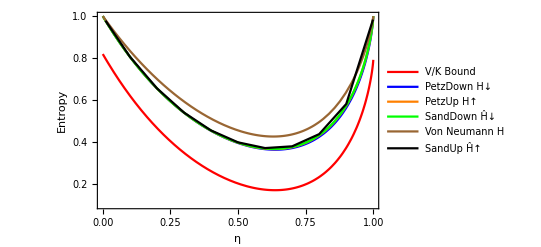

```mathematica
BpskEntropies=Legended[Show[{Plot[{bYE[1.2,η,1],PetzDown[1.2,η,1],PetzUp[1.2,η,1],sandwichDown[1.2,η,1],Neumann[1,η]},{η,0,1},PlotRange->{{0,1},{0.1,1}},Frame->True,FrameTicksStyle->Directive[Black,FontSize->12],(*dimensione numeri assi*)FrameLabel->{Style["η",FontSize->14],Style["Entropy",FontSize->14]},(*label assi ingranditi*)PlotStyle->{Red,Blue,Orange,Green,Brown}],ListLinePlot[sandwichUplist12,PlotStyle->Black]}],LineLegend[{Red,Blue,Orange,Green,Brown,Black},{Style["V/K Bound"],Style["PetzDown H↓"],Style["PetzUp H↑"],Style["SandDown Ĥ↓"],Style["Von Neumann H"],Style["SandUp Ĥ↑"]},LegendLayout->"Column",LegendMarkerSize->30]]
```

```mathematica
Export["/Users/Gabriele/Documents/Wolfram/PskPureLoss/grafici/BpskEntropies.png",BpskEntropies,ImageResolution->300]
```

CreateDirectory::privv: Privilege violation for file or directory C:\Users\Gabriele\.

Export::nodir: Directory C:\Users\Gabriele\Documents\Wolfram\PskPureLoss\grafici\ does not exist.

Export::noopen: Cannot open /Users/Gabriele/Documents/Wolfram/PskPureLoss/grafici/BpskEntropies.png.

$Failed

```mathematica
(*Definisco un set di etas campionati*)
(*etas=Subdivide[0.01,0.999,9]; *) (*10 punti*)
etas = {0.01,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,0.999} ;

(*Funzioni campionate*)
bYEpts=Table[{η,bYE[1.2,η,1]},{η,etas}];
petzDownPts=Table[{η,PetzDown[1.2,η,1]},{η,etas}];
petzUpPts=Table[{η,PetzUp[1.2,η,1]},{η,etas}];
sandwichDownPts=Table[{η,sandwichDown[1.2,η,1]},{η,etas}];
neumannPts=Table[{η,Neumann[1,η]},{η,etas}];
sandwichUplist12=Table[{ηi,sandwichUp[1.2,ηi,1][[1]]},{ηi,etas}];
```

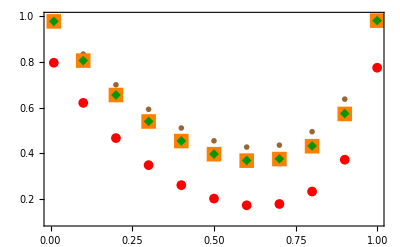

```mathematica
Needs["MaTeX`"];
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amsmath}"}];

datasets={bYEpts,petzDownPts,petzUpPts,sandwichDownPts,sandwichUplist12,neumannPts};
markers={{"●",10},{"▲",10},{"■",15},{"◆",10},{"✖",10},{"✚",10}};
colors={Red,Blue,Orange,Darker[Green,.4],Black,Brown};

labels=MaTeX[#,Magnification->2]&/@{"B_a","H^{\\downarrow}_a","H^{\\uparrow}_a","\\tilde{H}^{\\downarrow}_a","\\tilde{H}^{\\uparrow}_a","H"};

fig=Legended[ListPlot[datasets,PlotMarkers->markers,PlotStyle->colors,PlotRange->{{0,1},{0.1,1}},Frame->True,BaseStyle->{FontFamily->"Times",FontSize->20},FrameTicksStyle->Directive[Black,Thick],FrameLabel->{MaTeX["\\eta",Magnification->2.5],MaTeX["",Magnification->1.1]}],Placed[SwatchLegend[colors,labels,LegendMarkers->markers,LegendLayout->"Column",LegendMarkerSize->14],Right]]
```

```mathematica
Export["/Users/Gabriele/Documents/Wolfram/PskPureLoss/grafici/BpskEntropies.png",fig,ImageResolution->300]
```

CreateDirectory::privv: Privilege violation for file or directory C:\Users\Gabriele\.

Export::nodir: Directory C:\Users\Gabriele\Documents\Wolfram\PskPureLoss\grafici\ does not exist.

Export::noopen: Cannot open /Users/Gabriele/Documents/Wolfram/PskPureLoss/grafici/BpskEntropies.png.

$Failed

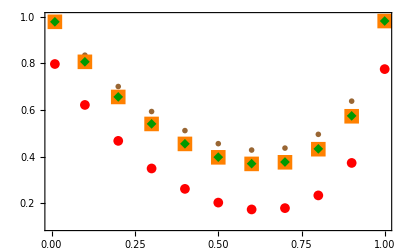

```mathematica
Needs["MaTeX`"];
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amsmath}"}];

datasets={bYEpts,petzDownPts,petzUpPts,sandwichDownPts,sandwichUplist12,neumannPts};
markers={{"●",10},{"▲",10},{"■",15},{"◆",10},{"✖",10},{"✚",10}};
colors={Red,Blue,Orange,Darker[Green,.4],Black,Brown};

labels=MaTeX[#,Magnification->2.5]&/@{"B_a","H^{\\downarrow}_a","H^{\\uparrow}_a","\\tilde{H}^{\\downarrow}_a","\\tilde{H}^{\\uparrow}_a","H"};

fig=Legended[ListPlot[datasets,PlotMarkers->markers,PlotStyle->colors,PlotRange->{{0,1},{0.1,1}},Frame->True,BaseStyle->{FontFamily->"Times",FontSize->20},FrameTicksStyle->Directive[Black,Thick],FrameLabel->{MaTeX["\\eta",Magnification->2.5],MaTeX["",Magnification->1.1]},ImageSize->600],(* <---qui ingrandisci il grafico*)Placed[SwatchLegend[colors,labels,LegendMarkers->markers,LegendLayout->"Column",LegendMarkerSize->14],Right]]
```

```mathematica
(*Analytic min entropy*)
```

```mathematica
rhoE=ρE[η,α];
rhoYE=ρYE[η,α];
rho1 =id⊙MatrixPower[rhoE,-1/2];
rho2=rho1.rhoYE.rho1//FullSimplify//MatrixForm
```

(1/2 | 1/2 Erf[√2 α √η] | 0 | 0
1/2 Erf[√2 α √η] | 1/2 | 0 | 0
0 | 0 | 1/2 | -1/2 Erf[√2 α √η]
0 | 0 | -1/2 Erf[√2 α √η] | 1/2)

```mathematica
({{1/2, 1/2 Erf[√2 α √η], 0, 0}, {1/2 Erf[√2 α √η], 1/2, 0, 0}, {0, 0, 1/2, -1/2 Erf[√2 α √η]}, {0, 0, -1/2 Erf[√2 α √η], 1/2}});
Autoval=Eigenvalues[({{1/2, 1/2 Erf[√2 α √η], 0, 0}, {1/2 Erf[√2 α √η], 1/2, 0, 0}, {0, 0, 1/2, -1/2 Erf[√2 α √η]}, {0, 0, -1/2 Erf[√2 α √η], 1/2}})];
```

Hmin[0,1]

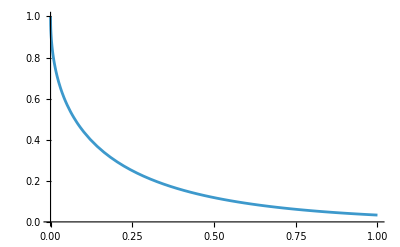

```mathematica
HminDownAn[η_,α_]:=Module[{list,λmax},
list={1/2 (1-Erf[√2 α √η]),1/2 (1+Erf[√2 α √η])};
λmax=Max[list];
-Log2[λmax]
]
Hmin[0,1]
Plot[{HminDownAn[η,1]},{η,0,1},PlotRange->{{0,1},{0,1}}]
```

```mathematica
(*opt bound sandwich*)
bYEq[a0_,η_,α_,q_]:=Module[{Hd2YE,HdaYE,HYE,VYE,K,ρYEηα,ρEηα,a=a0},
ρEηα=({{q, 0}, {0, 1-q}});
ρYEηα=1/2∑_(y=0)^1 (yb[y]⊙ρEy[η,α,y]);
VYE=1/Tr[ρYEηα] Tr[ρYEηα.MatrixPower[(MatrixLog[ρYEηα]-MatrixLog[id⊙ρEηα]),2]]/(Log[2])^2-dd[ρYEηα,id⊙ρEηα]^2;
Hd2YE=1/(1-2)Log2[Tr[MatrixPower[ρYEηα,2].MatrixPower[id⊙ρEηα,1-2]]]; (**)
HdaYE=1/(1-a)Log2[Tr[MatrixPower[ρYEηα,a].MatrixPower[id⊙ρEηα,1-a]]]; (*Petz down*)
HYE=H[ρYEηα]-H[ρE[η,α]];
K=1/(6(2-a)^3 Log[2])2^((a-1)(-HdaYE+HYE))(Log[2^(-Hd2YE+HYE)+ⅇ^2])^3;
HYE-((a-1)Log[2])/2 VYE-(a-1)^2 K
]
bYEopt[a0_,η_,α_]:=NMaximize[{bYEq[a0,η,α,q], 0<q<1},q]
bYEopt[1.1,0.9,1]
```

{0.590445,{q→0.651596}}

### comparison with cosmo

#### PetzDown

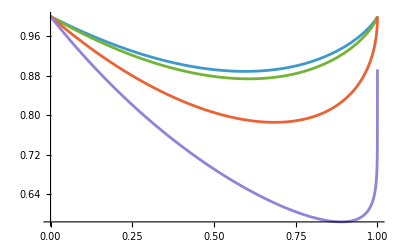

```mathematica
Func[η_,α_,a_]:=((1-ⅇ^(2 α^2 (-1+η)))^(1-a) (ⅇ^(-2 α^2 (-1+η)) ((1-ⅇ^(4 α^2 (-1+η)) √(ⅇ^(-4 α^2 (-1+η)) (1+(-1+ⅇ^(-4 α^2 (-1+η))) Erf[√2 α √η]^2)))^a-(1+ⅇ^(4 α^2 (-1+η)) √(ⅇ^(-4 α^2 (-1+η)) (1+(-1+ⅇ^(-4 α^2 (-1+η))) Erf[√2 α √η]^2)))^a)+√(ⅇ^(-4 α^2 (-1+η)) (1+(-1+ⅇ^(-4 α^2 (-1+η))) Erf[√2 α √η]^2)) ((1-ⅇ^(4 α^2 (-1+η)) √(ⅇ^(-4 α^2 (-1+η)) (1+(-1+ⅇ^(-4 α^2 (-1+η))) Erf[√2 α √η]^2)))^a+(1+ⅇ^(4 α^2 (-1+η)) √(ⅇ^(-4 α^2 (-1+η)) (1+(-1+ⅇ^(-4 α^2 (-1+η))) Erf[√2 α √η]^2)))^a))+(1+ⅇ^(2 α^2 (-1+η)))^(1-a) (ⅇ^(-2 α^2 (-1+η)) (-(1-ⅇ^(4 α^2 (-1+η)) √(ⅇ^(-4 α^2 (-1+η)) (1+(-1+ⅇ^(-4 α^2 (-1+η))) Erf[√2 α √η]^2)))^a+(1+ⅇ^(4 α^2 (-1+η)) √(ⅇ^(-4 α^2 (-1+η)) (1+(-1+ⅇ^(-4 α^2 (-1+η))) Erf[√2 α √η]^2)))^a)+√(ⅇ^(-4 α^2 (-1+η)) (1+(-1+ⅇ^(-4 α^2 (-1+η))) Erf[√2 α √η]^2)) ((1-ⅇ^(4 α^2 (-1+η)) √(ⅇ^(-4 α^2 (-1+η)) (1+(-1+ⅇ^(-4 α^2 (-1+η))) Erf[√2 α √η]^2)))^a+(1+ⅇ^(4 α^2 (-1+η)) √(ⅇ^(-4 α^2 (-1+η)) (1+(-1+ⅇ^(-4 α^2 (-1+η))) Erf[√2 α √η]^2)))^a)))/(4 √(ⅇ^(-4 α^2 (-1+η)) (1+(-1+ⅇ^(-4 α^2 (-1+η))) Erf[√2 α √η]^2)))
Petz[η_,α_,a_]:=1/(1-a)Log2[2/2^a Func[η,α,a]]
Plot[{Petz[η,α,a]/.{α->0.5,a->1.001},,Petz[η,α,a]/.{α->0.5,a->1.1},Petz[η,α,a]/.{α->0.5,a->1.5},Petz[η,α,a]/.{α->0.5,a->1.9}},{η,0,1}]
```

```mathematica
Petz[.7,0.5,2.5]-PetzDown[2.5,.7,0.5] (*comparison PetzDown*)
```

1.91513×10^-15

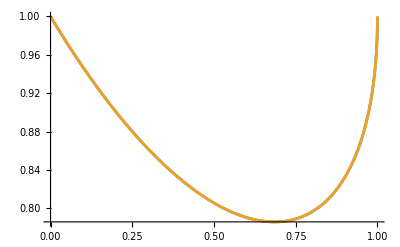

```mathematica
Plot[{Petz[η,0.5,1.5],PetzDown[1.5,η,0.5]},{η,0,1}]
```

```mathematica
expr=Petz[η,α,a]/.{ⅇ^(2 α^2 (-1+η))->f1,ⅇ^(-2 α^2 (-1+η))->1/f1,ⅇ^(4 α^2 (-1+η))->f1^2,ⅇ^(-4 α^2 (-1+η))->1/f1^2,
Erf[√2 α √η] ->f2}
```

Log[(2^(-1-a) ((1-f1)^(1-a) (((1-f1^2 √((1+(-1+1/f1^2) f2^2)/f1^2))^a-(1+f1^2 √((1+(-1+1/f1^2) f2^2)/f1^2))^a)/f1+√((1+(-1+1/f1^2) f2^2)/f1^2) ((1-f1^2 √((1+(-1+1/f1^2) f2^2)/f1^2))^a+(1+f1^2 √((1+(-1+1/f1^2) f2^2)/f1^2))^a))+(1+f1)^(1-a) ((-(1-f1^2 √((1+(-1+1/f1^2) f2^2)/f1^2))^a+(1+f1^2 √((1+(-1+1/f1^2) f2^2)/f1^2))^a)/f1+√((1+(-1+1/f1^2) f2^2)/f1^2) ((1-f1^2 √((1+(-1+1/f1^2) f2^2)/f1^2))^a+(1+f1^2 √((1+(-1+1/f1^2) f2^2)/f1^2))^a))))/(√((1+(-1+1/f1^2) f2^2)/f1^2))]/((1-a) Log[2])

```mathematica
expr2=expr/.{ √((1+(-1+1/f1^2) f2^2)/f1^2)->f3,1/(√((1+(-1+1/f1^2) f2^2)/f1^2))->1/f3}
```

Log[(2^(-1-a) ((1-f1)^(1-a) (((1-f1^2 f3)^a-(1+f1^2 f3)^a)/f1+f3 ((1-f1^2 f3)^a+(1+f1^2 f3)^a))+(1+f1)^(1-a) ((-(1-f1^2 f3)^a+(1+f1^2 f3)^a)/f1+f3 ((1-f1^2 f3)^a+(1+f1^2 f3)^a))))/f3]/((1-a) Log[2])

```mathematica
expr3=expr2/.{f1^2 f3->f4, (1-f1)^(1-a)->f5,(1+f1)^(1-a)->f6}
```

Log[(2^(-1-a) ((((1-f4)^a-(1+f4)^a)/f1+f3 ((1-f4)^a+(1+f4)^a)) f5+((-(1-f4)^a+(1+f4)^a)/f1+f3 ((1-f4)^a+(1+f4)^a)) f6))/f3]/((1-a) Log[2])

```mathematica
expr3/.{f3 ((1-f4)^a+(1+f4)^a)->f7,((1-f4)^a-(1+f4)^a)/f1->f8,(-(1-f4)^a+(1+f4)^a)/f1->f9}
```

Log[(2^(-1-a) (f5 (f7+f8)+f6 (f7+f9)))/f3]/((1-a) Log[2])

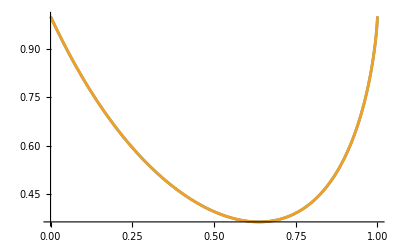

```mathematica
Ffull3[α_,η_,a_]:=Module[{f1,f2,f3,f4,f5,f6,f7,f8,f9},
f1=Exp[2 α^2(η-1)];
f2=Erf[Sqrt[2]α Sqrt[η]];
f3=Sqrt[(1+(-1+1/f1^2) f2^2)/f1^2];
f4=f1^2 f3;
f5=(1-f1)^(1-a);
f6=(1+f1)^(1-a);
f7=f3 ((1-f4)^a+(1+f4)^a);
f8=((1-f4)^a-(1+f4)^a)/f1;
f9=(-(1-f4)^a+(1+f4)^a)/f1;

Log2[(2^(-1-a) (f5 (f7+f8)+f6 (f7+f9)))/f3]/(1-a)]
Plot[{Ffull3[1,η,1.2],Petz[η,1,1.2]},{η,0,1}]
```

```mathematica
ee1= ((((1-f4)^a-(1+f4)^a)/f1+f3 ((1-f4)^a+(1+f4)^a)) f5+((-(1-f4)^a+(1+f4)^a)/f1+f3 ((1-f4)^a+(1+f4)^a)) f6)/(4 f3)/.{f3 ((1-f4)^a+(1+f4)^a)->f7,((1-f4)^a-(1+f4)^a)/f1->f8,(-(1-f4)^a+(1+f4)^a)/f1->f9}
```

(f5 (f7+f8)+f6 (f7+f9))/(4 f3)

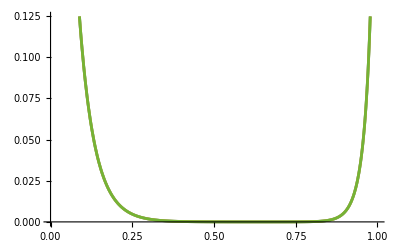

```mathematica
PetzAn[α_,η_,a_]:=Module[{f1,f2,f3,f4,f5,f6,f7,f8,f9},
f1=Exp[2 α^2(η-1)];
f2=Erf[Sqrt[2]α Sqrt[η]];
f3=Sqrt[(1+(-1+1/f1^2) f2^2)/f1^2];
f4=f1^2 f3;
f5=(1-f1)^(1-a);
f6=(1+f1)^(1-a);
f7=f3 ((1-f4)^a+(1+f4)^a);
f8=((1-f4)^a-(1+f4)^a)/f1;
f9=(-(1-f4)^a+(1+f4)^a)/f1;

1+Log2[(f5 (f7+f8)+f6 (f7-f8))/(4 f3)]/(1-a)]
Plot[{PetzAn[3,η,1.7],Petz[η,3,1.7],PetzDownElegant[η,3,1.7]},{η,0,1}]
```

```mathematica
Plot3D[Petz[η,α,1.8],{η,1,0},{α,0,1.5}]
```

-Graphics3D-

```mathematica
ClearAll[PetzDownElegant];
PetzDownElegant[η_,α_,a_]:=Module[{κ,r,g,θ,ϕ},
κ=Exp[2 α^2 (η-1)];
r=Erf[Sqrt[2 η] α];
g=Sqrt[1+(κ^-2-1) r^2];
θ=ArcTanh[κ g];
ϕ=ArcTanh[κ];
1+1/(1-a)*Log[2,Sech[θ]^a*Sech[ϕ]^(1-a)*(Cosh[a θ] Cosh[(1-a) ϕ]+g^-1 Sinh[a θ] Sinh[(1-a) ϕ])]]
PetzDownElegant[0.9,4,1.1]
```

0.00107909

#### PetzUp

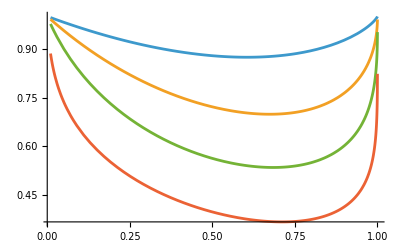

```mathematica
Func2[η_,α_,a_]:=1/2 ((2^-a (ⅇ^(-4 α^2 (1-η)) (ⅇ^(4 α^2 (1-η))-√(ⅇ^(4 α^2 (1-η)) (1-Erf[√2 α √η]^2+ⅇ^(4 α^2 (1-η)) Erf[√2 α √η]^2))))^a (ⅇ^(2 α^2 (1-η))+√(ⅇ^(4 α^2 (1-η)) (1-Erf[√2 α √η]^2+ⅇ^(4 α^2 (1-η)) Erf[√2 α √η]^2))))/(√(ⅇ^(4 α^2 (1-η)) (1-Erf[√2 α √η]^2+ⅇ^(4 α^2 (1-η)) Erf[√2 α √η]^2)))+(2^-a (-ⅇ^(2 α^2 (1-η))+√(ⅇ^(4 α^2 (1-η)) (1-Erf[√2 α √η]^2+ⅇ^(4 α^2 (1-η)) Erf[√2 α √η]^2))) (ⅇ^(-4 α^2 (1-η)) (ⅇ^(4 α^2 (1-η))+√(ⅇ^(4 α^2 (1-η)) (1-Erf[√2 α √η]^2+ⅇ^(4 α^2 (1-η)) Erf[√2 α √η]^2))))^a)/(√(ⅇ^(4 α^2 (1-η)) (1-Erf[√2 α √η]^2+ⅇ^(4 α^2 (1-η)) Erf[√2 α √η]^2))))^(1/a)+1/2 (-((2^-a (ⅇ^(2 α^2 (1-η))-√(ⅇ^(4 α^2 (1-η)) (1-Erf[√2 α √η]^2+ⅇ^(4 α^2 (1-η)) Erf[√2 α √η]^2))) (ⅇ^(-4 α^2 (1-η)) (ⅇ^(4 α^2 (1-η))-√(ⅇ^(4 α^2 (1-η)) (1-Erf[√2 α √η]^2+ⅇ^(4 α^2 (1-η)) Erf[√2 α √η]^2))))^a)/(√(ⅇ^(4 α^2 (1-η)) (1-Erf[√2 α √η]^2+ⅇ^(4 α^2 (1-η)) Erf[√2 α √η]^2))))+(2^-a (ⅇ^(2 α^2 (1-η))+√(ⅇ^(4 α^2 (1-η)) (1-Erf[√2 α √η]^2+ⅇ^(4 α^2 (1-η)) Erf[√2 α √η]^2))) (ⅇ^(-4 α^2 (1-η)) (ⅇ^(4 α^2 (1-η))+√(ⅇ^(4 α^2 (1-η)) (1-Erf[√2 α √η]^2+ⅇ^(4 α^2 (1-η)) Erf[√2 α √η]^2))))^a)/(√(ⅇ^(4 α^2 (1-η)) (1-Erf[√2 α √η]^2+ⅇ^(4 α^2 (1-η)) Erf[√2 α √η]^2))))^(1/a)
PetzOPT[η_,α_,a_]:=a/(1-a)Log2[Func2[η,α,a]]
Plot[{a/(1-a)Log2[Func2[η,α,a]]/.{α->0.5,a->1.1},a/(1-a)Log2[Func2[η,α,a]]/.{α->0.5,a->2},a/(1-a)Log2[Func2[η,α,a]]/.{α->0.5,a->3},a/(1-a)Log2[Func2[η,α,a]]/.{α->0.5,a->5}},{η,0.01,0.9999}]
```

```mathematica
{PetzOPT[.5,.5,1.5],PetzUp[1.5,.5,.5]}
```

{0.814145,0.814145}

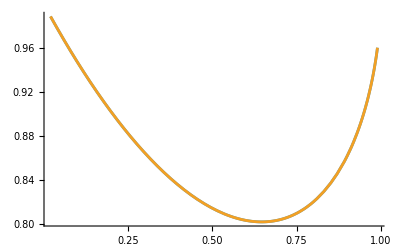

```mathematica
Plot[{PetzOPT[η,.5,1.5],PetzUp[1.5,η,.5]},{η,0.02,0.99}]
```

```mathematica
expr1=1/2 ((2^-a ((1-f1^2 f3)^a+(1+f1^2 f3)^a+((1-f1^2 f3)^a-(1+f1^2 f3)^a)/(f1 f3)))^(1/a)+(2^-a ((1-f1^2 f3)^a+(1+f1^2 f3)^a+(-(1-f1^2 f3)^a+(1+f1^2 f3)^a)/(f1 f3)))^(1/a))/.{(1+f1^2 f3)^a->g1,(1-f1^2 f3)^a->g2}
```

1/2 ((2^-a (g1+(g1-g2)/(f1 f3)+g2))^(1/a)+(2^-a (g1+g2+(-g1+g2)/(f1 f3)))^(1/a))

```mathematica
1/2 ((2^-a (g1+(g1-g2)/(f1 f3)+g2))^(1/a)+(2^-a (g1+g2+(-g1+g2)/(f1 f3)))^(1/a))//FullSimplify
```

1/2 ((2^-a (g1+(g1-g2)/(f1 f3)+g2))^(1/a)+(2^-a (g1+g2+(-g1+g2)/(f1 f3)))^(1/a))

```mathematica
PetzoptAn[η_,α_,a_]:=Module[{f1,f2,f3,g1,g2},
f1=Exp[2 α^2(η-1)];
f2=Erf[Sqrt[2]α Sqrt[η]];
f3=Sqrt[(1+(-1+1/f1^2) f2^2)/f1^2];
g1=(1+f1^2 f3)^a;
g2=(1-f1^2 f3)^a;
(*a/(1-a)Log2[1/2 ((2^-a (g1+(g1-g2)/(f1 f3)+g2))^(1/a)+(2^-a (g1+g2+(-g1+g2)/(f1 f3)))^(1/a))]*)
-2 a/(1-a)+a/(1-a)Log2[(((g1+(g1-g2)/(f1 f3)+g2))^(1/a)+((g1+g2+(-g1+g2)/(f1 f3)))^(1/a))]
]
```

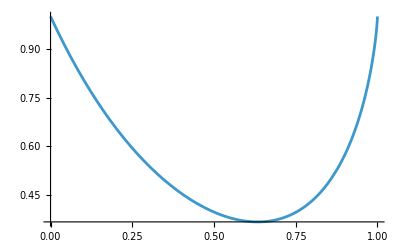

```mathematica
Plot[{PetzElegant[η,1,1.2]},{η,0,1}]
```

```mathematica
(*---versione elegante---*)
ClearAll[PetzElegant];
PetzElegant[η_,α_,a_]:=Module[{κ,r,γt,θ},
κ=Exp[2 α^2 (η-1)];
r=Erf[Sqrt[2 η] α];
γt=Sqrt[1+(κ^-2-1) r^2];
θ=ArcTanh[κ γt];
(a/(1-a))*Log2[2^(1/a-2)*Sech[θ]*((Cosh[a θ]+γt^-1 Sinh[a θ])^(1/a)+(Cosh[a θ]-γt^-1 Sinh[a θ])^(1/a))]];
```

#### SandwichDown

```mathematica
Func3[η_,α_,a_]:=(2^(-(1+a)/a) ((1-ⅇ^(2 α^2 (-1+η)))^(1/a)+(1+ⅇ^(2 α^2 (-1+η)))^(1/a)-√((1-ⅇ^(2 α^2 (-1+η)))^(2/a)+(1+ⅇ^(2 α^2 (-1+η)))^(2/a)+2 (1-ⅇ^(4 α^2 (-1+η)))^(1/a) (-1+2 Erf[√2 α √η]^2))))^a+(2^(-(1+a)/a) ((1-ⅇ^(2 α^2 (-1+η)))^(1/a)+(1+ⅇ^(2 α^2 (-1+η)))^(1/a)+√((1-ⅇ^(2 α^2 (-1+η)))^(2/a)+(1+ⅇ^(2 α^2 (-1+η)))^(2/a)+2 (1-ⅇ^(4 α^2 (-1+η)))^(1/a) (-1+2 Erf[√2 α √η]^2))))^a
Sand[η_,α_,a_]:=1/(1-a)Log2[2/2^a Func3[η,α,a]]
```

{0.829024,0.829024}

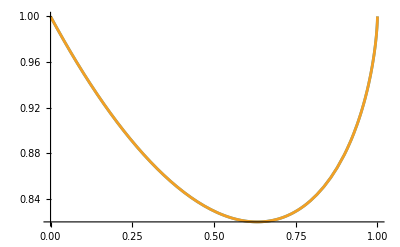

```mathematica
{Sand[.5,.5,1.5],sandwichDown[1.5,.5,.5]}(*comparison with sandwich down*)
Plot[{Sand[η,.5,1.5],sandwichDown[1.5,η,.5]},{η,0,1}]
```

```mathematica
exp1=(2^(-(1+a)/a) ((1-ⅇ^(2 α^2 (-1+η)))^(1/a)+(1+ⅇ^(2 α^2 (-1+η)))^(1/a)-√((1-ⅇ^(2 α^2 (-1+η)))^(2/a)+(1+ⅇ^(2 α^2 (-1+η)))^(2/a)+2 (1-ⅇ^(4 α^2 (-1+η)))^(1/a) (-1+2 Erf[√2 α √η]^2))))^a+(2^(-(1+a)/a) ((1-ⅇ^(2 α^2 (-1+η)))^(1/a)+(1+ⅇ^(2 α^2 (-1+η)))^(1/a)+√((1-ⅇ^(2 α^2 (-1+η)))^(2/a)+(1+ⅇ^(2 α^2 (-1+η)))^(2/a)+2 (1-ⅇ^(4 α^2 (-1+η)))^(1/a) (-1+2 Erf[√2 α √η]^2))))^a/.{ⅇ^(2 α^2 (-1+η))->f1,ⅇ^(-2 α^2 (-1+η))->1/f1,ⅇ^(4 α^2 (-1+η))->f1^2,ⅇ^(-4 α^2 (-1+η))->1/f1^2,
Erf[√2 α √η] ->f2}//FullSimplify
```

(2^(-(1+a)/a) ((1-f1)^(1/a)+(1+f1)^(1/a)-√(((1-f1)^(1/a)-(1+f1)^(1/a))^2+4 (1-f1^2)^(1/a) f2^2)))^a+(2^(-(1+a)/a) ((1-f1)^(1/a)+(1+f1)^(1/a)+√(((1-f1)^(1/a)-(1+f1)^(1/a))^2+4 (1-f1^2)^(1/a) f2^2)))^a

```mathematica
exp2 = (2^(-(1+a)/a) ((1-f1)^(1/a)+(1+f1)^(1/a)-√(((1-f1)^(1/a)-(1+f1)^(1/a))^2+4 (1-f1^2)^(1/a) f2^2)))^a+(2^(-(1+a)/a) ((1-f1)^(1/a)+(1+f1)^(1/a)+√(((1-f1)^(1/a)-(1+f1)^(1/a))^2+4 (1-f1^2)^(1/a) f2^2)))^a/.{(1-f1)^(1/a)->h1,(1+f1)^(1/a)->h2}
```

(2^(-(1+a)/a) (h1-√(4 (1-f1^2)^(1/a) f2^2+(h1-h2)^2)+h2))^a+(2^(-(1+a)/a) (h1+√(4 (1-f1^2)^(1/a) f2^2+(h1-h2)^2)+h2))^a

```mathematica
exp3=(2^(-(1+a)/a) (h1-√(4 (1-f1^2)^(1/a) f2^2+(h1-h2)^2)+h2))^a+(2^(-(1+a)/a) (h1+√(4 (1-f1^2)^(1/a) f2^2+(h1-h2)^2)+h2))^a/.{√(4 (1-f1^2)^(1/a) f2^2+(h1-h2)^2)->h3}
```

(2^(-(1+a)/a) (h1+h2-h3))^a+(2^(-(1+a)/a) (h1+h2+h3))^a

```mathematica
SandAn[η_,α_,a_]:=Module[{f1,f2,h1,h2,h3},
f1=Exp[2 α^2(η-1)];
f2=Erf[Sqrt[2]α Sqrt[η]];
h1=(1-f1)^(1/a);
h2=(1+f1)^(1/a);
h3=√(4 (1-f1^2)^(1/a) f2^2+(h1-h2)^2);
1-(1+a)/(1-a)+1/(1-a)Log2[(h1+h2-h3)^a+(h1+h2+h3)^a]

]
```

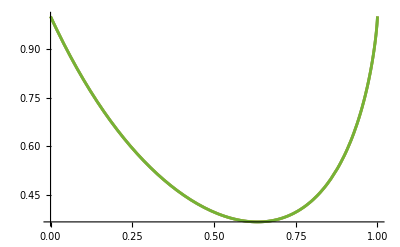

```mathematica
Plot[{SandAn[η,1,1.2],Sand[η,1,1.2],SandElegant[η,1,1.2]},{η,0,1}]
```

```mathematica
(*---versione elegante---*)
ClearAll[SandElegant];
SandElegant[η_,α_,a_]:=Module[{κ,r,ϕ,Δ},
κ=Exp[2 α^2 (η-1)];
r=Erf[Sqrt[2 η] α];
ϕ=ArcTanh[κ];
Δ=Sqrt[r^2+Sinh[ϕ/a]^2];
-2 a/(1-a)+1/(1-a)*Log2[2^a Sech[ϕ]*((Cosh[ϕ/a]-Δ)^a+(Cosh[ϕ/a]+Δ)^a)]];
```

#### SandwichUp

```mathematica
Func4[η_,α_,a_,q_]:=4^-a ((1/((-1+q) q)(-(1-q)^(1/a) q+ⅇ^(2 α^2 (-1+η)) (1-q)^(1/a) q+q^(1+1/a)+ⅇ^(2 α^2 (-1+η)) q^(1+1/a)-q^(1/a)-ⅇ^(2 α^2 (-1+η)) q^(1/a)-1/2 √(4 ((-1+ⅇ^(2 α^2 (-1+η))) (1-q)^(1/a) q+(1+ⅇ^(2 α^2 (-1+η))) q^(1+1/a)-(1+ⅇ^(2 α^2 (-1+η))) q^(1/a))^2-16 (-1+ⅇ^(4 α^2 (-1+η))) (-((-1+q) q))^(1+1/a) (-1+Erf[√2 α √η]^2))))^a+(1/((-1+q) q)(-(1-q)^(1/a) q+ⅇ^(2 α^2 (-1+η)) (1-q)^(1/a) q+q^(1+1/a)+ⅇ^(2 α^2 (-1+η)) q^(1+1/a)-q^(1/a)-ⅇ^(2 α^2 (-1+η)) q^(1/a)+1/2 √(4 ((-1+ⅇ^(2 α^2 (-1+η))) (1-q)^(1/a) q+(1+ⅇ^(2 α^2 (-1+η))) q^(1+1/a)-(1+ⅇ^(2 α^2 (-1+η))) q^(1/a))^2-16 (-1+ⅇ^(4 α^2 (-1+η))) (-((-1+q) q))^(1+1/a) (-1+Erf[√2 α √η]^2))))^a)
QFunc5[η_,α_,a_]:=NMinimize[{Func4[η,α,a,q],0<q<1},q]
Func5[η_,α_,a_]:=QFunc5[η,α,a][[1]]
SandOPT[η_,α_,a_]:=1/(1-a)Log2[2/2^a Func5[η,α,a]]
```

```mathematica
sandwichUplistC=Table[{ηi,SandOPT[ηi,.5,1.3]},{ηi,0,1,.025}];
```

```mathematica
sandwichUplistC
```

{{0.,Indeterminate},{0.025,Indeterminate},{0.05,Indeterminate},{0.075,0.967676},{0.1,0.95768},{0.125,0.948077},{0.15,0.938871},{0.175,Indeterminate},{0.2,0.92166},{0.225,Indeterminate},{0.25,Indeterminate},{0.275,Indeterminate},{0.3,0.892182},{0.325,0.885878},{0.35,0.880016},{0.375,0.874606},{0.4,0.869658},{0.425,0.865184},{0.45,Indeterminate},{0.475,0.857713},{0.5,0.854747},{0.525,0.852318},{0.55,0.850447},{0.575,0.849158},{0.6,Indeterminate},{0.625,Indeterminate},{0.65,0.849065},{0.675,0.850411},{0.7,0.852517},{0.725,0.855439},{0.75,0.859244},{0.775,Indeterminate},{0.8,0.869839},{0.825,Indeterminate},{0.85,Indeterminate},{0.875,Indeterminate},{0.9,Indeterminate},{0.925,Indeterminate},{0.95,Indeterminate},{0.975,0.961065},{1.,Indeterminate}}

```mathematica
sandwichUplist
```

{{0.,1.},{0.025,0.947149},{0.05,0.89744},{0.075,0.850695},{0.1,0.806746},{0.125,0.765445},{0.15,0.726653},{0.175,0.690248},{0.2,0.656116},{0.225,0.624159},{0.25,0.594286},{0.275,0.566419},{0.3,0.540492},{0.325,0.516445},{0.35,0.494234},{0.375,0.473821},{0.4,0.455181},{0.425,0.438301},{0.45,0.423179},{0.475,0.409827},{0.5,0.398268},{0.525,0.388542},{0.55,0.380708},{0.575,0.374839},{0.6,0.371034},{0.625,0.369415},{0.65,0.370132},{0.675,0.373373},{0.7,0.379366},{0.725,0.388392},{0.75,0.400796},{0.775,0.417008},{0.8,0.437571},{0.825,0.463178},{0.85,0.494743},{0.875,0.533502},{0.9,0.581221},{0.925,0.6406},{0.95,0.716287},{0.975,0.818287},{1.,1.}}

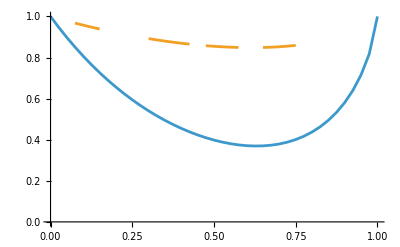

```mathematica
ListLinePlot[{sandwichUplist,sandwichUplistC}]
```

```mathematica
e1=4^-a ((1/((-1+q) q)(-(1-q)^(1/a) q+ⅇ^(2 α^2 (-1+η)) (1-q)^(1/a) q+q^(1+1/a)+ⅇ^(2 α^2 (-1+η)) q^(1+1/a)-q^(1/a)-ⅇ^(2 α^2 (-1+η)) q^(1/a)-1/2 √(4 ((-1+ⅇ^(2 α^2 (-1+η))) (1-q)^(1/a) q+(1+ⅇ^(2 α^2 (-1+η))) q^(1+1/a)-(1+ⅇ^(2 α^2 (-1+η))) q^(1/a))^2-16 (-1+ⅇ^(4 α^2 (-1+η))) (-((-1+q) q))^(1+1/a) (-1+Erf[√2 α √η]^2))))^a+(1/((-1+q) q)(-(1-q)^(1/a) q+ⅇ^(2 α^2 (-1+η)) (1-q)^(1/a) q+q^(1+1/a)+ⅇ^(2 α^2 (-1+η)) q^(1+1/a)-q^(1/a)-ⅇ^(2 α^2 (-1+η)) q^(1/a)+1/2 √(4 ((-1+ⅇ^(2 α^2 (-1+η))) (1-q)^(1/a) q+(1+ⅇ^(2 α^2 (-1+η))) q^(1+1/a)-(1+ⅇ^(2 α^2 (-1+η))) q^(1/a))^2-16 (-1+ⅇ^(4 α^2 (-1+η))) (-((-1+q) q))^(1+1/a) (-1+Erf[√2 α √η]^2))))^a)/.{ⅇ^(2 α^2 (-1+η))->f1,ⅇ^(-2 α^2 (-1+η))->1/f1,ⅇ^(4 α^2 (-1+η))->f1^2,ⅇ^(-4 α^2 (-1+η))->1/f1^2,
Erf[√2 α √η] ->f2}//FullSimplify
```

4^-a ((((-1+f1) (1-q)^(1/a) q+(1+f1) (-1+q) q^(1/a)-√(-4 (-1+f1^2) (-1+f2^2) (-((-1+q) q))^(1+1/a)+((-1+f1) (1-q)^(1/a) q+(1+f1) (-1+q) q^(1/a))^2))/((-1+q) q))^a+(((-1+f1) (1-q)^(1/a) q+(1+f1) (-1+q) q^(1/a)+√(-4 (-1+f1^2) (-1+f2^2) (-((-1+q) q))^(1+1/a)+((-1+f1) (1-q)^(1/a) q+(1+f1) (-1+q) q^(1/a))^2))/((-1+q) q))^a)

```mathematica
e2=4^-a ((((-1+f1) (1-q)^(1/a) q+(1+f1) (-1+q) q^(1/a)-√(-4 (-1+f1^2) (-1+f2^2) (-(-1+q) q)^(1+1/a)+((-1+f1) (1-q)^(1/a) q+(1+f1) (-1+q) q^(1/a))^2))/((-1+q) q))^a+(((-1+f1) (1-q)^(1/a) q+(1+f1) (-1+q) q^(1/a)+√(-4 (-1+f1^2) (-1+f2^2) (-(-1+q) q)^(1+1/a)+((-1+f1) (1-q)^(1/a) q+(1+f1) (-1+q) q^(1/a))^2))/((-1+q) q))^a)/.{(-1+f1)->d1,(1+f1) ->d2,(-1+f1^2)->d3,(-1+f2^2) ->d4}
```

4^-a (((d1 (1-q)^(1/a) q+d2 (-1+q) q^(1/a)-√(-4 d3 d4 ((1-q) q)^(1+1/a)+(d1 (1-q)^(1/a) q+d2 (-1+q) q^(1/a))^2))/((-1+q) q))^a+((d1 (1-q)^(1/a) q+d2 (-1+q) q^(1/a)+√(-4 d3 d4 ((1-q) q)^(1+1/a)+(d1 (1-q)^(1/a) q+d2 (-1+q) q^(1/a))^2))/((-1+q) q))^a)

#### von neuman entropy

```mathematica
von[η_,α_]:=-1/2 (-1+ⅇ^(2 α^2 (-1+η))) Log[1/2 (1-ⅇ^(2 α^2 (-1+η)))]+1/2 (1+ⅇ^(2 α^2 (-1+η))) Log[1/2 (1+ⅇ^(2 α^2 (-1+η)))]+1/2 ((-1+ⅇ^(4 α^2 (-1+η)) √(ⅇ^(-8 α^2 (-1+η)) (ⅇ^(4 α^2 (-1+η))-(-1+ⅇ^(4 α^2 (-1+η))) Erf[√2 α √η]^2))) Log[1/4 (1-ⅇ^(4 α^2 (-1+η)) √(ⅇ^(-4 α^2 (-1+η)) (1+(-1+ⅇ^(-4 α^2 (-1+η))) Erf[√2 α √η]^2)))]-(1+ⅇ^(4 α^2 (-1+η)) √(ⅇ^(-8 α^2 (-1+η)) (ⅇ^(4 α^2 (-1+η))-(-1+ⅇ^(4 α^2 (-1+η))) Erf[√2 α √η]^2))) Log[1/4 (1+ⅇ^(4 α^2 (-1+η)) √(ⅇ^(-4 α^2 (-1+η)) (1+(-1+ⅇ^(-4 α^2 (-1+η))) Erf[√2 α √η]^2)))])
{Log2[ⅇ]von[.5,.5],bYE[1.0000001,.5,.5]}
```

{0.892533,0.892533}

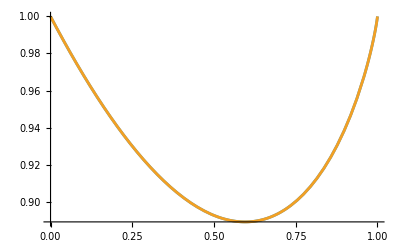

```mathematica
Plot[{Log2[ⅇ]von[η,.5],bYE[1.0000001,η,.5]},{η,0,1}]
```

#### Asymptotic rate

```mathematica
h[x_] := Piecewise[{{-x Log2[x] - (1 - x) Log2[1 - x], 0 < x < 1}}, 0]
ra[η_,α_]:=bYE[1.000001,η,α]-h[1/2 Erfc[√(2η) α]]
```

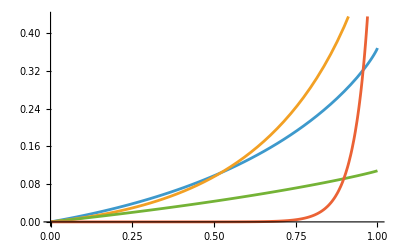

```mathematica
Plot[{ra[η,.5],ra[η,.75],ra[η,.25],ra[η,2.25]},{η,0,1}]
```

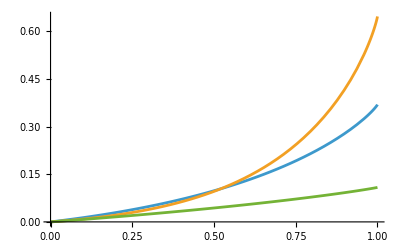

```mathematica
Plot[{Log2[ⅇ]von[η,.5]-h[1/2 Erfc[√(2η) .5]],Log2[ⅇ]von[η,.75]-h[1/2 Erfc[√(2η) .75]],Log2[ⅇ]von[η,.25]-h[1/2 Erfc[√(2η) .25]]},{η,0,1}]
```

#### block-size rate

```mathematica
g[ϵ_]:=Log2[2/ϵ^2]
g2=-2*Log2[1/10^-8]+1//N
g[10^-8]//N
(*Rate con Sand Up ottimizzato*)
sandwichUpq[a_,η_,α_,q_]:=1/(1-a)Log2[2/2^a Re@Tr[MatrixPower[({{q^((1-a)/(2a)), 0}, {0, (1-q)^((1-a)/(2a))}}).ρEy[η,α,1].({{q^((1-a)/(2a)), 0}, {0, (1-q)^((1-a)/(2a))}}),a]]]
rn[a_,η_,α_,n_,ϵ_,q_]:=sandwichUpq[a,η,α,q]-g[ϵ]/(n(a-1))-h[1/2 Erfc[√(2η) α]]+g2/n
rateVSn[η_,n_]:=Module[{nmax,lp},
nmax=NMaximize[{rn[a,η,α,n,10^-8,q],10^-8<q<1,1000>a>1+10^-8,α>0},{q,a,α},WorkingPrecision->60,AccuracyGoal->20,PrecisionGoal->20,MaxIterations->1000, Method->"NelderMead"];
lp={q,a,α}/.nmax[[2]];
Flatten@Join[{nmax[[1]]},{lp}]
]

(*Rate con Bound ottimizzato*)
rnB[a_,η_,α_,n_,ϵ_]:=bYE[a,η,α]-g[ϵ]/(n(a-1))-h[1/2 Erfc[√(2η) α]]+g2/n
rateBVSn[η_,n_]:=Module[{nmax,lp},
nmax=NMaximize[{rnB[a,η,α,n,10^-8],1<a<2,0<α<2},{a,α}];
lp={a,α}/.nmax[[2]];
Flatten@Join[{nmax[[1]]},{lp}]
]
```

-52.1508

54.1508

```mathematica
rateVSn[.9,600]
```

NMaximize::precw: The precision of the argument function (0.0869181+Log[20000000000000000]/(600 (-1+a) Log[2])-Log[2^(1-a) Re[-1. Power[«2»] Power[«2»] Power[«2»] Power[«2»] Power[«2»] Plus[«2»]-1. Power[«2»] Power[«2»] Power[«2»] Power[«2»] Power[«2»] Plus[«2»]+1. Power[«2»] Power[«2»] Power[«2»] Power[«2»] Power[«2»] Plus[«2»]+1. Power[«2»] Power[«2»] Power[«2»] Power[«2»] Power[«2»] Plus[«2»]]]/((1-a) Log[2])+(Piecewise[{{-((1+Times[«2»]) Log[Plus[«2»]])/Log[«1»]-(Erfc[Times[«2»]] Log[Times[«2»]])/(2 Log[«1»]), 0<1/2 Erfc[Times[«2»]]<1}, {0, True}}])) is less than WorkingPrecision (60).

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

{0.11878101681052977145469640163355506956577301025390625,0.810383448999651870559086075160026860521646735296612238087917,2.67404235416290232821371115283115897382697839839281981282257,1.00721399419352723653601770912842438056415033449794055431395}

```mathematica
nlist={370,380,390,400,410,420,430,440,450,460,470,480,490,500,550,600,700,800,900,1000,5000,10000,50000,100000,1000000,10000000,100000000}
```

{370,380,390,400,410,420,430,440,450,460,470,480,490,500,550,600,700,800,900,1000,5000,10000,50000,100000,1000000,10000000,100000000}

```mathematica
listTransizione=Table[rateVSn[.9,ni],{ni,nlist}]
```

NMaximize::precw: The precision of the argument function (0.140948+Log[20000000000000000]/(370 (-1+a) Log[2])-Log[2^(1-a) Re[-1. Power[«2»] Power[«2»] Power[«2»] Power[«2»] Power[«2»] Plus[«2»]-1. Power[«2»] Power[«2»] Power[«2»] Power[«2»] Power[«2»] Plus[«2»]+1. Power[«2»] Power[«2»] Power[«2»] Power[«2»] Power[«2»] Plus[«2»]+1. Power[«2»] Power[«2»] Power[«2»] Power[«2»] Power[«2»] Plus[«2»]]]/((1-a) Log[2])+(Piecewise[{{-((1+Times[«2»]) Log[Plus[«2»]])/Log[«1»]-(Erfc[Times[«2»]] Log[Times[«2»]])/(2 Log[«1»]), 0<1/2 Erfc[Times[«2»]]<1}, {0, True}}])) is less than WorkingPrecision (60).

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

NMaximize::precw: The precision of the argument function (0.137239+Log[20000000000000000]/(380 (-1+a) Log[2])-Log[2^(1-a) Re[-1. Power[«2»] Power[«2»] Power[«2»] Power[«2»] Power[«2»] Plus[«2»]-1. Power[«2»] Power[«2»] Power[«2»] Power[«2»] Power[«2»] Plus[«2»]+1. Power[«2»] Power[«2»] Power[«2»] Power[«2»] Power[«2»] Plus[«2»]+1. Power[«2»] Power[«2»] Power[«2»] Power[«2»] Power[«2»] Plus[«2»]]]/((1-a) Log[2])+(Piecewise[{{-((1+Times[«2»]) Log[Plus[«2»]])/Log[«1»]-(Erfc[Times[«2»]] Log[Times[«2»]])/(2 Log[«1»]), 0<1/2 Erfc[Times[«2»]]<1}, {0, True}}])) is less than WorkingPrecision (60).

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

NMaximize::precw: The precision of the argument function (0.13372+Log[20000000000000000]/(390 (-1+a) Log[2])-Log[2^(1-a) Re[-1. Power[«2»] Power[«2»] Power[«2»] Power[«2»] Power[«2»] Plus[«2»]-1. Power[«2»] Power[«2»] Power[«2»] Power[«2»] Power[«2»] Plus[«2»]+1. Power[«2»] Power[«2»] Power[«2»] Power[«2»] Power[«2»] Plus[«2»]+1. Power[«2»] Power[«2»] Power[«2»] Power[«2»] Power[«2»] Plus[«2»]]]/((1-a) Log[2])+(Piecewise[{{-((1+Times[«2»]) Log[Plus[«2»]])/Log[«1»]-(Erfc[Times[«2»]] Log[Times[«2»]])/(2 Log[«1»]), 0<1/2 Erfc[Times[«2»]]<1}, {0, True}}])) is less than WorkingPrecision (60).

General::stop: Further output of NMaximize::precw will be suppressed during this calculation.

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

General::stop: Further output of NMaximize::cvmit will be suppressed during this calculation.

{{0.0516270427959970301667880221430095843970775604248046875,0.742022956084421274768005824119349260211340996617578107990525,1000.,1.12095249280651604156653364751764236504306400375277542002005},{0.055340062324643835012238923809491097927093505859375,0.742022953995459440631348129400410914960376805609055139159839,1000.,1.12095252724939878652424633514707634621607266347185989822248},{0.05886267059541105961528728585108183324337005615234375,0.742022952292379253475723321996964260739252452158330485650316,1000.,1.12095253463491333449526265126448736334764586504087905838552},{0.0622651333544383955853618317632935941219329833984375,0.746864636480446063233257698857824077047109970327174710793169,30.8626420380920913417930423654657205083736046422186979441813,1.11254539824004939105682322792769684983781119107507723005747},{0.0656081246544547858068341383841470815241336822509765625,0.751480476794623962966997281285069438307599690639247710128612,16.2780164803734640535497107571615618813863639665886080581128,1.10458418998236661436854789321263803548121692912026224256299},{0.0688916222567355907013819660278386436402797698974609375,0.755880460365871388147524808398081322245715704825432387137875,11.3210355122398120000467193692635228551414379627555730756724,1.09704245289805731299023986500608754811139126789635676456562},{0.0721159217577014288735881564207375049591064453125,0.76008065332176030467724544304064387140624902439251724336044,8.82279519615378647238809947953284456357393401157384342153799,1.08988476464393173107480074522659292408755634234581603752604},{0.0752815672497136045837606843633693642914295196533203125,0.764095397596163455069097578137512694309471886348676502704136,7.31661285505593938669598577263937309349347414020049778736368,1.08308014823839691330947698541018567392693105946668699861213},{0.0783892958713188481301159526992705650627613067626953125,0.767937604373526489378468365173864170220152620983611262807076,6.30890087743189152920023162266645837539043725177077663565569,1.07660106085820393946868140890106210178596621546378547443196},{0.081439993370017671470151299217832274734973907470703125,0.771618888472572498880640194397973849083432534513143096792196,5.58695748653978660418273753095593304900218305510400987335628,1.07042319615375770297663008789977406526328824652292524028951},{0.08443465823695672778370635569444857537746429443359375,0.775149779656725438253667723150211965183992578380623569296573,5.04404837023806471413853946920114505689295602859474235648795,1.06452472090888049065908090442073458979188445738104657412974},{0.0873743721725921407283976805047132074832916259765625,0.778539772584019353468681841371607000302751054192695473031429,4.62072781443526571102968260564153567974796136109438580156471,1.05888619905332824557688114068259456452704665818632372429457},{0.090260274714808297336077202999149449169635772705078125,0.781797359373557934443338075443220236806669257936218359931427,4.28126878124301099765431612363576394327127722561995896881225,1.05349041652949969963897067621539827881631409940414225702035},{0.0930935403455253884796860575079335831105709075927734375,0.784929956959421468200603099494556797055731457844285426211995,4.00292057187395000425739910497246794321746528391767124863709,1.04832248573507825373252041786460524899746840609873316989601},{0.10651141799845043056649274149094708263874053955078125,0.798906914712012911865551142384516720785387521513438878939258,3.12981689150779795584985932144313457329651394254547036507632,1.02552603493752940796615636659753076521972079042535826052841},{0.11878101681052977145469640163355506956577301025390625,0.810383448999651870559086075160026860521646735296612238087917,2.67404235416290232821371115283115897382697839839281981282257,1.00721399419352723653601770912842438056415033449794055431395},{0.1403247313381499050688461238678428344428539276123046875,0.827272306673218861405841635528990838336910951441548982639323,2.2141740914804716323208597113063214704644732533568584145767,0.981484330593239272286134504948204913658409012733963582021572},{0.15851370333634395848321219091303646564483642578125,0.838636859686178466950008837941416067802697611905734443517068,1.98414217867215982518190510147979564899632477791418304353481,0.9656210130653605555362070030901143309737369721417993087609},{0.1740210933684122884823608501392300240695476531982421875,0.846737131033463601752445534736633654849807074820341855067128,1.84395073309567668957831623629981023629535596135783510855291,0.955417597130320344053657639718907477842034851463323208600252},{0.187393654212333948816393558445270173251628875732421875,0.852833862083964867247443383186563419174894597230505144693775,1.74790598161949339890797137282056231167529606047815053872937,0.948526838635801053792786715106320392985917151333950265667862},{0.3311947179945506913867347975610755383968353271484375,0.894541151059479108621496762331576746727490391997192702285778,1.22046084459856382175932012562952090177827126361987625492531,0.930220479747909214700319154469037219262346810542367902119984},{0.366158670207097414195374085466028191149234771728515625,0.901744870258997799008919759468091324971449620298274570928237,1.14608999453572501872834894498371110001748537193504596273778,0.933819735722169455999905030897456223882230508177824070241608},{0.412968716010239378366719620316871441900730133056640625,0.910672508504005176097749669298687908747249362909050777106925,1.06047507577551684089593843818250399434297740161473697864418,0.941415418349999319613404519858791073619496818049241439928387},{0.42407105187418725478210035362280905246734619140625,0.912702680589756524131168532281093074055054841916547381723255,1.04203980488915483856251934526565840211200637664843399995063,0.943621860162541083379739772820132578717151004667602677521526},{0.442399091532379717950362874034908600151538848876953125,0.915998139686989101352104013390303273858201594673813360319364,1.01293718913023632318936893960336325704208744573493649792483,0.947573967092101402117795894373357723855243356662078978112932},{0.407173630187173951622270351435872726142406463623046875,0.859794860082340422034152660702959105019818336311330756369067,1.00420393289047868569218838657407150741547247896265227501643,1.20044521935860526023996762563577089479261969663919661480312},{0.332433352018933925275945284738554619252681732177734375,0.741186294972000385213210893512563230985201761604413085293542,1.00185447142597701610258116325159767532014295136119305543827,1.11111791431238885542959156732300706940249385132246646018007}}

```mathematica
listTransizione
```

{{0.0516270427959970301667880221430095843970775604248046875,0.742022956084421274768005824119349260211340996617578107990525,1000.,1.12095249280651604156653364751764236504306400375277542002005},{0.055340062324643835012238923809491097927093505859375,0.742022953995459440631348129400410914960376805609055139159839,1000.,1.12095252724939878652424633514707634621607266347185989822248},{0.05886267059541105961528728585108183324337005615234375,0.742022952292379253475723321996964260739252452158330485650316,1000.,1.12095253463491333449526265126448736334764586504087905838552},{0.0622651333544383955853618317632935941219329833984375,0.746864636480446063233257698857824077047109970327174710793169,30.8626420380920913417930423654657205083736046422186979441813,1.11254539824004939105682322792769684983781119107507723005747},{0.0656081246544547858068341383841470815241336822509765625,0.751480476794623962966997281285069438307599690639247710128612,16.2780164803734640535497107571615618813863639665886080581128,1.10458418998236661436854789321263803548121692912026224256299},{0.0688916222567355907013819660278386436402797698974609375,0.755880460365871388147524808398081322245715704825432387137875,11.3210355122398120000467193692635228551414379627555730756724,1.09704245289805731299023986500608754811139126789635676456562},{0.0721159217577014288735881564207375049591064453125,0.76008065332176030467724544304064387140624902439251724336044,8.82279519615378647238809947953284456357393401157384342153799,1.08988476464393173107480074522659292408755634234581603752604},{0.0752815672497136045837606843633693642914295196533203125,0.764095397596163455069097578137512694309471886348676502704136,7.31661285505593938669598577263937309349347414020049778736368,1.08308014823839691330947698541018567392693105946668699861213},{0.0783892958713188481301159526992705650627613067626953125,0.767937604373526489378468365173864170220152620983611262807076,6.30890087743189152920023162266645837539043725177077663565569,1.07660106085820393946868140890106210178596621546378547443196},{0.081439993370017671470151299217832274734973907470703125,0.771618888472572498880640194397973849083432534513143096792196,5.58695748653978660418273753095593304900218305510400987335628,1.07042319615375770297663008789977406526328824652292524028951},{0.08443465823695672778370635569444857537746429443359375,0.775149779656725438253667723150211965183992578380623569296573,5.04404837023806471413853946920114505689295602859474235648795,1.06452472090888049065908090442073458979188445738104657412974},{0.0873743721725921407283976805047132074832916259765625,0.778539772584019353468681841371607000302751054192695473031429,4.62072781443526571102968260564153567974796136109438580156471,1.05888619905332824557688114068259456452704665818632372429457},{0.090260274714808297336077202999149449169635772705078125,0.781797359373557934443338075443220236806669257936218359931427,4.28126878124301099765431612363576394327127722561995896881225,1.05349041652949969963897067621539827881631409940414225702035},{0.0930935403455253884796860575079335831105709075927734375,0.784929956959421468200603099494556797055731457844285426211995,4.00292057187395000425739910497246794321746528391767124863709,1.04832248573507825373252041786460524899746840609873316989601},{0.10651141799845043056649274149094708263874053955078125,0.798906914712012911865551142384516720785387521513438878939258,3.12981689150779795584985932144313457329651394254547036507632,1.02552603493752940796615636659753076521972079042535826052841},{0.11878101681052977145469640163355506956577301025390625,0.810383448999651870559086075160026860521646735296612238087917,2.67404235416290232821371115283115897382697839839281981282257,1.00721399419352723653601770912842438056415033449794055431395},{0.1403247313381499050688461238678428344428539276123046875,0.827272306673218861405841635528990838336910951441548982639323,2.2141740914804716323208597113063214704644732533568584145767,0.981484330593239272286134504948204913658409012733963582021572},{0.15851370333634395848321219091303646564483642578125,0.838636859686178466950008837941416067802697611905734443517068,1.98414217867215982518190510147979564899632477791418304353481,0.9656210130653605555362070030901143309737369721417993087609},{0.1740210933684122884823608501392300240695476531982421875,0.846737131033463601752445534736633654849807074820341855067128,1.84395073309567668957831623629981023629535596135783510855291,0.955417597130320344053657639718907477842034851463323208600252},{0.187393654212333948816393558445270173251628875732421875,0.852833862083964867247443383186563419174894597230505144693775,1.74790598161949339890797137282056231167529606047815053872937,0.948526838635801053792786715106320392985917151333950265667862},{0.3311947179945506913867347975610755383968353271484375,0.894541151059479108621496762331576746727490391997192702285778,1.22046084459856382175932012562952090177827126361987625492531,0.930220479747909214700319154469037219262346810542367902119984},{0.366158670207097414195374085466028191149234771728515625,0.901744870258997799008919759468091324971449620298274570928237,1.14608999453572501872834894498371110001748537193504596273778,0.933819735722169455999905030897456223882230508177824070241608},{0.412968716010239378366719620316871441900730133056640625,0.910672508504005176097749669298687908747249362909050777106925,1.06047507577551684089593843818250399434297740161473697864418,0.941415418349999319613404519858791073619496818049241439928387},{0.42407105187418725478210035362280905246734619140625,0.912702680589756524131168532281093074055054841916547381723255,1.04203980488915483856251934526565840211200637664843399995063,0.943621860162541083379739772820132578717151004667602677521526},{0.442399091532379717950362874034908600151538848876953125,0.915998139686989101352104013390303273858201594673813360319364,1.01293718913023632318936893960336325704208744573493649792483,0.947573967092101402117795894373357723855243356662078978112932},{0.407173630187173951622270351435872726142406463623046875,0.859794860082340422034152660702959105019818336311330756369067,1.00420393289047868569218838657407150741547247896265227501643,1.20044521935860526023996762563577089479261969663919661480312},{0.332433352018933925275945284738554619252681732177734375,0.741186294972000385213210893512563230985201761604413085293542,1.00185447142597701610258116325159767532014295136119305543827,1.11111791431238885542959156732300706940249385132246646018007}}

```mathematica
{nlist,listTransizione[[All,3]]}ᵀ
```

{{370,1000.},{380,1000.},{390,1000.},{400,30.8626420380920913417930423654657205083736046422186979441813},{410,16.2780164803734640535497107571615618813863639665886080581128},{420,11.3210355122398120000467193692635228551414379627555730756724},{430,8.82279519615378647238809947953284456357393401157384342153799},{440,7.31661285505593938669598577263937309349347414020049778736368},{450,6.30890087743189152920023162266645837539043725177077663565569},{460,5.58695748653978660418273753095593304900218305510400987335628},{470,5.04404837023806471413853946920114505689295602859474235648795},{480,4.62072781443526571102968260564153567974796136109438580156471},{490,4.28126878124301099765431612363576394327127722561995896881225},{500,4.00292057187395000425739910497246794321746528391767124863709},{550,3.12981689150779795584985932144313457329651394254547036507632},{600,2.67404235416290232821371115283115897382697839839281981282257},{700,2.2141740914804716323208597113063214704644732533568584145767},{800,1.98414217867215982518190510147979564899632477791418304353481},{900,1.84395073309567668957831623629981023629535596135783510855291},{1000,1.74790598161949339890797137282056231167529606047815053872937},{5000,1.22046084459856382175932012562952090177827126361987625492531},{10000,1.14608999453572501872834894498371110001748537193504596273778},{50000,1.06047507577551684089593843818250399434297740161473697864418},{100000,1.04203980488915483856251934526565840211200637664843399995063},{1000000,1.01293718913023632318936893960336325704208744573493649792483},{10000000,1.00420393289047868569218838657407150741547247896265227501643},{100000000,1.00185447142597701610258116325159767532014295136119305543827}}

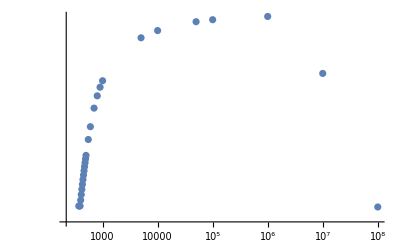

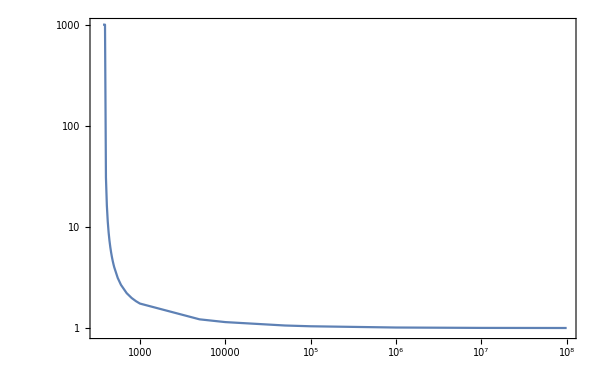

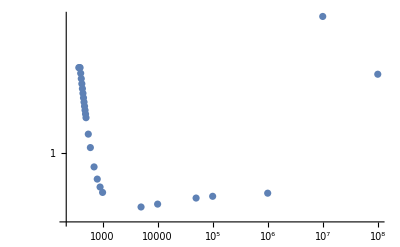

```mathematica
ListLogLogPlot[{nlist,listTransizione[[All,2]]}ᵀ]
ListLogLogPlot[{nlist,listTransizione[[All,3]]}ᵀ,Joined->True,PlotRangePadding->0.1, Frame->True,BaseStyle->{FontFamily->"Times",FontSize->20},FrameTicksStyle->Directive[Black,Thick],GridLines->Automatic,FrameLabel->{MaTeX["n",Magnification->2.5],MaTeX["\\text{optimal } a",Magnification->2.5]},ImageSize->600]
ListLogLogPlot[{nlist,listTransizione[[All,4]]}ᵀ]
```

```mathematica
(*rate con bound ottimizzato anche su sigma*)
rnBq[a_,η_,α_,n_,ϵ_,q_]:=bYEq[a,η,α,q]-g[ϵ]/(n(a-1))-h[1/2 Erfc[√(2η) α]]
rateBoptVSn[η_,n_]:=Module[{nmax,lp},
nmax=NMaximize[{rnBq[a,η,α,n,10^-8,q],10^-8<q<1,1<a<2,0<α<2},{q,a,α}];
lp={q,a,α}/.nmax[[2]];
Flatten@Join[{nmax[[1]]},{lp}]
]
```

```mathematica
(*Rate con Von neumann ottimizzato*)
δ[ϵ_]:=4Log2[2+√2](Log2[2/ϵ^2])^(1/2) (*fattore aep per d=2*)
rnAEP[η_,α_,n_,ϵ_]:=Neumann[α,η]-δ[ϵ]/n^(1/2)-h[1/2 Erfc[√(2η) α]]+g2/n
rateAEPVSn[η_,n_]:=Module[{nmax,lp},
nmax=NMaximize[{rnAEP[η,α,n,10^-8],0<α<2},α];
lp=α/.nmax[[2]];
Flatten@Join[{nmax[[1]]},{lp}]
]
```

```mathematica
(*Rate con min entropy*)
rnMin[η_,α_]:=HminDownAn[α,η]-h[1/2 Erfc[√(2η) α]]
rateMinVSn[η_,n_]:=Module[{nmax,lp},
nmax=NMaximize[{rnMin[η,α],0<α<2},α];
lp=α/.nmax[[2]];
Flatten@Join[{nmax[[1]]},{lp}]
]
```

```mathematica
(*min up*)
rnMinq[η_,α_,q_]:=Hminq[η,α,q]-h[1/2 Erfc[√(2η) α]]
rateMinUpVSn[η_,n_]:=Module[{nmax,lp},
nmax=NMaximize[{rnMinq[η,α,q],10^-8<q<1,0<α<2},{q,α}];
lp={q,α}/.nmax[[2]];
Flatten@Join[{nmax[[1]]},{lp}]
]
```

```mathematica
rateMinUpVSn[0.9,10^8]
rateMinVSn[0.9,10^8]
```

{0.192583,0.741871,1.12122}

{0.00735404,1.85292}

{0.999891,2.28555×10^-9}

```mathematica
rateMinVSn[0.9,10^8]
```

{0.00735404,1.85292}

```mathematica
rateAEPVSn[0.9,10^8]
```

{0.445659,0.949527}

```mathematica
rateVSn[0.9,10^8]
```

{-51.7008,0.917352,1.00128,0.949328}

```mathematica
rateBVSn[0.9,10^8]
```

{-51.7008,1.00127,0.94933}

```mathematica
rateVSn[0.9,10^8]
```

{0.450027,0.917352,1.00128,0.949328}

```mathematica
(*Lista rate AEP*)
RateListAEP=Table[{10^x,rateAEPVSn[0.9,10^x]},{x,Log10[100],Log10[1000000000],0.4}]
```

{{100.,{-5.28518,0.949527}},{251.189,{-3.0469,0.949527}},{630.957,{-1.70773,0.949527}},{1584.89,{-0.891867,0.949527}},{3981.07,{-0.388676,0.949527}},{10000.,{-0.075796,0.949527}},{25118.9,{0.119782,0.949527}},{63095.7,{0.242453,0.949527}},{158489.,{0.319562,0.949527}},{398107.,{0.368098,0.949527}},{1.×10^6,{0.398676,0.949527}},{2.51189×10^6,{0.417952,0.949527}},{6.30957×10^6,{0.430106,0.949527}},{1.58489×10^7,{0.437772,0.949527}},{3.98107×10^7,{0.442608,0.949527}},{1.×10^8,{0.445659,0.949527}},{2.51189×10^8,{0.447584,0.949527}},{6.30957×10^8,{0.448798,0.949527}}}

```mathematica
ListAEP1={RateListAEP[[All,1]],RateListAEP[[All,2,1]]}ᵀ
```

{{100.,-5.28518},{251.189,-3.0469},{630.957,-1.70773},{1584.89,-0.891867},{3981.07,-0.388676},{10000.,-0.075796},{25118.9,0.119782},{63095.7,0.242453},{158489.,0.319562},{398107.,0.368098},{1.×10^6,0.398676},{2.51189×10^6,0.417952},{6.30957×10^6,0.430106},{1.58489×10^7,0.437772},{3.98107×10^7,0.442608},{1.×10^8,0.445659},{2.51189×10^8,0.447584},{6.30957×10^8,0.448798}}

```mathematica
ListAEPconst = {{100.,-4.763676059415289},{251.18864315095797,-2.8392846071772717},{630.957344480193,-1.6250756867327896},{1584.893192461114,-0.8589616506449759},{3981.0717055349733,-0.37557637286600654},{10000.,-0.07058088163776755},{25118.864315095823,0.1218582635860338},{63095.7344480193,0.24327915563048225},{158489.3192461114,0.31989055923926324},{398107.17055349774,0.3682290870171604},{1.*^6,0.39872863613998455},{2.5118864315095823*^6,0.4179725506623644},{6.309573444801942*^6,0.4301146398668092},{1.5848931924611142*^7,0.43777578022768726},{3.9810717055349775*^7,0.44260963300547707},{1.*^8,0.4456595879177594},{2.511886431509582*^8,0.4475839793699975},{6.309573444801943*^8,0.4487981882904418}};
```

```mathematica
(*Lista rate SandUp*)
RateListSand=Table[{10^x,rateVSn[0.9,10^x]},{x,Log10[100],Log10[1000000000],0.4}]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::munfl: 1/2^1214.33 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2^1215.33 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.042228^1215.33 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NMaximize::nnum: The function value Indeterminate is not a number at {a,q,α} = {1215.33,0.741908,1.12046}.

{{100.,{-0.329971,0.742839,432.857,1.10568}},{251.189,{-0.0151215,0.741407,890.509,1.12261}},{630.957,{0.125854,0.816385,2.48903,0.997859}},{1584.89,{0.239765,0.87159,1.4881,0.933032}},{3981.07,{0.316836,0.8914,1.25433,0.929353}},{10000.,{0.366159,0.901745,1.14609,0.93382}},{25118.9,{0.397399,0.907775,1.08745,0.938572}},{63095.7,{0.417131,0.911437,1.05349,0.942226}},{158489.,{0.429584,0.913701,1.03312,0.944771}},{398107.,{0.437442,0.915113,1.02065,0.946468}},{1.×10^6,{0.442399,0.915998,1.01294,0.947574}},{2.51189×10^6,{0.445527,0.916554,1.00813,0.948286}},{6.30957×10^6,{0.4475,0.916904,1.00511,0.94874}},{1.58489×10^7,{0.448745,0.917125,1.00322,0.949029}},{3.98107×10^7,{0.449531,0.917264,1.00203,0.949212}},{1.×10^8,{0.450027,0.917352,1.00128,0.949328}},{2.51189×10^8,{0.450339,0.917407,1.00081,0.949402}},{6.30957×10^8,{0.450537,0.917442,1.00051,0.949448}}}

```mathematica
{{100.,{0.1915375298226406,0.7428386419163757,432.8573510753755,1.1056791396892107}},{251.18864315095797,{0.1924947813913812,0.741406722593934,890.5087002700711,1.1226133470368873}},{630.957344480193,{0.20850725496272784,0.8163849292014395,2.4890332842560863,0.9978585297004077}},{1584.893192461114,{0.2726701529334137,0.8715899900283323,1.4880975456916834,0.9330319313756316}},{3981.0717055349733,{0.32993590166962394,0.8913999022142922,1.2543309104619083,0.9293530860622415}},{10000.,{0.37137375515891413,0.9017448769235926,1.1460900130759322,0.933819739935288}},{25118.864315095823,{0.39947475527327164,0.907774964751568,1.0874531038472988,0.9385718402669565}},{63095.7344480193,{0.4179573385270723,0.9114368609924869,1.053489013901047,0.9422255367248328}},{158489.3192461114,{0.42991311798783227,0.913700896551991,1.0331172968207272,0.9447707418907719}},{398107.17055349774,{0.4375725871286386,0.9151131143082448,1.0206533797111135,0.9464678116990045}},{1.*^6,{0.4424512423817884,0.9159981612577257,1.0129372232593052,0.9475739408238729}},{2.5118864315095823*^6,{0.44554765518465367,0.9165543529204643,1.0081258557529602,0.9482856561294024}},{6.309573444801942*^6,{0.44750858464995374,0.9169043979139352,1.0051124883894689,0.948740195806384}},{1.5848931924611142*^7,{0.44874871982483655,0.9171249223525083,1.0032199744950807,0.9490291521167886}},{3.9810717055349775*^7,{0.4495323347143805,0.9172639608731116,1.0020293941151197,0.9492122900083948}},{1.*^8,{0.4500272168691738,0.9173515798731371,1.0012795704782347,0.9493282235974262}},{2.511886431509582*^8,{0.4503396473100616,0.917406853411296,1.000806969304469,0.9494008855881606}},{6.309573444801943*^8,{0.4505368495980422,0.9174417447554947,1.0005090621903658,0.9494477560473865}}}
```

```mathematica
ListSandconst={{100.,0.1915375298226406},{251.18864315095797,0.1924947813913812},{630.957344480193,0.20850725496272784},{1584.893192461114,0.2726701529334137},{3981.0717055349733,0.32993590166962394},{10000.,0.37137375515891413},{25118.864315095823,0.39947475527327164},{63095.7344480193,0.4179573385270723},{158489.3192461114,0.42991311798783227},{398107.17055349774,0.4375725871286386},{1.*^6,0.4424512423817884},{2.5118864315095823*^6,0.44554765518465367},{6.309573444801942*^6,0.44750858464995374},{1.5848931924611142*^7,0.44874871982483655},{3.9810717055349775*^7,0.4495323347143805},{1.*^8,0.4500272168691738},{2.511886431509582*^8,0.4503396473100616},{6.309573444801943*^8,0.4505368495980422}}
```

```mathematica
ListSand1={RateListSand[[All,1]],RateListSand[[All,2,1]]}ᵀ
```

{{100.,-0.329971},{251.189,-0.0151215},{630.957,0.125854},{1584.89,0.239765},{3981.07,0.316836},{10000.,0.366159},{25118.9,0.397399},{63095.7,0.417131},{158489.,0.429584},{398107.,0.437442},{1.×10^6,0.442399},{2.51189×10^6,0.445527},{6.30957×10^6,0.4475},{1.58489×10^7,0.448745},{3.98107×10^7,0.449531},{1.×10^8,0.450027},{2.51189×10^8,0.450339},{6.30957×10^8,0.450537}}

```mathematica
RateListSand[[All,2,1]]
```

{0.191538,0.192495,0.208507,0.27267,0.329936,0.371374,0.399475,0.417957,0.429913,0.437573,0.442451,0.445548,0.447509,0.448749,0.449532,0.450027,0.45034,0.450537}

```mathematica
(*Lista rate Bound*)
RateListBound=Table[{10^x,rateBVSn[0.9,10^x]},{x,Log10[100],Log10[1000000000],0.4}]
```

{{100.,{-2.63195,1.2839,0.899068}},{251.189,{-1.06331,1.23017,0.910553}},{630.957,{-0.315778,1.18224,0.919292}},{1584.89,{0.0504002,1.14081,0.926461}},{3981.07,{0.235065,1.10611,0.932323}},{10000.,{0.331038,1.07796,0.937001}},{25118.9,{0.38246,1.05584,0.940625}},{63095.7,{0.41085,1.03902,0.943345}},{158489.,{0.426975,1.02665,0.945326}},{398107.,{0.436369,1.01783,0.946726}},{1.×10^6,{0.441962,1.01174,0.947688}},{2.51189×10^6,{0.44535,1.00763,0.948335}},{6.30957×10^6,{0.447429,1.00491,0.948761}},{1.58489×10^7,{0.448717,1.00314,0.949038}},{3.98107×10^7,{0.44952,1.002,0.949216}},{1.×10^8,{0.450022,1.00127,0.94933}},{2.51189×10^8,{0.450338,1.0008,0.949402}},{6.30957×10^8,{0.450536,1.00051,0.949448}}}

```mathematica
RateListBoundOpt=Table[{10^x,rateBoptVSn[0.9,10^x]},{x,Log10[100],Log10[1000000000],0.4}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

NMaximize::nnum: The function value Indeterminate is not a number at {a,q,α} = {1.,0.036818,1.05443}.

{{100.,{-2.04224,0.77122,1.28783,0.953327}},{251.189,{-0.806222,0.74686,1.23415,0.95533}},{630.957,{-0.195839,0.721006,1.18665,0.956311}},{1584.89,{0.11165,0.697225,1.14593,0.956198}},{3981.07,{0.26952,0.677697,1.11201,0.955397}},{10000.,{0.352066,0.662947,1.08444,0.954325}},{25118.9,{0.396008,0.652417,1.06253,0.953254}},{63095.7,{0.419824,0.645158,1.04547,0.952315}},{158489.,{0.43297,0.640247,1.03246,0.951551}},{398107.,{0.440363,0.636956,1.02274,0.950959}},{1.×10^6,{0.444601,0.634762,1.01563,0.950517}},{2.51189×10^6,{0.447077,0.633306,1.01055,0.950198}},{6.30957×10^6,{0.448548,0.632348,1.007,0.949973}},{1.58489×10^7,{0.441328,0.0605254,1.00593,1.02697}},{3.98107×10^7,{0.449979,0.631312,1.00297,0.949717}},{1.×10^8,{0.450315,0.63105,1.00191,0.949649}},{2.51189×10^8,{0.450523,0.630882,1.00122,0.949605}},{6.30957×10^8,{0.450654,0.630775,1.00077,0.949576}}}

```mathematica
ListBound1={RateListBound[[All,1]],RateListBound[[All,2,1]]}ᵀ
```

{{100.,-2.63195},{251.189,-1.06331},{630.957,-0.315778},{1584.89,0.0504002},{3981.07,0.235065},{10000.,0.331038},{25118.9,0.38246},{63095.7,0.41085},{158489.,0.426975},{398107.,0.436369},{1.×10^6,0.441962},{2.51189×10^6,0.44535},{6.30957×10^6,0.447429},{1.58489×10^7,0.448717},{3.98107×10^7,0.44952},{1.×10^8,0.450022},{2.51189×10^8,0.450338},{6.30957×10^8,0.450536}}

```mathematica
ListBoundConst={{100.,-2.110446233702468},{251.18864315095797,-0.8556977950589569},{630.957344480193,-0.23312472809998785},{1584.893192461114,0.0833052036496782},{3981.0717055349733,0.24816421372938316},{10000.,0.33625290598130264},{25118.864315095823,0.3845364760577198},{63095.7344480193,0.4116769199485461},{158489.3192461114,0.42730385260571924},{398107.17055349774,0.4365002700959192},{1.*^6,0.4420145499145217},{2.5118864315095823*^6,0.4453710665324208},{6.309573444801942*^6,0.4474375431351518},{1.5848931924611142*^7,0.4487202423448103},{3.9810717055349775*^7,0.44952094694453915},{1.*^8,0.4500226703162984},{2.511886431509582*^8,0.4503378339855708},{6.309573444801943*^8,0.4505361268622134}}
```

```mathematica
ListBoundOpt1={RateListBoundOpt[[All,1]],RateListBoundOpt[[All,2,1]]}ᵀ
```

{{100.,-2.04224},{251.189,-0.806222},{630.957,-0.195839},{1584.89,0.11165},{3981.07,0.26952},{10000.,0.352066},{25118.9,0.396008},{63095.7,0.419824},{158489.,0.43297},{398107.,0.440363},{1.×10^6,0.444601},{2.51189×10^6,0.447077},{6.30957×10^6,0.448548},{1.58489×10^7,0.441328},{3.98107×10^7,0.449979},{1.×10^8,0.450315},{2.51189×10^8,0.450523},{6.30957×10^8,0.450654}}

```mathematica
RateListMin=Table[{10^x,rateMinUpVSn[0.9,10^x]},{x,Log10[100],Log10[1000000000],0.4}]
ListMin1={RateListMin[[All,1]],RateListMin[[All,2,1]]}ᵀ
```

{{100.,{0.192583,0.741871,1.12122}},{251.189,{0.192583,0.741871,1.12122}},{630.957,{0.192583,0.741871,1.12122}},{1584.89,{0.192583,0.741871,1.12122}},{3981.07,{0.192583,0.741871,1.12122}},{10000.,{0.192583,0.741871,1.12122}},{25118.9,{0.192583,0.741871,1.12122}},{63095.7,{0.192583,0.741871,1.12122}},{158489.,{0.192583,0.741871,1.12122}},{398107.,{0.192583,0.741871,1.12122}},{1.×10^6,{0.192583,0.741871,1.12122}},{2.51189×10^6,{0.192583,0.741871,1.12122}},{6.30957×10^6,{0.192583,0.741871,1.12122}},{1.58489×10^7,{0.192583,0.741871,1.12122}},{3.98107×10^7,{0.192583,0.741871,1.12122}},{1.×10^8,{0.192583,0.741871,1.12122}},{2.51189×10^8,{0.192583,0.741871,1.12122}},{6.30957×10^8,{0.192583,0.741871,1.12122}}}

{{100.,0.192583},{251.189,0.192583},{630.957,0.192583},{1584.89,0.192583},{3981.07,0.192583},{10000.,0.192583},{25118.9,0.192583},{63095.7,0.192583},{158489.,0.192583},{398107.,0.192583},{1.×10^6,0.192583},{2.51189×10^6,0.192583},{6.30957×10^6,0.192583},{1.58489×10^7,0.192583},{3.98107×10^7,0.192583},{1.×10^8,0.192583},{2.51189×10^8,0.192583},{6.30957×10^8,0.192583}}

```mathematica
ListMinConst={{100.,0.1925827490423872},{251.18864315095797,0.1925827490423872},{630.957344480193,0.1925827490423872},{1584.893192461114,0.1925827490423872},{3981.0717055349733,0.1925827490423872},{10000.,0.1925827490423872},{25118.864315095823,0.1925827490423872},{63095.7344480193,0.1925827490423872},{158489.3192461114,0.1925827490423872},{398107.17055349774,0.1925827490423872},{1.*^6,0.1925827490423872},{2.5118864315095823*^6,0.1925827490423872},{6.309573444801942*^6,0.1925827490423872},{1.5848931924611142*^7,0.1925827490423872},{3.9810717055349775*^7,0.1925827490423872},{1.*^8,0.1925827490423872},{2.511886431509582*^8,0.1925827490423872},{6.309573444801943*^8,0.1925827490423872}}
```

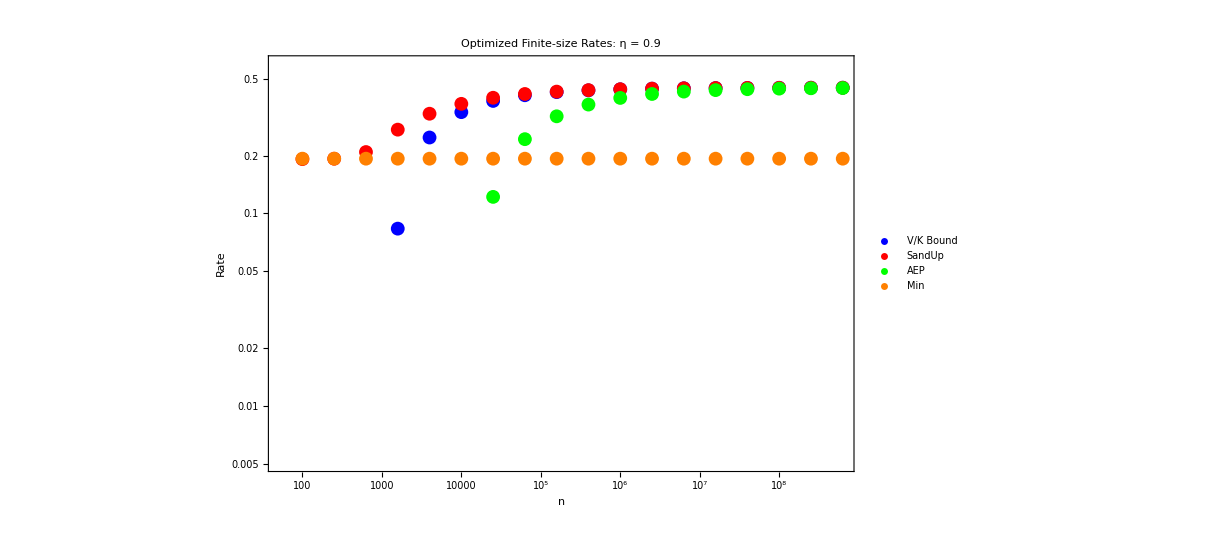

```mathematica
ListPlot[{ListBound1,ListSand1,ListAEP1,ListMin1},PlotStyle->{Blue,Red,Green,Orange},ScalingFunctions->{"Log","Log"},PlotRange->{Automatic,{0.005,0.6}},PlotLegends->{"V/K Bound","SandUp","AEP","Min"},Frame->True,FrameLabel->{"n","Rate"},GridLines->Automatic,PlotLabel->"Optimized Finite-size Rates: η = 0.9"]
```

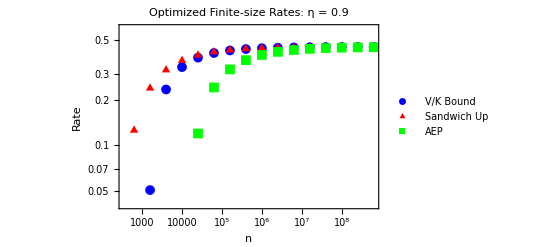

```mathematica
RateBPSK=ListPlot[{ListBound1,ListSand1,ListAEP1},PlotStyle->{Blue,Red,Green},PlotMarkers->{{"●",10},(*cerchio pieno*){"▲",10},(*triangolo pieno*){"■",10},(*quadrato pieno*){"◆",10}  (*rombo pieno*)},ScalingFunctions->{"Log","Log"},PlotRange->{Automatic,{0.04,0.6}},PlotLegends->Placed[LineLegend[{Blue,Red,Green},{Style["V/K Bound",FontSize->18],Style["Sandwich Up",FontSize->18],Style["AEP",FontSize->18]},
LegendMarkerSize->15,Spacings->1],Right],
Frame->True,FrameLabel->{Style["n",FontSize->14],Style["Rate",FontSize->14]},
FrameTicksStyle->Directive[Black,FontSize->12],GridLines->Automatic,PlotLabel->Style["Optimized Finite-size Rates: η = 0.9",FontSize->14]]
```

```mathematica
Export["/Users/Gabriele/Documents/Wolfram/PskPureLoss/grafici/RateBPSK.png",RateBPSK,ImageResolution->300]
```

/Users/Gabriele/Documents/Wolfram/PskPureLoss/grafici/RateBPSK.png

Syntax::stresc: Unknown string escape \e.

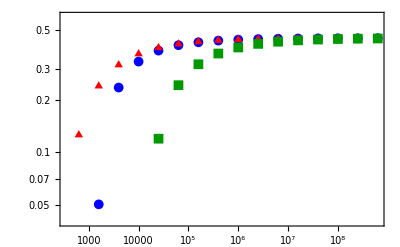

```mathematica
(*Assumo che MaTeX sia già installato*)Needs["MaTeX`"];

(*(opzionale) pacchetti LaTeX utili*)
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amsmath}"}];

(*Voci della legenda con MaTeX*)
legBound=MaTeX["r_{\epsilon''}^B",Magnification->1.2];
legSand=MaTeX["r_{\epsilon''}^S",Magnification->1.2];
legAEP=MaTeX["r_{\epsilon''}^{AEP}",Magnification->1.2];

(*Etichette degli assi e titolo con MaTeX*)
xLab=MaTeX["n",Magnification->1.1];
yLab=MaTeX["\\text{Rate}",Magnification->1.1];
tit=MaTeX["\\text{BPSK Optimized Finite-size Rates:}\\;\\eta=0.9",Magnification->1.1];

RateBPSK=ListPlot[{ListBound1,ListSand1,ListAEP1},PlotStyle->{Blue,Red,Darker[Green,0.4]},PlotMarkers->{{"●",10},(*Bound:cerchio pieno*){"▲",10},(*Sandwich:triangolo pieno*){"■",10}       (*AEP:quadrato pieno*)},ScalingFunctions->{"Log","Log"},PlotRange->{Automatic,{0.04,0.6}},PlotLegends->Placed[LineLegend[{Blue,Red,Darker[Green,0.4]},{legBound,legSand,legAEP},LegendMarkerSize->15,Spacings->1],Right],Frame->True,FrameLabel->{xLab,yLab},FrameTicksStyle->Directive[Black,FontSize->12],GridLines->Automatic,PlotLabel->tit]
```

```mathematica
Export["/Users/Gabriele/Documents/Wolfram/PskPureLoss/grafici/RateBPSK2.png",RateBPSK,ImageResolution->300]
```

/Users/Gabriele/Documents/Wolfram/PskPureLoss/grafici/RateBPSK2.png

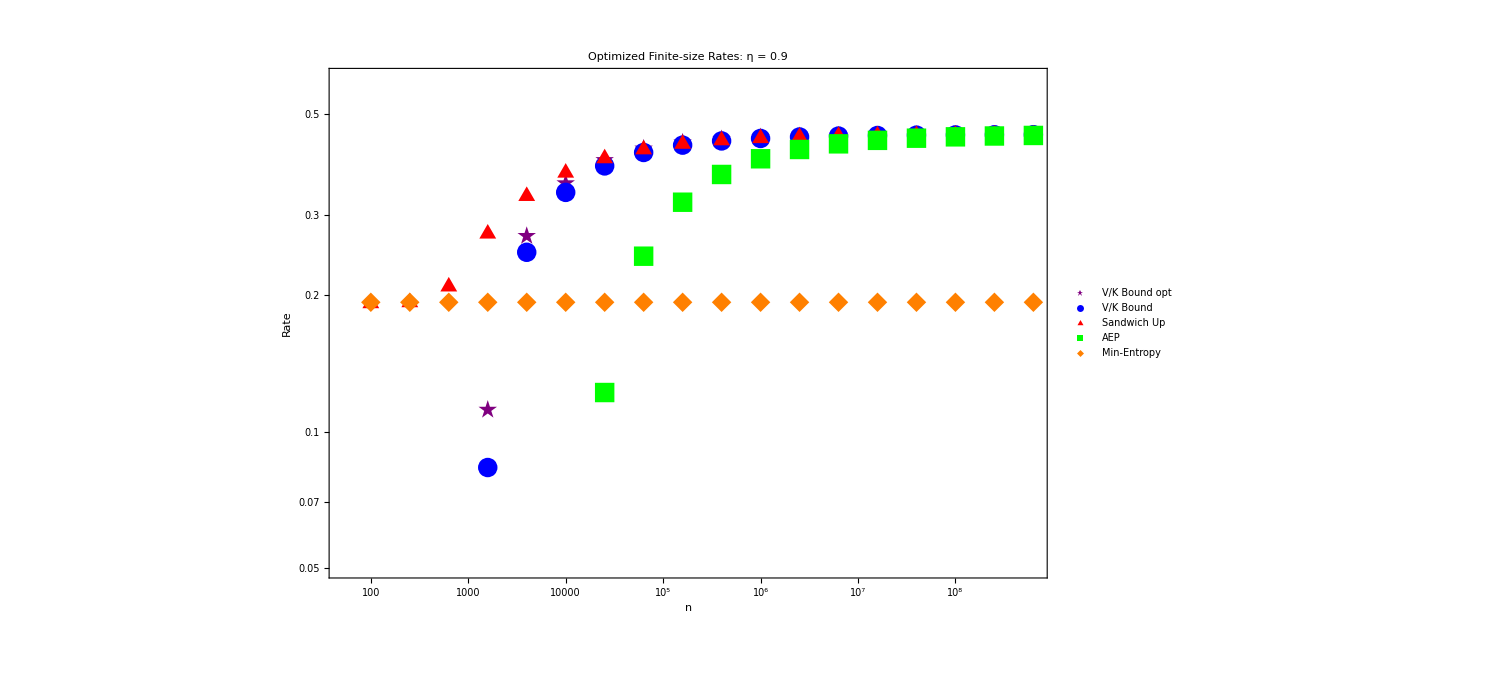

```mathematica
ListPlot[{ListBoundOpt1,ListBound1,ListSand1,ListAEP1,ListMin1},PlotStyle->{Purple,Blue,Red,Green,Orange},PlotMarkers->{{"★",20},(*V/K Bound opt*){"●",20},(*V/K Bound*){"▲",20},(*Sandwich Up*){"■",20},(*AEP*){"◆",20}        (*Min-Entropy*)},ScalingFunctions->{"Log","Log"},PlotRange->{Automatic,{0.05,0.6}},PlotLegends->Placed[LineLegend[{Purple,Blue,Red,Green,Orange},{Style["V/K Bound opt",FontSize->18],Style["V/K Bound",FontSize->18],Style["Sandwich Up",FontSize->18],Style["AEP",FontSize->18],Style["Min-Entropy",FontSize->18]},LegendMarkerSize->15,Spacings->1],Right],Frame->True,FrameLabel->{Style["n",FontSize->14],Style["Rate",FontSize->14]},FrameTicksStyle->Directive[Black,FontSize->12],GridLines->Automatic,PlotLabel->Style["Optimized Finite-size Rates: η = 0.9",FontSize->14]]
```

```mathematica
nmax=NMaximize[{rn[a,0.9,α,10^8,10^-8,q],0<q<1,a>1&&α>0},{q,a,α}]
```

{0.450027,{q→0.917352,a→1.00128,α→0.949328}}

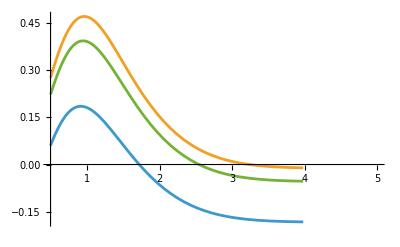

```mathematica
Plot[{rnB[1.2,.9,α,10^5,10^-8],rnB[.9,.9,α,10^5,10^-8],rnB[1.01,.9,α,10^5,10^-8]},{α,0.5,5}]
```

```mathematica
rateVSn[0.8,10^5]
```

{0.266515,0.883158,1.04277,0.795039}

```mathematica
rateVSn[0.8,10^5]
```

{0.266515,0.883158,1.04277,0.795039}

```mathematica
RateListSand=Table[{10^x,rateVSn[0.9,10^x][[1]]},{x,2,8,1}];
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
listaαn=Map[Flatten,{ListrateVSn[[All,2,{3,4}]],ListrateVSn[[All,1]]}ᵀ]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

{Symbol[],Symbol[]}

```mathematica
ListrateVSn[[All,2,{3,4}]]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Symbol[]

```mathematica
ListrateVSn1=Table[{10^x,rateVSn[0.8,10^x][[1]]},{x,2,8,1}];
```

General::munfl: 1/2^1110.47 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2^1111.47 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NMaximize::nnum: The function value Indeterminate is not a number at {a,q,α} = {1111.47,0.999812,0.0192152}.

```mathematica
ListrateVSn2=Table[{10^x,rateVSn[0.7,10^x][[1]]},{x,2,8,1}];
```

General::munfl: 1/2^1402.09 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2^1403.09 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.547926^1403.09 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NMaximize::nnum: The function value Indeterminate is not a number at {a,q,α} = {1403.09,0.999394,0.0236032}.

```mathematica
ListrateVSn3=Table[{10^x,rateVSn[0.6,10^x][[1]]},{x,2,8,1}];
```

Power::infy: Infinite expression 1/0.^0.998638 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression -0.999997+ComplexInfinity+ComplexInfinity encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

Infinity::indet: Indeterminate expression -0.999997+ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NMaximize::nnum: The function value Indeterminate is not a number at {a,q,α} = {734.418,1.,0.0029556}.

General::munfl: 1/2^1145.43 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2^1146.43 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-244981.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NMaximize::nnum: The function value Indeterminate is not a number at {a,q,α} = {1146.43,0.501519,553.377}.

```mathematica
ListLogLogPlot[{ListrateVSn,ListrateVSn1,ListrateVSn2,ListrateVSn3}]
```

ListLogLogPlot::lpn: {{},{{4.605170185988091,-7.31438+3.14159 ⅈ},{6.907755278982137,-2.57026},{9.210340371976183,-1.54217},{«60»,-«19»},{13.815510557964274,-1.25863},{16.11809565095832,-1.239},{18.420680743952365,-1.23284}},{«1»},{{4.605170185988091,-7.15281+3.14159 ⅈ},{6.907755278982137,-9.82463+3.14159 ⅈ},{9.210340371976183,-2.54382},{11.512925464970228,-2.09432},{13.815510557964274,-1.97808},{16.11809565095832,-1.94324},{18.420680743952365,-1.9324}}} is not a list of numbers or pairs of numbers.

ListLogLogPlot[{ListrateVSn,{{100,-0.000665893},{1000,0.0765156},{10000,0.213917},{100000,0.266515},{1000000,0.284042},{10000000,0.289674},{100000000,0.291464}},{{100,-0.000899875},{1000,0.00571661},{10000,0.129909},{100000,0.179258},{1000000,0.195784},{10000000,0.201101},{100000000,0.202791}},{{100,-0.000782661},{1000,-0.0000541024},{10000,0.0785656},{100000,0.123154},{1000000,0.138334},{10000000,0.143239},{100000000,0.1448}}}]

```mathematica
ListrateBVSn=Table[{10^x,rateBVSn[0.9,10^x]},{x,2,8,1}];
```

```mathematica
{ListrateBVSn[[All,1]],ListrateBVSn[[All,2,1]]}ᵀ
```

{{100,-2.11045},{1000,-0.0489046},{10000,0.336253},{100000,0.420539},{1000000,0.442015},{10000000,0.448154},{100000000,0.450023}}

```mathematica
ListrateBVSn1=Table[{10^x,rateBVSn[0.8,10^x]},{x,2,8,1}];
```

```mathematica
ListrateBVSn2=Table[{10^x,rateBVSn[0.7,10^x]},{x,2,8,1}];
```

```mathematica
ListrateBVSn3=Table[{10^x,rateBVSn[0.6,10^x]},{x,2,8,1}];
```

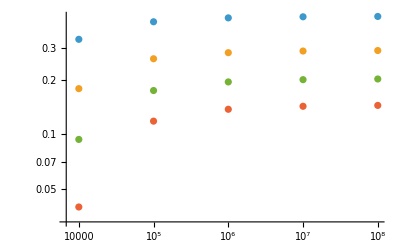

```mathematica
ListLogLogPlot[{{ListrateBVSn[[All,1]],ListrateBVSn[[All,2,1]]}ᵀ,{ListrateBVSn1[[All,1]],ListrateBVSn1[[All,2,1]]}ᵀ,{ListrateBVSn2[[All,1]],ListrateBVSn2[[All,2,1]]}ᵀ,{ListrateBVSn3[[All,1]],ListrateBVSn3[[All,2,1]]}ᵀ}]
```

```mathematica
ListLogLogPlot[{ListrateVSn}]
```

-Graphics-

```mathematica
ListLogLogPlot[{ListrateVSn,{ListrateBVSn[[All,1]],ListrateBVSn[[All,2,1]]}ᵀ}]
```

ListLogLogPlot::lpn: {{},{{4.605170185988091,0.746899+3.14159 ⅈ},{6.907755278982137,-3.01788+3.14159 ⅈ},{9.210340371976183,-1.08989},{11.512925464970228,-0.866219},{13.815510557964274,-0.816412},{16.11809565095832,-0.802617},{18.420680743952365,-0.798457}}} is not a list of numbers or pairs of numbers.

ListLogLogPlot[{ListrateVSn,{{100,-2.11045},{1000,-0.0489046},{10000,0.336253},{100000,0.420539},{1000000,0.442015},{10000000,0.448154},{100000000,0.450023}}}]

```mathematica
rateVSn[0.9,10^3]
```

{0.239545,0.852834,1.74791,0.948527}

```mathematica
rateVSn[0.9,10^2]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{0.191538,0.742839,432.857,1.10568}

```mathematica
rateVSn[0.9,10^x/2]
```

NMaximize::nnum: The function value -0.249774+32.4805 2^(1-x) 5^-x is not a number at {a,q,α} = {2.66718,0.826558,1.07973}.

General::stop: Further output of NMaximize::nnum will be suppressed during this calculation.

ReplaceAll::reps: {q,a,α} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{-(2^(1-x) 5^-x Log[20000000000000000])/((-1+a) Log[2])+1/((1-a) Log[2])Log[2^(1-a) Re[-((1. 2^-a (1.-1. q)^(-0.5+0.5/a-(0.5 (1.-1. a))/a) q^(-0.5+0.5/a-(0.5 (1.-1. a))/a) (0.5 (1.-1. q)^((1.-1. a)/a)-0.5 ⅇ^(-0.2 α^2) (1.-1. q)^((1.-1. a)/a)+0.5 q^((1.-1. a)/a)+0.5 ⅇ^(-0.2 α^2) q^((1.-1. a)/a)-√((-0.5 (1.-1. q)^((1.-1. a)/a)+0.5 ⅇ^(-0.2 α^2) (1.-1. q)^((1.-1. a)/a)-0.5 q^((1.-1. a)/a)-0.5 ⅇ^(-0.2 α^2) q^((1.-1. a)/a))^2-4 (0.25 (1.-1. q)^((1.-1. a)/a) q^((1.-1. a)/a)-0.25 ⅇ^(-0.4 α^2) (1.-1. q)^((1.-1. a)/a) q^((1.-1. a)/a)-0.25 (1.-1. q)^((1. (1.-1. a))/a) q^((1. (1.-1. a))/a) Erf[1.34164 α]^2+0.25 ⅇ^(-(2 α^2)/5) (1.-1. q)^((1. (1.-1. a))/a) q^((1. (1.-1. a))/a) Erf[1.34164 α]^2)))^a (0.5 (1.-1. ⅇ^(-0.2 α^2)) (1.-1. q)^((1.-1. a)/a)+1/2 (-0.5 (1.-1. q)^((1.-1. a)/a)+0.5 ⅇ^(-0.2 α^2) (1.-1. q)^((1.-1. a)/a)-0.5 q^((1.-1. a)/a)-0.5 ⅇ^(-0.2 α^2) q^((1.-1. a)/a)-√((-0.5 (1.-1. q)^((1.-1. a)/a)+0.5 ⅇ^(-0.2 α^2) (1.-1. q)^((1.-1. a)/a)-0.5 q^((1.-1. a)/a)-0.5 ⅇ^(-0.2 α^2) q^((1.-1. a)/a))^2-4 (0.25 (1.-1. q)^((1.-1. a)/a) q^((1.-1. a)/a)-0.25 ⅇ^(-0.4 α^2) (1.-1. q)^((1.-1. a)/a) q^((1.-1. a)/a)-0.25 (1.-1. q)^((1. (1.-1. a))/a) q^((1. (1.-1. a))/a) Erf[1.34164 α]^2+0.25 ⅇ^(-(2 α^2)/5) (1.-1. q)^((1. (1.-1. a))/a) q^((1. (1.-1. a))/a) Erf[1.34164 α]^2)))))/(√((-0.5 (1.-1. q)^(-1.+1./a)+0.5 ⅇ^(-0.2 α^2) (1.-1. q)^(-1.+1./a)-0.5 q^(-1.+1./a)-0.5 ⅇ^(-0.2 α^2) q^(-1.+1./a))^2-4 (0.25 (1.-1. q)^(-1.+1./a) q^(-1.+1./a)-0.25 ⅇ^(-0.4 α^2) (1.-1. q)^(-1.+1./a) q^(-1.+1./a)-0.25 (1.-1. q)^(-1.+1./a) q^(-1.+1./a) Erf[1.34164 α]^2+0.25 ⅇ^(-(2 α^2)/5) (1.-1. q)^(-1.+1./a) q^(-1.+1./a) Erf[1.34164 α]^2))))-(1. 2^-a (1.-1. q)^(-0.5+0.5/a-(0.5 (1.-1. a))/a) q^(-0.5+0.5/a-(0.5 (1.-1. a))/a) (0.5 (1.-1. q)^((1.-1. a)/a)-0.5 ⅇ^(-0.2 α^2) (1.-1. q)^((1.-1. a)/a)+0.5 q^((1.-1. a)/a)+0.5 ⅇ^(-0.2 α^2) q^((1.-1. a)/a)+√((-0.5 (1.-1. q)^((1.-1. a)/a)+0.5 ⅇ^(-0.2 α^2) (1.-1. q)^((1.-1. a)/a)-0.5 q^((1.-1. a)/a)-0.5 ⅇ^(-0.2 α^2) q^((1.-1. a)/a))^2-4 (0.25 (1.-1. q)^((1.-1. a)/a) q^((1.-1. a)/a)-0.25 ⅇ^(-0.4 α^2) (1.-1. q)^((1.-1. a)/a) q^((1.-1. a)/a)-0.25 (1.-1. q)^((1. (1.-1. a))/a) q^((1. (1.-1. a))/a) Erf[1.34164 α]^2+0.25 ⅇ^(-(2 α^2)/5) (1.-1. q)^((1. (1.-1. a))/a) q^((1. (1.-1. a))/a) Erf[1.34164 α]^2)))^a (0.5 (1.-1. ⅇ^(-0.2 α^2)) (1.-1. q)^((1.-1. a)/a)+1/2 (-0.5 (1.-1. q)^((1.-1. a)/a)+0.5 ⅇ^(-0.2 α^2) (1.-1. q)^((1.-1. a)/a)-0.5 q^((1.-1. a)/a)-0.5 ⅇ^(-0.2 α^2) q^((1.-1. a)/a)-√((-0.5 (1.-1. q)^((1.-1. a)/a)+0.5 ⅇ^(-0.2 α^2) (1.-1. q)^((1.-1. a)/a)-0.5 q^((1.-1. a)/a)-0.5 ⅇ^(-0.2 α^2) q^((1.-1. a)/a))^2-4 (0.25 (1.-1. q)^((1.-1. a)/a) q^((1.-1. a)/a)-0.25 ⅇ^(-0.4 α^2) (1.-1. q)^((1.-1. a)/a) q^((1.-1. a)/a)-0.25 (1.-1. q)^((1. (1.-1. a))/a) q^((1. (1.-1. a))/a) Erf[1.34164 α]^2+0.25 ⅇ^(-(2 α^2)/5) (1.-1. q)^((1. (1.-1. a))/a) q^((1. (1.-1. a))/a) Erf[1.34164 α]^2)))))/(√((-0.5 (1.-1. q)^(-1.+1./a)+0.5 ⅇ^(-0.2 α^2) (1.-1. q)^(-1.+1./a)-0.5 q^(-1.+1./a)-0.5 ⅇ^(-0.2 α^2) q^(-1.+1./a))^2-4 (0.25 (1.-1. q)^(-1.+1./a) q^(-1.+1./a)-0.25 ⅇ^(-0.4 α^2) (1.-1. q)^(-1.+1./a) q^(-1.+1./a)-0.25 (1.-1. q)^(-1.+1./a) q^(-1.+1./a) Erf[1.34164 α]^2+0.25 ⅇ^(-(2 α^2)/5) (1.-1. q)^(-1.+1./a) q^(-1.+1./a) Erf[1.34164 α]^2)))+(1. 2^-a (1.-1. q)^(-0.5+0.5/a-(0.5 (1.-1. a))/a) q^(-0.5+0.5/a-(0.5 (1.-1. a))/a) (0.5 (1.-1. q)^((1.-1. a)/a)-0.5 ⅇ^(-0.2 α^2) (1.-1. q)^((1.-1. a)/a)+0.5 q^((1.-1. a)/a)+0.5 ⅇ^(-0.2 α^2) q^((1.-1. a)/a)-√((-0.5 (1.-1. q)^((1.-1. a)/a)+0.5 ⅇ^(-0.2 α^2) (1.-1. q)^((1.-1. a)/a)-0.5 q^((1.-1. a)/a)-0.5 ⅇ^(-0.2 α^2) q^((1.-1. a)/a))^2-4 (0.25 (1.-1. q)^((1.-1. a)/a) q^((1.-1. a)/a)-0.25 ⅇ^(-0.4 α^2) (1.-1. q)^((1.-1. a)/a) q^((1.-1. a)/a)-0.25 (1.-1. q)^((1. (1.-1. a))/a) q^((1. (1.-1. a))/a) Erf[1.34164 α]^2+0.25 ⅇ^(-(2 α^2)/5) (1.-1. q)^((1. (1.-1. a))/a) q^((1. (1.-1. a))/a) Erf[1.34164 α]^2)))^a (0.5 (1.-1. ⅇ^(-0.2 α^2)) (1.-1. q)^((1.-1. a)/a)+1/2 (-0.5 (1.-1. q)^((1.-1. a)/a)+0.5 ⅇ^(-0.2 α^2) (1.-1. q)^((1.-1. a)/a)-0.5 q^((1.-1. a)/a)-0.5 ⅇ^(-0.2 α^2) q^((1.-1. a)/a)+√((-0.5 (1.-1. q)^((1.-1. a)/a)+0.5 ⅇ^(-0.2 α^2) (1.-1. q)^((1.-1. a)/a)-0.5 q^((1.-1. a)/a)-0.5 ⅇ^(-0.2 α^2) q^((1.-1. a)/a))^2-4 (0.25 (1.-1. q)^((1.-1. a)/a) q^((1.-1. a)/a)-0.25 ⅇ^(-0.4 α^2) (1.-1. q)^((1.-1. a)/a) q^((1.-1. a)/a)-0.25 (1.-1. q)^((1. (1.-1. a))/a) q^((1. (1.-1. a))/a) Erf[1.34164 α]^2+0.25 ⅇ^(-(2 α^2)/5) (1.-1. q)^((1. (1.-1. a))/a) q^((1. (1.-1. a))/a) Erf[1.34164 α]^2)))))/(√((-0.5 (1.-1. q)^(-1.+1./a)+0.5 ⅇ^(-0.2 α^2) (1.-1. q)^(-1.+1./a)-0.5 q^(-1.+1./a)-0.5 ⅇ^(-0.2 α^2) q^(-1.+1./a))^2-4 (0.25 (1.-1. q)^(-1.+1./a) q^(-1.+1./a)-0.25 ⅇ^(-0.4 α^2) (1.-1. q)^(-1.+1./a) q^(-1.+1./a)-0.25 (1.-1. q)^(-1.+1./a) q^(-1.+1./a) Erf[1.34164 α]^2+0.25 ⅇ^(-(2 α^2)/5) (1.-1. q)^(-1.+1./a) q^(-1.+1./a) Erf[1.34164 α]^2)))+(1. 2^-a (1.-1. q)^(-0.5+0.5/a-(0.5 (1.-1. a))/a) q^(-0.5+0.5/a-(0.5 (1.-1. a))/a) (0.5 (1.-1. q)^((1.-1. a)/a)-0.5 ⅇ^(-0.2 α^2) (1.-1. q)^((1.-1. a)/a)+0.5 q^((1.-1. a)/a)+0.5 ⅇ^(-0.2 α^2) q^((1.-1. a)/a)+√((-0.5 (1.-1. q)^((1.-1. a)/a)+0.5 ⅇ^(-0.2 α^2) (1.-1. q)^((1.-1. a)/a)-0.5 q^((1.-1. a)/a)-0.5 ⅇ^(-0.2 α^2) q^((1.-1. a)/a))^2-4 (0.25 (1.-1. q)^((1.-1. a)/a) q^((1.-1. a)/a)-0.25 ⅇ^(-0.4 α^2) (1.-1. q)^((1.-1. a)/a) q^((1.-1. a)/a)-0.25 (1.-1. q)^((1. (1.-1. a))/a) q^((1. (1.-1. a))/a) Erf[1.34164 α]^2+0.25 ⅇ^(-(2 α^2)/5) (1.-1. q)^((1. (1.-1. a))/a) q^((1. (1.-1. a))/a) Erf[1.34164 α]^2)))^a (0.5 (1.-1. ⅇ^(-0.2 α^2)) (1.-1. q)^((1.-1. a)/a)+1/2 (-0.5 (1.-1. q)^((1.-1. a)/a)+0.5 ⅇ^(-0.2 α^2) (1.-1. q)^((1.-1. a)/a)-0.5 q^((1.-1. a)/a)-0.5 ⅇ^(-0.2 α^2) q^((1.-1. a)/a)+√((-0.5 (1.-1. q)^((1.-1. a)/a)+0.5 ⅇ^(-0.2 α^2) (1.-1. q)^((1.-1. a)/a)-0.5 q^((1.-1. a)/a)-0.5 ⅇ^(-0.2 α^2) q^((1.-1. a)/a))^2-4 (0.25 (1.-1. q)^((1.-1. a)/a) q^((1.-1. a)/a)-0.25 ⅇ^(-0.4 α^2) (1.-1. q)^((1.-1. a)/a) q^((1.-1. a)/a)-0.25 (1.-1. q)^((1. (1.-1. a))/a) q^((1. (1.-1. a))/a) Erf[1.34164 α]^2+0.25 ⅇ^(-(2 α^2)/5) (1.-1. q)^((1. (1.-1. a))/a) q^((1. (1.-1. a))/a) Erf[1.34164 α]^2)))))/(√((-0.5 (1.-1. q)^(-1.+1./a)+0.5 ⅇ^(-0.2 α^2) (1.-1. q)^(-1.+1./a)-0.5 q^(-1.+1./a)-0.5 ⅇ^(-0.2 α^2) q^(-1.+1./a))^2-4 (0.25 (1.-1. q)^(-1.+1./a) q^(-1.+1./a)-0.25 ⅇ^(-0.4 α^2) (1.-1. q)^(-1.+1./a) q^(-1.+1./a)-0.25 (1.-1. q)^(-1.+1./a) q^(-1.+1./a) Erf[1.34164 α]^2+0.25 ⅇ^(-(2 α^2)/5) (1.-1. q)^(-1.+1./a) q^(-1.+1./a) Erf[1.34164 α]^2)))]]-(Piecewise[{{-((1-1/2 Erfc[1.34164 α]) Log[1-1/2 Erfc[1.34164 α]])/Log[2]-(Erfc[1.34164 α] Log[1/2 Erfc[1.34164 α]])/(2 Log[2]), 0<1/2 Erfc[1.34164 α]<1}, {0, True}}]),1/100000000<q<1,a>100000001/100000000,α>0,{q,a,α}/.{q,a,α}}

```mathematica
listn=Flatten[Table[{10^k,5*10^k},{k,2,8}]];
```

```mathematica
list=Table[rateVSn[0.9,listn[[i]]],{i,Length[listn]}]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{{0.191538,0.742839,432.857,1.10568},{0.197395,0.78493,4.00292,1.04832},{0.239545,0.852834,1.74791,0.948527},{0.341625,0.894541,1.22046,0.93022},{0.371374,0.901745,1.14609,0.93382},{0.414012,0.910672,1.06048,0.941415},{0.424593,0.912703,1.04204,0.943622},{0.438993,0.915372,1.01839,0.946788},{0.442451,0.915998,1.01294,0.947574},{0.447095,0.916831,1.00575,0.948644},{0.448199,0.917027,1.00406,0.948901},{0.449677,0.91729,1.00181,0.949246},{0.450027,0.917352,1.00128,0.949328},{0.450495,0.917434,1.00057,0.949438}}

```mathematica
listn=Table[10^x,{x,2,8}];
```

```mathematica
ListLogLogPlot[{listn,list[[All,3]]}ᵀ,LabelStyle->{"n","a"}]
```

Transpose::nmtx: The first two levels of {{100,1000,10000,100000,1000000,10000000,100000000},{432.857,4.00292,1.74791,1.22046,1.14609,1.06048,1.04204,1.01839,1.01294,1.00575,1.00406,1.00181,1.00128,1.00057}} cannot be transposed.

Transpose::nmtx: The first two levels of {{100.,1000.,10000.,100000.,1.×10^6,1.×10^7,1.×10^8},{432.857,4.00292,1.74791,1.22046,1.14609,1.06048,1.04204,1.01839,1.01294,1.00575,1.00406,1.00181,1.00128,1.00057}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLogLogPlot::lpn: { is not a list of numbers or pairs of numbers.

ListLogLogPlot[Transpose[{{100,1000,10000,100000,1000000,10000000,100000000},{432.857,4.00292,1.74791,1.22046,1.14609,1.06048,1.04204,1.01839,1.01294,1.00575,1.00406,1.00181,1.00128,1.00057}}],LabelStyle→{n,a}]

## 2. QPSK only entropies and rate not optimized

## States Definition ρ_E, ρ_(E|y)and ρ_YE

```mathematica
(*fare riferimento file overleaf RenyiSumUp appendice C*)
(*coeff. di normalizzazione per la base ortonormale *)
Subscript[n, s_][α_,η_]:=1/(√(1+Exp[-2 α^2(1-η)]Cos[s π]+2 Exp[-α^2(1-η)]Cos[π/2 s+α^2(1-η)]))
h2[x_] := Piecewise[{{-x Log2[x] - (1 - x) Log2[1 - x], 0 < x < 1}}, 0]
a_⊙b_:= KroneckerProduct[a,b]
KetBra[psi_,phi_]:=Outer[Times,psi,Conjugate[phi]]
yB[i_] :=UnitVector[4,i+1]⊙UnitVector[4,i+1]
(*probabilità condizionate P_(+/-)*)
Subscript[m, sgn_][α_,η_]:=1/2(1+sgn Erf[(√η α)/(√2)])
(*matrice delle probabilità condizionate*)
P1[α_,η_]:=Table[RotateRight[{(Subscript[m, 1][α,η])^2,Subscript[m, 1][α,η]Subscript[m, -1][α,η],(Subscript[m, -1][α,η])^2,Subscript[m, 1][α,η]Subscript[m, -1][α,η]},i],{i,0,3}]
```

```mathematica
P[α_,η_]:=({{1/4 (1+Erf[(α √η)/(√2)])^2, 1/4 (1-Erf[(α √η)/(√2)]^2), 1/4 Erfc[(α √η)/(√2)]^2, 1/4 (1-Erf[(α √η)/(√2)]^2)}, {1/4 (1-Erf[(α √η)/(√2)]^2), 1/4 (1+Erf[(α √η)/(√2)])^2, 1/4 (1-Erf[(α √η)/(√2)]^2), 1/4 Erfc[(α √η)/(√2)]^2}, {1/4 Erfc[(α √η)/(√2)]^2, 1/4 (1-Erf[(α √η)/(√2)]^2), 1/4 (1+Erf[(α √η)/(√2)])^2, 1/4 (1-Erf[(α √η)/(√2)]^2)}, {1/4 (1-Erf[(α √η)/(√2)]^2), 1/4 Erfc[(α √η)/(√2)]^2, 1/4 (1-Erf[(α √η)/(√2)]^2), 1/4 (1+Erf[(α √η)/(√2)])^2}})
(*stato ridotto*)
ρE[α_,η_] :=1/4∑_(s=0)^3 1/(Subscript[n, s][α,η])^2 yB[s]

(*stati condizionali*)
Subscript[ρE, y_][α_,η_]:=∑_(s=0)^3 ∑_(s1=0)^3 (1/(4 Subscript[n, s][α,η]Subscript[n, s1][α,η])∑_(x=0)^3 P[α,η][[y+1,x+1]]Exp[ⅈ π/2(s-s1)x]) KetBra[UnitVector[4,s+1],UnitVector[4,s1+1]]

(*stato CQ complessivo*)
ρYE[α_,η_] :=1/4∑_(y=0)^3 yB[y]⊙Subscript[ρE, y][α,η]
```

## Petz Down

```mathematica
(*come in sezione C.1*)
```

```mathematica
PetzDownQ[α_,η_,a_]:=2+1/(1-a)Log2[Tr[MatrixPower[Subscript[ρE, 0][α,η],a].MatrixPower[ρE[α,η],1-a]]]
```

```mathematica
PetzDownQ[0.5,0.9,1.5]
```

1.94574+0. ⅈ

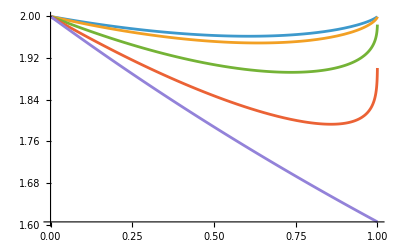

$Aborted

```mathematica
Plot[{PetzDownQ[0.5,η,1.1],PetzDownQ[0.5,η,1.3],PetzDownQ[0.5,η,1.7],PetzDownQ[0.5,η,1.9],PetzDownQ[0.5,η,2]},{η,0,1}]
```

## Petz Up

```mathematica
(*come in sezione C.2*)
PetzUpQ[α_,η_,a_]:=a/(1-a)Log2[1/4 Tr[MatrixPower[∑_(y=0)^3 MatrixPower[Subscript[ρE, y][α,η],a],1/a]]]
PetzUpQ[0.5,0.9,1.2]
```

1.9729+0. ⅈ

```mathematica
Plot[{PetzUpQ[0.5,η,1.1],PetzUpQ[0.5,η,1.3],PetzUpQ[0.5,η,1.7],PetzUpQ[0.5,η,1.9],PetzUpQ[0.5,η,2]},{η,0,1}]
```

```mathematica
Plot[{PetzUpQ[0.5,η,1.2],PetzDownQ[0.5,η,1.2]},{η,0,1}]
```

## Sandwich Down

```mathematica
(*come in sezione C.3*)
SandDownQ[α_,η_,a_]:=2+1/(1-a)Log2[Tr[MatrixPower[
MatrixPower[ρE[α,η],(1-a)/(2a)].Subscript[ρE, 0][α,η].MatrixPower[ρE[α,η],(1-a)/(2a)],a]]]
```

```mathematica
SandDownQ[0.5,0.9,40]
```

```mathematica
Plot[{SandDownQ[0.5,η,1.1],SandDownQ[0.5,η,1.3],SandDownQ[0.5,η,1.7],SandDownQ[0.5,η,1.9],SandDownQ[0.5,η,2]},{η,0,1}]
```

```mathematica
Plot[{SandDownQ[1,η,1.2],PetzUpQ[1,η,1.2],PetzDownQ[1,η,1.2]},{η,0,1}]
```

## Sandwich Up

```mathematica
(*come in sezione C.4 ---NON FUNZIONA---*)
```

```mathematica
MatrixPower[DiagonalMatrix[{q0,q1,q2,1-q0-q1-q2}],(1-a)/(2a)]
```

```mathematica
Subscript[ρE, 0][α,η]//FullSimplify
```

```mathematica
FullSimplify[(1+ⅇ^(2 α^2 (-1+η))+2 ⅇ^(α^2 (-1+η)) Cos[α^2 (-1+η)])(1-ⅇ^(2 α^2 (-1+η))+2 ⅇ^(α^2 (-1+η)) Sin[α^2 (-1+η)]),ⅇ^#&∈Reals]
```

4 ⅇ^(2 α^2 (-1+η)) (Cos[α^2 (-1+η)]+Cosh[α^2 (-1+η)]) (Sin[α^2 (-1+η)]-Sinh[α^2 (-1+η)])

```mathematica
FullSimplify[ρ[α,η],{α>0,η>0}]
```

```mathematica
σ[q0_,q1_,q2_,q3_,a_]:={{q0^(-1/2+1/(2 a)),0,0,0},{0,q1^(-1/2+1/(2 a)),0,0},{0,0,q2^(-1/2+1/(2 a)),0},{0,0,0,q3^(-1/2+1/(2 a))}}
ρ[α_,η_]:={{1/4 (1+ⅇ^(2 α^2 (-1+η))+2 ⅇ^(α^2 (-1+η)) Cos[α^2 (-1+η)]),1/2 ⅇ^(α^2 (-1+η)) Erf[(α √η)/(√2)] √((Cos[α^2 (-1+η)]+Cosh[α^2 (-1+η)]) (Sin[α^2 (-1+η)]-Sinh[α^2 (-1+η)])),1/4 √(1+ⅇ^(4 α^2 (-1+η))-2 ⅇ^(2 α^2 (-1+η)) Cos[2 α^2 (-1+η)]) Erf[(α √η)/(√2)]^2,1/2 ⅇ^(α^2 (-1+η)) Erf[(α √η)/(√2)] √(-((Cos[α^2 (-1+η)]+Cosh[α^2 (-1+η)]) (Sin[α^2 (-1+η)]+Sinh[α^2 (-1+η)])))},{1/2 ⅇ^(α^2 (-1+η)) Erf[(α √η)/(√2)] √((Cos[α^2 (-1+η)]+Cosh[α^2 (-1+η)]) (Sin[α^2 (-1+η)]-Sinh[α^2 (-1+η)])),1/4 (1-ⅇ^(2 α^2 (-1+η))-2 ⅇ^(α^2 (-1+η)) Sin[α^2 (1-η)]),1/2 ⅇ^(α^2 (-1+η)) Erf[(α √η)/(√2)] √(-((Cos[α^2 (-1+η)]-Cosh[α^2 (-1+η)]) (Sin[α^2 (-1+η)]-Sinh[α^2 (-1+η)]))),1/4 Erf[(α √η)/(√2)]^2 √(1-ⅇ^(2 α^2 (-1+η))-2 ⅇ^(α^2 (-1+η)) Sin[α^2 (1-η)]) √(1-ⅇ^(2 α^2 (-1+η))+2 ⅇ^(α^2 (-1+η)) Sin[α^2 (1-η)])},{1/4 √(1+ⅇ^(4 α^2 (-1+η))-2 ⅇ^(2 α^2 (-1+η)) Cos[2 α^2 (-1+η)]) Erf[(α √η)/(√2)]^2,1/2 ⅇ^(α^2 (-1+η)) Erf[(α √η)/(√2)] √(-((Cos[α^2 (-1+η)]-Cosh[α^2 (-1+η)]) (Sin[α^2 (-1+η)]-Sinh[α^2 (-1+η)]))),1/4 (1+ⅇ^(2 α^2 (-1+η))-2 ⅇ^(α^2 (-1+η)) Cos[α^2 (-1+η)]),1/2 ⅇ^(α^2 (-1+η)) Erf[(α √η)/(√2)] √((Cos[α^2 (-1+η)]-Cosh[α^2 (-1+η)]) (Sin[α^2 (-1+η)]+Sinh[α^2 (-1+η)]))},{1/2 ⅇ^(α^2 (-1+η)) Erf[(α √η)/(√2)] √(-((Cos[α^2 (-1+η)]+Cosh[α^2 (-1+η)]) (Sin[α^2 (-1+η)]+Sinh[α^2 (-1+η)]))),1/4 Erf[(α √η)/(√2)]^2 √(1-ⅇ^(2 α^2 (-1+η))-2 ⅇ^(α^2 (-1+η)) Sin[α^2 (1-η)]) √(1-ⅇ^(2 α^2 (-1+η))+2 ⅇ^(α^2 (-1+η)) Sin[α^2 (1-η)]),1/2 ⅇ^(α^2 (-1+η)) Erf[(α √η)/(√2)] √((Cos[α^2 (-1+η)]-Cosh[α^2 (-1+η)]) (Sin[α^2 (-1+η)]+Sinh[α^2 (-1+η)])),1/4 (1-ⅇ^(2 α^2 (-1+η))+2 ⅇ^(α^2 (-1+η)) Sin[α^2 (1-η)])}}
```

```mathematica
SandUpQ[α_,η_,a_,q0_,q1_,q2_,q3_]:=2+1/(1-a)Log2[
Re@Tr[MatrixPower[σ[q0,q1,q2,q3,a].ρ[α,η].σ[q0,q1,q2,q3,a],a]]]
maxSandUpQ[α_,η_,a_]:=NMaximize[{SandUpQ[α,η,a,q0,q1,q2,q3],{0.001<=q0&&0.001<=q1&&0.001<=q2&&0.001<=q3&&q0+q1+q2+q3==1}},{q0,q1,q2,q3},Method->"NelderMead"]
```

```mathematica
ss=maxSandUpQ[1,0.301,1.2]
```

{1.76524,{q0→0.496873,q1→0.0307138,q2→0.1232,q3→0.349214}}

```mathematica
(*Costruisci i punti da 0 a 1 con step 0.1,escludendo 0.3*)
etaList=DeleteCases[Range[0,1,0.05],0.3];

(*Calcola i punti validi*)
sandwichValidPoints=Table[{η,maxSandUpQ[1,η,1.2][[1]]},{η,etaList}];

(*Calcola il punto vicino a 0.3 separatamente*)
extraPoint={0.31,maxSandUpQ[1,0.31,1.2][[1]]};

(*Unisci tutto*)
SandwichUpQ=Join[sandwichValidPoints,{extraPoint}];
SandwichUpQ=SortBy[SandwichUpQ,First];
```

```mathematica
SandwichUpQ
```

{{0.,2.},{0.05,1.95308},{0.1,1.90915},{0.15,1.86832},{0.2,1.83073},{0.25,1.79651},{0.31,1.76011},{0.35,1.73882},{0.4,1.71572},{0.45,1.69675},{0.5,1.68214},{0.55,1.67222},{0.6,1.66735},{0.65,1.66801},{0.7,1.67482},{0.75,1.68866},{0.8,1.71082},{0.85,1.74335},{0.9,1.78952},{0.95,1.8581},{1.,1.99567}}

```mathematica
etas=Subdivide[0.01,0.999,9];
SandwichUpQ=Table[{ηi,maxSandUpQ[1,ηi,1.2][[1]]},{ηi,etas}];
```

Inverse::sing: Matrix … is singular.

NMaximize::sing: Matrix {{-1. (-(6.6811 (-0.27557 Power[«2»]+1. Power[«2»] Power[«2»] Root[«2»]))/v4$3821^(1/12)-(1.25158×10^19 v1$3818^(1/12) v3$3820^(1/6) Root[Plus[«5»]&,1] (-0.00551126+1. Power[«2»] Power[«2»] Power[«2»]))/(v4$3821^(1/12) (-1.75903×10^16+Times[«3»]+Times[«3»]+Times[«4»]))),0.,-(2.44521×10^18 v3$3820^(1/12) (-0.00551126+1. v2$3819^(1/6) v4$3821^(1/6) Root[«1»&,1]^2))/(v4$3821^(1/12) (-1.75903×10^16+8.79538×10^17 v2$3819^(1/6) Root[«1»&,1]+«23» «1» «1»-9.67714×10^18 v2$3819^(1/6) v3$3820^(1/6) Root[«2»]^2)),1.},«2»,{-1. (-(6.6811«1»(«1»«1»)/v4$3821^(1/12)-(«1»)/(«1»)),0.,-«1»,1.}} is singular.

Inverse::sing: Matrix {{-1. (-(86.8176 (-0.000533732 Power[«2»]+1. Power[«2»] Power[«2»] Root[«2»]))/q3^(1/12)+(40.434 (5.25148×10^-15 Power[«2»]+1. Power[«2»] Power[«2»] Root[«2»]) (-4.74782×10^-14-4.79346×10^-14 Power[«2»] Root[«2»]+3.53575×10^-18 Power[«2»] Root[«2»]+1. Power[«2»] Power[«2»] Power[«2»]))/(q3^(1/12) (-8.89553×10^-11+Times[«3»]) (-2.66866×10^-7+Times[«3»]))),(0.000408248 («1»))/(q3^(1/12) (-8.89553×10^-11+«1») (-2.66866×10^-7+1. q2^(1/6) Root[«1»&,1])),(0.01526 q2^(«1») («1»))/(q3^(1/12) «1» (-«23»+1. «1» Root[«1»])),1.},«1»,«1»,{«1»}} is singular.

General::stop: Further output of Inverse::sing will be suppressed during this calculation.

NMaximize::sing: Matrix «1» is singular.

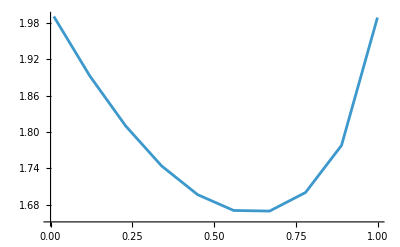

```mathematica
ListLinePlot[SandwichUpQ]
```

## Von Neumann

```mathematica
Hvn[ρ_]:= -Tr[ρ.MatrixLog[ρ]]/Log[2]
Hvn[ρE[1,0.9]]
HvnCond[ρ1_,ρ2_] := Hvn[ρ1]-Hvn[ρ2]
HvnCond[ρYE[.5,0.999],ρE[.5,0.999]]
```

0.48132

1.99956+0. ⅈ

```mathematica
HvonCond[α_,η_]:=Module[{λE,λYE,rhoE, rhoYE,hE,hYE},
rhoE=ρE[α,η];
rhoYE=ρYE[α,η];
λE=Eigenvalues[rhoE];
λYE=Eigenvalues[rhoYE];
Total[# Log2[#]&/@λE]-Total[# Log2[#]&/@λYE]
]
```

## Entropy bound with K and V

```mathematica
(*identico al codice per BPSK, il riferimento è nel file overleaf Cosmo Note*)

(*relative divergence*)
ddQ[ρ_,σ_]:=Module[{logρ,logσ},
logρ=MatrixLog[ρ];
logσ=MatrixLog[σ];ù
Tr[ρ.(logρ-logσ)]/Log[2] (*convert to log base 2*)
]
```

```mathematica
(*variance divergence*)
id4=IdentityMatrix[4];
```

```mathematica
bYEQ[α_,η_,a0_]:=Module[{Hd2YE,HdaYE,HYE,VYE,K,ρYEηα,ρEηα,a=a0},
ρEηα=ρE[α,η];
ρYEηα=ρYE[α,η];
HYE=Re@HvonCond[α,η];
VYE=Re@(Tr[ρYEηα.MatrixPower[(MatrixLog[ρYEηα]-MatrixLog[id4⊙ρEηα]),2]]/((Log[2])^2)-HYE^2);
Hd2YE=1/(1-2)Log2[Tr[MatrixPower[ρYEηα,2].MatrixPower[id4⊙ρEηα,1-2]]]; (**)
HdaYE=1/(1-a)Log2[Tr[MatrixPower[ρYEηα,a].MatrixPower[id4⊙ρEηα,1-a]]]; 
K=Re@(1/(6(2-a)^3 Log[2])2^((a-1)(-HdaYE+HYE))(Log[2^(-Hd2YE+HYE)+ⅇ^2])^3);
{HYE-((a-1)Log[2])/2 VYE-(a-1)^2 K,HdaYE,Hd2YE}
]
bYEQ[1,0.99,1.001]
```

{1.96719,1.9672+3.39639×10^-35 ⅈ,0.902633+0. ⅈ}

```mathematica
Plot[{HvonCond[1,η],bYEQ[1,η,1.1],bYEQ[1,η,1.2],bYEQ[1,η,1.3],bYEQ[1,η,1.4]},{η,0,1},
PlotLegends->{"Von Neum","1.1","1.2","1.3","1.4"}]
```

$Aborted

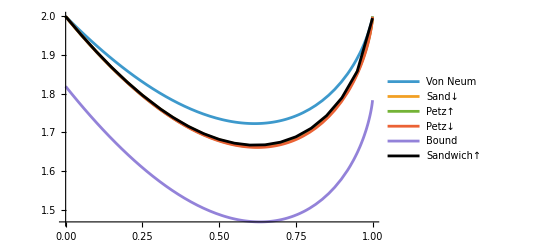

```mathematica
plot1=Plot[{HvonCond[1,η],SandDownQ[1,η,1.2],PetzUpQ[1,η,1.2],PetzDownQ[1,η,1.2],bYEQ[1,η,1.2]},{η,0,1},PlotLegends->{"Von Neum","Sand↓","Petz↑","Petz↓","Bound"}];

plot2=ListLinePlot[SandwichUpQ,PlotStyle->{Black},PlotLegends->{"Sandwich↑"}];

Show[plot1,plot2]
```

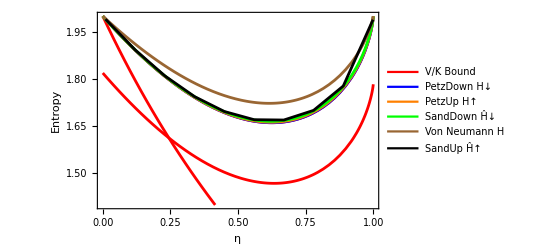

```mathematica
QpskEntropies=Legended[Show[{Plot[{bYEQ[1,η,1.2],PetzDownQ[1,η,1.2],PetzUpQ[1,η,1.2],SandDownQ[1,η,1.2],HvonCond[1,η]},{η,0,1},PlotRange->{{0,1},{1.4,2}},Frame->True,
FrameTicksStyle->Directive[Black,Thick,FontSize->12],(*dimensione numeri assi*)
FrameLabel->{Style["η",FontSize->14],Style["Entropy",FontSize->14]},(*label assi ingranditi*)
PlotStyle->{Red,Blue,Orange,Green,Brown}],
ListLinePlot[SandwichUpQ,PlotStyle->Black]}],LineLegend[{Red,Blue,Orange,Green,Brown,Black},{Style["V/K Bound"],Style["PetzDown H↓"],Style["PetzUp H↑"],Style["SandDown Ĥ↓"],Style["Von Neumann H"],Style["SandUp Ĥ↑"]},LegendLayout->"Column",LegendMarkerSize->30]]
```

```mathematica
Export["/Users/Gabriele/Documents/Wolfram/PskPureLoss/grafici/QpskEntropies.png",QpskEntropies,ImageResolution->300]
```

/Users/Gabriele/Documents/Wolfram/PskPureLoss/grafici/QpskEntropies.png

```mathematica
(*Definisco i punti campionati*)(*etas=Subdivide[0.01,0.999,9];*)  (*10 punti*)
etas = {0.01,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,0.999} ;

(*Funzioni campionate*)
SandwichedUpQpts = {{0.,2.},{0.1,1.90915},{0.2,1.83073},{0.3,1.76523},{0.4,1.71572},{0.5,1.68214},{0.6,1.66735},{0.7,1.67482},{0.8,1.71082},{0.9,1.78952},{1.,1.99567}}


bYEQpts=Table[{η,bYEQ[1,η,1.2][[1]]},{η,etas}];
petzDownQpts=Table[{η,PetzDownQ[1,η,1.2]},{η,etas}];
petzUpQpts=Table[{η,PetzUpQ[1,η,1.2]},{η,etas}];
sandDownQpts=Table[{η,SandDownQ[1,η,1.2]},{η,etas}];
vonNeumannQpts=Table[{η,HvonCond[1,η]},{η,etas}]

(*SandwichUpQ deve essere già definito come lista di punti!*)
```

{{0.,2.},{0.1,1.90915},{0.2,1.83073},{0.3,1.76523},{0.4,1.71572},{0.5,1.68214},{0.6,1.66735},{0.7,1.67482},{0.8,1.71082},{0.9,1.78952},{1.,1.99567}}

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.999,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,1.665×10^-10,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,4.995×10^-7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.000999,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},«9»,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.665×10^-10,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,4.995×10^-7,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000999}} may contain significant numerical errors.

{{0.01,1.99207},{0.1,1.92483},{0.2,1.85951},{0.3,1.8052},{0.4,1.76321},{0.5,1.73516},{0.6,1.72315},{0.7,1.7304},{0.8,1.76254},{0.9,1.83223},{0.999,1.99517}}

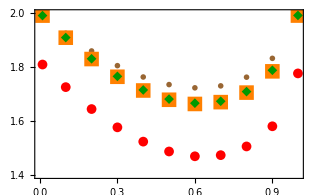

```mathematica
Needs["MaTeX`"];
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amsmath}"}];

datasetsQ={bYEQpts,petzDownQpts,petzUpQpts,sandDownQpts,SandwichedUpQpts,vonNeumannQpts};

markers={{"●",10},{"▲",10},{"■",15},{"◆",10},{"✖",10},{"✚",10}};

colors={Red,Blue,Orange,Darker[Green,.4],Black,Brown};

labelsQ=MaTeX[#,Magnification->2.5]&/@{"B_a","H^{\\downarrow}_a","H^{\\uparrow}_a","\\tilde{H}^{\\downarrow}_a","\\tilde{H}^{\\uparrow}_a","H"};

QpskEntropies=Legended[ListPlot[datasetsQ,PlotMarkers->markers,PlotStyle->colors,PlotRange->{{0,1},{1.4,2}},Frame->True,BaseStyle->{FontFamily->"Times",FontSize->20},FrameTicksStyle->Directive[Black,Thick],FrameLabel->{MaTeX["\\eta",Magnification->2.5],MaTeX["",Magnification->1.1]},ImageSize->600],Placed[SwatchLegend[colors,labelsQ,LegendMarkers->markers,LegendLayout->"Column",LegendMarkerSize->14],Right]]
```

## Finite size Rate

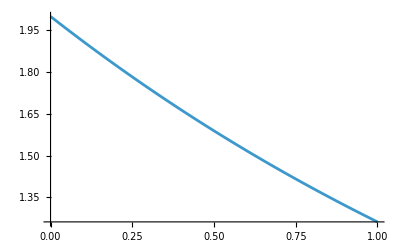

```mathematica
g[ϵ_]:=Log2[2/ϵ^2]
(*funzione error correction leakage calcolata nel file overleaf QPSK, sez 4.4*)
Leak[α_,η_] := -2(Subscript[m, +1][α,η]Log2[Subscript[m, +1][α,η]]+Subscript[m, -1][α,η]Log2[Subscript[m, -1][α,η]])
Plot[Leak[1,η],{η,0,1}]
```

## Rate with AEP

```mathematica
δ[ϵ_]:=8(Log2[2/ϵ^2])^(1/2) (*fattore aep per d=4*)
RateAEP[α_,η_,n_,ϵ_]:=HvonCond[α,η]-δ[ϵ]/n^(1/2)-Leak[α,η]
```

{{100.,-5.3765},{251.189,-3.20396},{630.957,-1.83317},{1584.89,-0.968266},{3981.07,-0.422547},{10000.,-0.0782211},{25118.9,0.139034},{63095.7,0.276112},{158489.,0.362603},{398107.,0.417175},{1.×10^6,0.451607},{2.51189×10^6,0.473333},{6.30957×10^6,0.48704},{1.58489×10^7,0.49569},{3.98107×10^7,0.501147},{1.×10^8,0.50459}}

{{100.,-5.60599},{251.189,-3.43344},{630.957,-2.06266},{1584.89,-1.19775},{3981.07,-0.652031},{10000.,-0.307706},{25118.9,-0.090451},{63095.7,0.0466275},{158489.,0.133118},{398107.,0.18769},{1.×10^6,0.222123},{2.51189×10^6,0.243848},{6.30957×10^6,0.257556},{1.58489×10^7,0.266205},{3.98107×10^7,0.271662},{1.×10^8,0.275105}}

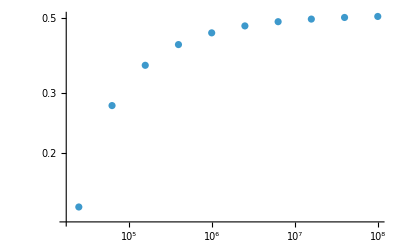

```mathematica
RateAEPList=Table[{10^x,RateAEP[1,0.9,10^x,10^-8]},{x,Log10[100],Log10[100000000],0.4}]
RateAEPList70=Table[{10^x,RateAEP[1,0.7,10^x,10^-8]},{x,Log10[100],Log10[100000000],0.4}]
plotAEP=ListLogLogPlot[RateAEPList]
```

## Rate with SandUp

```mathematica
RateSandUp[α_,η_,a_,n_,ϵ_]:=maxSandUpQ[α,η,a]-g[ϵ]/(n(a-1))-Leak[α,η]
```

```mathematica
RateSandUp[1,0.9,1.2,10^8,10^-8]
```

```mathematica
RateSandUpList=Table[{10^x,RateSandUp[1,0.9,1.1,10^x,10^-8][[1]]},{x,Log10[100],Log10[100000000],0.4}]
RateSandUpList70=Table[{10^x,RateSandUp[1,0.7,1.1,10^x,10^-8][[1]]},{x,Log10[100],Log10[100000000],0.4}]
```

{{100.,-4.92689},{251.189,-1.66759},{630.957,-0.370036},{1584.89,0.146528},{3981.07,0.352176},{10000.,0.434046},{25118.9,0.466639},{63095.7,0.479615},{158489.,0.48478},{398107.,0.486837},{1.×10^6,0.487656},{2.51189×10^6,0.487981},{6.30957×10^6,0.488111},{1.58489×10^7,0.488163},{3.98107×10^7,0.488183},{1.×10^8,0.488192}}

{{100.,-5.16248},{251.189,-1.90318},{630.957,-0.605627},{1584.89,-0.0890623},{3981.07,0.116586},{10000.,0.198456},{25118.9,0.231049},{63095.7,0.244024},{158489.,0.24919},{398107.,0.251246},{1.×10^6,0.252065},{2.51189×10^6,0.252391},{6.30957×10^6,0.252521},{1.58489×10^7,0.252572},{3.98107×10^7,0.252593},{1.×10^8,0.252601}}

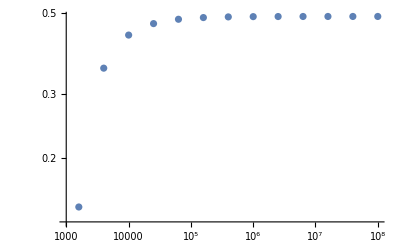

```mathematica
plotSand=ListLogLogPlot[RateSandUpList]
```

## Rate with Bound

```mathematica
(*rate senza ottimizzazione, provato per alcuni valori di α ed a*)
RateBound[α_,η_,a_,n_,ϵ_]:=bYEQ[α,η,a]-g[ϵ]/(n(a-1))-Leak[α,η]
RateBound[1.84606,0.98,1.14608,100,10^-8]
```

-2.58324

{{100.,-4.96285},{251.189,-1.70355},{630.957,-0.405999},{1584.89,0.110565},{3981.07,0.316213},{10000.,0.398083},{25118.9,0.430676},{63095.7,0.443652},{158489.,0.448817},{398107.,0.450874},{1.×10^6,0.451692},{2.51189×10^6,0.452018},{6.30957×10^6,0.452148},{1.58489×10^7,0.4522},{3.98107×10^7,0.45222},{1.×10^8,0.452229}}

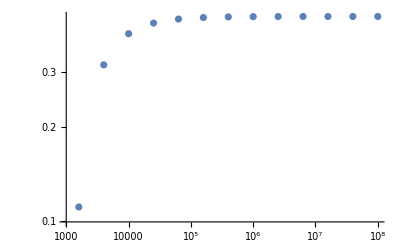

```mathematica
RateBoundList=Table[{10^x,RateBound[1,0.9,1.1,10^x,10^-8][[1]]},{x,Log10[100],Log10[100000000],0.4}]
RateBoundList70=Table[{10^x,RateBound[1,0.7,1.1,10^x,10^-8][[1]]},{x,Log10[100],Log10[100000000],0.4}]

plotBound=ListLogLogPlot[RateBoundList]
```

```mathematica
{{100.,-4.962851021267084},{251.18864315095797,-1.7035502179231},{630.957344480193,-0.40599919712108656},{1584.893192461114,0.1105651684192055},{3981.0717055349733,0.3162131463932134},{10000.,0.39808308103449375},{25118.864315095823,0.43067608906793353},{63095.73444801943,0.44365159927595377},{158489.3192461114,0.4488172429313566},{398107.1705534969,0.4508737227110966},{1.*^6,0.45169242205750937},{2.5118864315095823*^6,0.4520183521378438},{6.309573444801942*^6,0.45214810723992405},{1.5848931924611142*^7,0.4521997636764781},{3.9810717055349775*^7,0.4522203284742754},{1.*^8,0.4522285154677397}}
```

{{100.,-4.96285},{251.189,-1.70355},{630.957,-0.405999},{1584.89,0.110565},{3981.07,0.316213},{10000.,0.398083},{25118.9,0.430676},{63095.7,0.443652},{158489.,0.448817},{398107.,0.450874},{1.×10^6,0.451692},{2.51189×10^6,0.452018},{6.30957×10^6,0.452148},{1.58489×10^7,0.4522},{3.98107×10^7,0.45222},{1.×10^8,0.452229}}

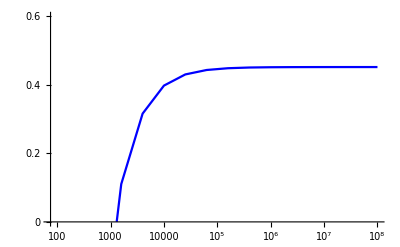

```mathematica
{{100.,-4.962851021267084},{251.18864315095797,-1.7035502179231},{630.957344480193,-0.40599919712108656},{1584.893192461114,0.1105651684192055},{3981.0717055349733,0.3162131463932134},{10000.,0.39808308103449375},{25118.864315095823,0.43067608906793353},{63095.73444801943,0.44365159927595377},{158489.3192461114,0.4488172429313566},{398107.1705534969,0.4508737227110966},{1.*^6,0.45169242205750937},{2.5118864315095823*^6,0.4520183521378438},{6.309573444801942*^6,0.45214810723992405},{1.5848931924611142*^7,0.4521997636764781},{3.9810717055349775*^7,0.4522203284742754},{1.*^8,0.4522285154677397}}
ListPlot[RateBoundList,Joined->True,PlotStyle->Blue,ScalingFunctions->{"Log","Linear"},PlotRange->{Automatic,{0,0.6}}]
```

```mathematica
(*tentativo di ottimizzazione su α ed a, ---NON FUNZIONA---*)
OptRateBound[η_,n_]:=Module[{nmax},
nmax=NMaximize[{RateBound[α,η,a,n,10^-8],1<a<1.3,0.4<α<1.5},{a,α}];
{nmax[[1]],a,α}/.nmax[[2]]
]
```

```mathematica
OptRateBound2[η_,n_]:=NMaximize[{RateBound[α,η,a,n,10^-8],1<a<1.3,0.4<α<1.5},{α,a}]
```

```mathematica
OptRateBound2[0.9,10^8]
```

JordanDecomposition::eivn: Incorrect number 0 of eigenvectors for eigenvalue Root[0.0000152588 Erfc[0.67082 α]^2+«75»+0.000488281 ⅇ^(-0.4 α^2) Cos[0.1 Power[«2»]]^2 Erf[0.67082 α] Erfc[0.67082 α]^2 Sin[0.1 Power[«2»]]^2+«24»&,1] with multiplicity 4.

JordanDecomposition::eivn: Incorrect number 0 of eigenvectors for eigenvalue 1/4 ⅇ^(-0.3 α^2) (ⅇ^(0.1 α^2)+ⅇ^(0.3 α^2)-2 ⅇ^(0.2 α^2) Cos[0.1 α^2]) with multiplicity 4.

$Aborted

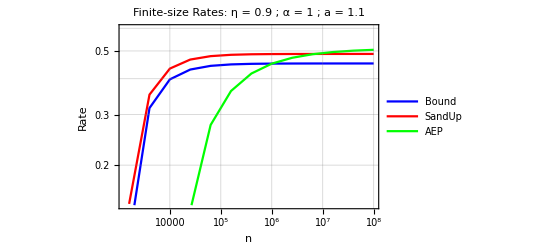

```mathematica
ListLinePlot[{RateBoundList,RateSandUpList,RateAEPList},Joined->True,PlotStyle->{Blue,Red,Green},ScalingFunctions->{"Log","Log"},PlotRange->{Automatic,{0.145,0.6}},PlotLegends->{"Bound","SandUp","AEP"},Frame->True,FrameLabel->{"n","Rate"},GridLines->Automatic,PlotLabel->"Finite-size Rates: η = 0.9 ; α = 1 ; a = 1.1"]
```

```mathematica
ListLinePlot[{RateBoundList70,RateSandUpList70,RateAEPList70},Joined->True,PlotStyle->{Blue,Red,Green},ScalingFunctions->{"Log","Log"},PlotRange->{Automatic,{0.145,0.6}},PlotLegends->{"Bound","SandUp","AEP"},Frame->True,FrameLabel->{"n","Rate"},GridLines->Automatic,PlotLabel->"Finite-size Rates: η = 0.9 ; α = 1 ; a = 1.1"]
```

## 3.1 QPSK optimized rates version 1 (the plot in the article are here)

```mathematica
(*
	Script *.bat per avviare Mathematica con il compilatore
   Salvare la Chat di ChatGPT che ci ha aiutato
   Sviluppare il MUltistarting che fa una ottimizzazione ibrida con RandomSearch e il Gradiente.
  Confrontare analiticamente lo stato compilato con C e con Mathematica (ρ vs rhoCompiled).
  Scriversi le altre ottiminizzazioni e organizzare il notebook per renderlo leggibile e commentarlo.

 

*)
```

## Optimization of Entropies via C compiler

In this notebook, we...

#### 0. Run the C compiler

```mathematica
Needs["CCompilerDriver`"]
CCompilers[]
```

{{Name→Clang,Compiler→CCompilerDriver`ClangCompiler`ClangCompiler,CompilerInstallation→/usr/bin,CompilerName→Automatic},{Name→GCC,Compiler→CCompilerDriver`GCCCompiler`GCCCompiler,CompilerInstallation→/usr/bin,CompilerName→Automatic}}

```mathematica
fg=Compile[{{x,_Real}},x^2,CompilationTarget->"C"]
```

CompiledFunction[…]

```mathematica
fg[54]
```

2916.

```mathematica
cnumber=Compile[{{x,_Real},{y,_Real}},x+ⅈ y,CompilationTarget->"C"]
```

CompiledFunction[…]

```mathematica
cnumber2=Compile[{{x,_Complex}},Sqrt[Re[x]^2.+Im[x]^2.],CompilationTarget->"C"]
```

CompiledFunction[…]

```mathematica
cnumber2[3+ⅈ 2]
```

3.60555

```mathematica
AA={{2,1},{0,3}}
```

{{2,1},{0,3}}

```mathematica
Inverse[AA]//N
```

{{0.5,-0.166667},{0.,0.333333}}

```mathematica
inv[AA]
```

inv[{{2,1},{0,3}}]

```mathematica
SetSystemOptions["ParallelOptions"->"ParallelThreadNumber"->6];
```

```mathematica
$ProcessorCount
```

8

```mathematica
Kernels[]
```

{Local,Local,Local,Local,Local,Local,Local,Local}

```mathematica
Length[Kernels[]]
```

8

```mathematica
AbsoluteTiming[Table[Pause[1];f[i],{i,6}]]
```

{6.02022,{f[1],f[2],f[3],f[4],f[5],f[6]}}

```mathematica
AbsoluteTiming[ParallelTable[Pause[1];f[i],{i,9}]]
```

{2.02329,{f[1],f[2],f[3],f[4],f[5],f[6],f[7],f[8],f[9]}}

## 1. Sandwich Up

#### Definitions

```mathematica
normVec=Compile[{{α,_Real},{η,_Real}},
Module[{t,e,e2,ns=ConstantArray[0.,4],s},
t=α^2 (1-η);
e=Exp[-t];
e2=e*e;
Do[
ns[[s+1]]=1./Sqrt[1.+e2*Cos[Pi*s]+2.*e*Cos[Pi*s/2.+t]],{s,0,3}];
ns],CompilationTarget->"C",RuntimeOptions->"Speed"];

psRowAndFourier=Compile[{{α,_Real},{η,_Real}},
Module[{erf,erfc,r0=Table[0.,{4}],F=Table[0.,{4}]},
erf=Erf[α/Sqrt[2.]*Sqrt[η]];
erfc=1.-erf;
r0[[1]]=0.25 (1.+erf)^2;
r0[[2]]=0.25 (1.-erf^2);
r0[[3]]=0.25 erfc^2;
r0[[4]]=r0[[2]];
F[[1]]=1.;
F[[2]]=r0[[1]]-r0[[3]];
F[[3]]=r0[[1]]+r0[[3]]-2 r0[[2]];
F[[4]]=F[[2]];
F],CompilationTarget->"C",RuntimeOptions->"Speed"];

(*Subscript[ρE, 0][α,η]*)
rhoCompiled=Compile[{{α,_Real},{η,_Real}},
Module[{ns,F,ρ=ConstantArray[0.,{4,4}],s,s1,k},
ns=normVec[α,η];
F=psRowAndFourier[α,η];
Do[k=Mod[s-s1,4]+1;
ρ[[s+1,s1+1]]=F[[k]]/(4. ns[[s+1]] ns[[s1+1]]);
,{s,0,3},{s1,0,3}
];
ρ],
CompilationTarget->"C",RuntimeOptions->"Speed"];
```

```mathematica
sandUpWVM=Compile[{{α,_Real},{η,_Real},{a,_Real},{q0,_Real},{q1,_Real},{q2,_Real}},
Module[{ε=10^-10,q3,σ,ρ,mat,λ=ConstantArray[0.,4],tr},
(*q3=1.-q0-q1-q2;
σ=DiagonalMatrix[{q0^(-.5+.5/a),q1^(-.5+.5/a),q2^(-.5+.5/a),q3^(-.5+.5/a)}];*)
q3=Max[ε,1.-q0-q1-q2];
	(*
q0=Max[ε,q0];
	q1=Max[ε,q1];
	q2=Max[ε,q2];
*)
	σ=DiagonalMatrix[{q0^(-.5+.5/a),q1^(-.5+.5/a),q2^(-.5+.5/a),q3^(-.5+.5/a)}];
ρ=rhoCompiled[α,η];
mat=σ.ρ.σ;
λ=Flatten@Eigenvalues[mat];
tr=Total[λ^a];
2.+Log[tr]/((1.-a)*Log[2.])
],
CompilationTarget->"WVM",RuntimeOptions->"Speed"];
```

```mathematica
compiledLeak=Compile[{{α,_Real},{η,_Real}},
Module[{term},
term=Erf[0.7071067811865475*α*Sqrt[η]];
-2*(0.5*(1-term)*Log2[0.5 (1-term)]+0.5*(1+term)*Log2[0.5 (1+term)])
],
CompilationTarget->"C",
RuntimeOptions->"Speed"];

(*
objFun[α_?NumericQ,a_?NumericQ,q0_?NumericQ,q1_?NumericQ,q2_?NumericQ,η_?NumericQ,n_?NumericQ]:=Module[{val},
val=sandUpWVM[α,η,a,q0,q1,q2]-Log[2/10.^(-16)]/(n (a-1.))-compiledLeak[α,η];
val=Chop@Re@val;
If[NumericQ[val]&&FreeQ[val,ComplexInfinity|Indeterminate|Infinity],val,-∞]];
*)

objFun[α_?NumericQ,a_?NumericQ,q0_?NumericQ,q1_?NumericQ,q2_?NumericQ,η_?NumericQ,n_?NumericQ]:=Module[{val,safe=True,penalty=10^6},
(*blocco sicuro:protezione su a,α,q0,q1,q2*)
If[a<=1.01||α<=10^-6||q0<0||q1<0||q2<0||q0+q1+q2>0.9999,Return[-penalty]];
Quiet[
Check[
val=sandUpWVM[α,η,a,q0,q1,q2]-Log2[2/10.^(-16)]/(n (a-1.))-compiledLeak[α,η]-(Log2[1/10.^(-8)]-1)/n;
val=Chop@Re@val;
If[NumericQ[val]&&FreeQ[val,ComplexInfinity|Indeterminate|Infinity],val,safe=False],
safe=False
]
];
If[safe,val,-penalty]
];

RateSandUpFast[η_?NumericQ,n_?NumericQ]:=NMaximize[{objFun[α,a,q0,q1,q2,η,n],q0>N[10^-8],q1>N[10^-8],q2>N[10^-8],N[1-10^-8]>q0+q1+q2,a>1.001,α>0.0001},{q0,q1,q2,a,α},Method->{"RandomSearch"}
(*{"NelderMead","InitialPoints"->{{q0,q1,q2,a,α}/. {q0->1.0050746858557216,q1->0.016813169182250527,q2->0.00848605100692608,a->1.7700369937489324,α->2.1200499125526227}}}*)
];


RateSandUpMultiStart[η_?NumericQ,n_?NumericQ,trials_Integer:6]:=Module[{results,seeds,obj,best},
seeds=MapThread[Join,{RandomReal[{0.01,0.99},{trials,3}],List/@RandomReal[{1.0001,1.5},trials],List/@RandomReal[{.5,2},trials]}];
results=ParallelTable[NMaximize[{objFun[α,a,q0,q1,q2,η,n],q0>10^-8,q1>10^-8,q2>10^-8,q0+q1+q2<1-10^-8,a>1.0001,α>10^-6},{q0,q1,q2,a,α},Method->{"NelderMead","InitialPoints"->{seed}}],{seed,seeds}];
best=First@MaximalBy[results,First];
best];

(* this is an alternative method that Combine global+local (recommended hybrid). You can first run RandomSearch to explore,then refine with NelderMead
SeedRandom[123];(*for reproducibility*)
rough=RateSandUpFast[η,n];(*global search*)
bestGuess=Last[rough];(*extract best parameters*)refined=NMaximize[{objFun[α,a,q0,q1,q2,η,n],q0>10^-8,q1>10^-8,q2>10^-8,q0+q1+q2<1-10^-8,2>a>1.01,α>10^-6},{q0,q1,q2,a,α},Method->{"NelderMead","InitialPoints"->{q0,q1,q2,a,α}/. bestGuess}];

*)
```

#### Runs

```mathematica
{Row[{Dynamic[ηi],"/",1}],ProgressIndicator[Dynamic[ηi],{0,1}]}
```

{/1,}

```mathematica
nlist={10,50,10^2,5 10^2,10^3,5 10^3,10^4,5 10^4, 10^5,10^6,10^7,10^8}
```

{10,50,100,500,1000,5000,10000,50000,100000,1000000,10000000,100000000}

```mathematica
First[nlist]
```

10

```mathematica
RateSandUpMultiStart[0.9,10^8,12]
```

{0.71441,{q0→0.761485,q1→0.00326498,q2→0.0323873,a→1.01002,α→1.65125}}

```mathematica
listRateSandUp=Table[RateSandUpMultiStart[.9,ni],{ni,nlist}]
```

{{-2.31776,{q0→0.500703,q1→0.04963,q2→0.135358,a→4.31615×10^8,α→1.99784}},{-0.271721,{q0→0.500703,q1→0.04963,q2→0.135358,a→6.70527×10^7,α→1.99784}},{-0.0159669,{q0→0.500703,q1→0.04963,q2→0.135358,a→1.49843×10^7,α→1.99784}},{0.281326,{q0→0.69457,q1→0.00925773,q2→0.0495142,a→1.7662,α→1.58184}},{0.399824,{q0→0.720274,q1→0.00636328,q2→0.0407514,a→1.43829,α→1.58247}},{0.571927,{q0→0.743339,q1→0.00400274,q2→0.0334477,a→1.16123,α→1.61774}},{0.614608,{q0→0.748094,q1→0.00356674,q2→0.0320256,a→1.1097,α→1.6292}},{0.686483,{q0→0.755757,q1→0.00292015,q2→0.0298138,a→1.0327,α→1.64994}},{0.686483,{q0→0.755757,q1→0.00292015,q2→0.0298138,a→1.0327,α→1.64994}},{0.709564,{q0→0.758166,q1→0.00273298,q2→0.0291415,a→1.01016,α→1.6569}},{0.70816,{q0→0.728918,q1→0.00403947,q2→0.0297644,a→1.01,α→1.76449}},{0.713975,{q0→0.740894,q1→0.00272109,q2→0.0293575,a→1.01004,α→1.67738}}}

```mathematica
listRateSandUp2={{-3.3171417078049563,{q0->0.6766146466486811,q1->0.01143583663083629,q2->0.0560058598332974,a->1.999999999961204,α->1.5984184183122838}},{-0.3143810142367319,{q0->0.6766098542344653,q1->0.01143633752682978,q2->0.05600742560852217,a->2.,α->1.5984326216875708}},{0.06096407248870894,{q0->0.6766126229512488,q1->0.011436032866437112,q2->0.05600661140392967,a->2.,α->1.5984238621648295}},{0.38322923725141,{q0->0.7107436629637744,q1->0.007410259828728778,q2->0.0439286363538537,a->1.5590984174937248,α->1.57807919802355}},{0.46820338038592424,{q0->0.728039787414541,q1->0.0055350623288744965,q2->0.03822702296705488,a->1.3415260062134646,α->1.5903475682961044}},{0.5997910327760934,{q0->0.7460733446447922,q1->0.00374909157505134,q2->0.0326256829203133,a->1.1312734316291475,α->1.6241804442053294}},{0.633821516969016,{q0->0.7499852516503548,q1->0.003400354933495334,q2->0.031470117676727694,a->1.0899729765119246,α->1.6340819229338828}},{0.6922970399586563,{q0->0.7563466532486846,q1->0.002873574477544296,q2->0.029648149197920404,a->1.0271029136833083,α->1.6516247659018646}},{0.6922970399586549,{q0->0.7563466982082183,q1->0.0028735669902413266,q2->0.029648141917318516,a->1.0271029217551293,α->1.6516246803317172}},{0.7110533916325711,{q0->0.7621724500210219,q1->0.0021826836294475144,q2->0.028064124905397014,a->1.0101429378610784,α->1.65823187709892}},{0.6921017757637468,{q0->0.677526007777362,q1->0.007643047330446001,q2->0.0391375503051995,a->1.0100000011825585,α->1.863135149899416}},{0.6883466882487883,{q0->0.7808949797030984,q1->0.021340808011069735,q2->0.02549577294128098,a->1.01000000204472,α->1.5690569397544976}}};
listRateSandUp = {{0.23978736496163433,{q0->0.5007029804031644,q1->0.04962998082676593,q2->0.1353583038361863,a->1.617754252882703*^8,α->1.9978370325354122}},{0.2397873666313824,{q0->0.5007029387321588,q1->0.04962999100143655,q2->0.13535830298800255,a->2.5101736028365493*^7,α->1.9978372576915806}},{0.23978735591819067,{q0->0.5007029983930635,q1->0.04962996312334642,q2->0.13535828737243316,a->4.120746413752867*^6,α->1.9978370322637258}},{0.383229237251412,{q0->0.7107436650368122,q1->0.007410259168226643,q2->0.04392863592526381,a->1.5590984151824576,α->1.5780791925417315}},{0.4682033803859261,{q0->0.7280397895746276,q1->0.005535061981213917,q2->0.038227022447202934,a->1.3415260051082065,α->1.5903475628224664}},{0.5997910327760981,{q0->0.7460733500177973,q1->0.003749090087866018,q2->0.032625681482903034,a->1.1312734338759793,α->1.6241804289511896}},{0.6338215169690108,{q0->0.7499852485475721,q1->0.003400356047998289,q2->0.0314701181859085,a->1.0899729761600707,α->1.634081931970914}},{0.692297039958633,{q0->0.7563466501545186,q1->0.0028735752748613214,q2->0.029648150120749183,a->1.027102914708965,α->1.651624773420932}},{0.6922970399586607,{q0->0.7563466405250282,q1->0.0028735781405855127,q2->0.02964815241309963,a->1.0271029166436907,α->1.6516248002056295}},{0.7103337574394498,{q0->0.7715707567568411,q1->0.0025574500155108935,q2->0.027002838354808545,a->1.010275165741268,α->1.6609383255485533}},{0.7129012936323871,{q0->0.7503632125819159,q1->0.003964316663217923,q2->0.02625767619000639,a->1.0101344457286363,α->1.6315988837861157}},{0.7130837434058437,{q0->0.7441903336059486,q1->0.0034123286830994564,q2->0.03200232277296618,a->1.0100063379780226,α->1.7206680092425017}}};
```

## 2. VK bound (migliorare Sandwich Up come VK bound)

#### Definitions

```mathematica
(*ClearAll["Global`*"];*)

matPow=Compile[{{vals,_Complex,1},{vecs,_Complex,2},{p,_Real}},
Module[{inv,vecst},
vecst=Transpose[vecs];
(*vals=clipλ[vals]^p;*)
inv=Inverse[vecst];
vecst.DiagonalMatrix[vals^p].inv
],
CompilationTarget->"C",RuntimeOptions->"Speed"];

normVecC=Compile[{{α,_Real},{η,_Real}},
Module[{t=α^2 (1-η),e,e2,ns=Table[0.,{4}],s},
e=Exp[-t];
e2=e*e;
Do[ns[[s+1]]=1./Sqrt[1.+e2*Cos[π*s]+2.*e*Cos[π*s/2.+t]],{s,0,3}];
ns],
CompilationTarget->"C",RuntimeOptions->"Speed"];

PmatrixC=Compile[{{α,_Real},{η,_Real}},
Module[{erf,erfc,r0,r1,r2,P=ConstantArray[0.,{4,4}]},
erf=Erf[α*Sqrt[η/2.]];
erfc=1.-erf;
r0=0.25 (1.+erf)^2;
r1=0.25 (1.-erf^2);
r2=0.25 erfc^2;
P[[1]]={r0,r1,r2,r1};
P[[2]]={r1,r0,r1,r2};
P[[3]]={r2,r1,r0,r1};
P[[4]]={r1,r2,r1,r0};
P],CompilationTarget->"C",RuntimeOptions->"Speed"];

rhoEyCRe=Compile[{{α,_Real},{η,_Real},{y,_Integer}},
Module[{ns=normVecC[α,η],Prow,ρ=ConstantArray[0.,{4,4}],s,s1,x,acc},
Prow=PmatrixC[α,η][[y+1]];(*length-4 row of P*)
For[s=0,s<=3,s++,
For[s1=0,s1<=3,s1++,acc=0.;
For[x=0,x<=3,x++,
acc+=Prow[[x+1]]*Cos[(π/2.) (s-s1) x];
];
ρ[[s+1,s1+1]]=acc/(4. ns[[s+1]] ns[[s1+1]]);
];
];
ρ
],CompilationTarget->"C",RuntimeOptions->"Speed"];

rhoEyCIm=Compile[{{α,_Real},{η,_Real},{y,_Integer}},
Module[{ns=normVecC[α,η],Prow,ρ=ConstantArray[0.,{4,4}],s,s1,x,acc},
Prow=PmatrixC[α,η][[y+1]];(*length-4 row of P*)
For[s=0,s<=3,s++,
For[s1=0,s1<=3,s1++,acc=0.;
For[x=0,x<=3,x++,
acc+=Prow[[x+1]]*Sin[(π/2.) (s-s1) x];
];
ρ[[s+1,s1+1]]=acc/(4. ns[[s+1]] ns[[s1+1]]);
];
];
ρ
],CompilationTarget->"C",RuntimeOptions->"Speed"];

rhoYECompiledRe=Compile[{{α,_Real},{η,_Real}},
Module[{ρYE=ConstantArray[0.,{16,16}],y,i,j,blk},
For[y=0,y<=3,y++,
blk=rhoEyCRe[α,η,y];(*4×4 block*)
For[i=1,i<=4,i++,
For[j=1,j<=4,j++,ρYE[[4*y+i,4*y+j]]=blk[[i,j]];
];
];
];
ρYE/4.],CompilationTarget->"C",RuntimeOptions->"Speed"];

rhoYECompiledIm=Compile[{{α,_Real},{η,_Real}},
Module[{ρYE=ConstantArray[0.,{16,16}],y,i,j,blk},For[y=0,y<=3,y++,blk=rhoEyCIm[α,η,y];(*4×4 block*)For[i=1,i<=4,i++,For[j=1,j<=4,j++,ρYE[[4*y+i,4*y+j]]=blk[[i,j]];];];];
ρYE/4.],CompilationTarget->"C",RuntimeOptions->"Speed"];

(*rhoECompiled si può ulteriormente ottiizzare in termini di PmatrixC, ma Zdenek non vuole*)
PFourierC=Compile[{{α,_Real},{η,_Real}},Module[{erf,erfc,r0=Table[0.,{4}],F=Table[0.,{4}]},
erf=Erf[α*Sqrt[η/2.]];
erfc=1.-erf;
r0[[1]]=0.25(1.+erf)^2;r0[[2]]=0.25(1.-erf^2);
r0[[3]]=0.25 erfc^2;r0[[4]]=r0[[2]];
F[[1]]=1.;F[[2]]=r0[[1]]-r0[[3]];
F[[3]]=r0[[1]]+r0[[3]]-2 r0[[2]];F[[4]]=F[[2]];
F],CompilationTarget->"C",RuntimeOptions->"Speed"];

rhoECompiled=Compile[{{α,_Real},{η,_Real}},Module[{ns=normVecC[α,η],ρ=ConstantArray[0.,{4,4}],s},
Do[s;
ρ[[s,s]]=1/(4. ns[[s]]^2.),{s,4}];
ρ],
CompilationTarget->"C",RuntimeOptions->"Speed"];


compiledLeak=Compile[{{α,_Real},{η,_Real}},
Module[{term},
term=Erf[0.7071067811865475*α*Sqrt[η]];
-2*(0.5*(1-term)*Log2[0.5 (1-term)]+0.5*(1+term)*Log2[0.5 (1+term)])
],
CompilationTarget->"C",
RuntimeOptions->"Speed"];

diag16C=Compile[{{v,_Complex,1}},Block[{d=Table[0.+0.I,{16},{16}],i},
For[i=1,i<=16,i++,d[[i,i]]=v[[i]]];
d],CompilationTarget->"C",RuntimeOptions->"Speed"];

coreBYEQ=Compile[{{valsYE,_Complex,1},{vecsYE,_Complex,2},{valsId,_Complex,1},{vecsId,_Complex,2},{valsE,_Complex,1},{a,_Real}},
Module[{
rhoYEa=Table[0.+0.I,{16},{16}],idRhoE1a=Table[0.+0.I,{16},{16}],
rhoYE=Table[0.+0.I,{16},{16}],idRhoE=Table[0.+0.I,{16},{16}],
rhoE=Table[0.+0.I,{4},{4}],
MatLogrhoYE=Table[0.+0.I,{16},{16}],
diff=Table[0.+0.I,{16},{16}],
HYE=0.+0.I,vYE,vId,VYE,Hd2,Hda,K},
(*potenze (funziona perché matPow usa solo algebra C-safe)*)
rhoYEa=Chop[matPow[valsYE,vecsYE,a]];
idRhoE1a=matPow[valsId,vecsId,1.-a]; (*si può evitare matPow *)

(*ricostruzioni con diag16C–niente DiagonalMatrix*)
vYE=Transpose[vecsYE];
vId=Transpose[vecsId];


rhoYE=vYE.diag16C[valsYE].Inverse[vYE];
idRhoE=vId.diag16C[valsId].Inverse[vId];

(*entropia condizionata–formula solo su vettori*)
MatLogrhoYE=vYE.diag16C[Log[valsYE]].Inverse[vYE];
diff=MatLogrhoYE-vId.diag16C[Log[valsId]].Inverse[vId]; (*vId=identityMatrix*)

HYE=(-Tr[rhoYE.MatLogrhoYE]+Total[valsE Log[valsE]])/Log[2];
VYE=(Tr[rhoYE.diff.diff]/(Log[2.]^2.))-HYE^2.;

Hd2=-Log2[Tr[rhoYE.rhoYE.Inverse[idRhoE]]];
Hda=Log2[Tr[rhoYEa.idRhoE1a]]/(1.-a);
K=(1./(6. (2.-a)^3 Log[2.]))*2.^((a-1.) (-Hda+HYE))*(Log[2.^(-Hd2+HYE)+Exp[2.]])^3;
HYE-((a-1.) Log[2.])/2. VYE-(a-1.)^2 K
],
CompilationTarget->"C",RuntimeOptions->"Speed"];

penalty=10.^8;(*valore molto negativo per punti proibiti*)

diag4C=Compile[{{v,_Complex,1}},Block[{d=Table[0.+0.I,{4},{4}],i},
For[i=1,i<=4,i++,d[[i,i]]=v[[i]]];
d],CompilationTarget->"C",RuntimeOptions->"Speed"];

bYEQFast[α_?NumericQ,η_?NumericQ,a_?NumericQ]:=Module[{rhoE=ConstantArray[0.,{4,4}],valsE=ConstantArray[0.,4],
rhoYE=ConstantArray[0.+0.I,{16,16}] ,valsYE=ConstantArray[0.+0.I,16],vecsYE=ConstantArray[0.+0.I,{16,16}],
idRhoE=ConstantArray[0.+0.I,{16,16}],valsId=ConstantArray[0.+0.I,16],vecsId=ConstantArray[0.+0.I,{16,16}]},
rhoE=rhoECompiled[α,η];
valsE=Chop[Re[Eigenvalues[rhoE]],10^-8];
rhoYE=Chop[rhoYECompiledRe[α,η]]+I*Chop[ rhoYECompiledIm[α,η]];
{valsYE,vecsYE}=Eigensystem[rhoYE];
valsYE=Re[valsYE];
vecsYE=N[Re@Chop[vecsYE]+I Im@Chop[vecsYE],MachinePrecision];
idRhoE=diag4C[{1.,1.,1.,1.}]~KroneckerProduct~rhoE;
{valsId,vecsId}=Eigensystem[idRhoE];
Re[coreBYEQ[valsYE,vecsYE,valsId,vecsId,valsE,a]]
]
(****** --- ottimizzazione con le q --- ******)

(*coreBYEQ è la stessa di prima, l'unica differenza è che valsId, vecsId adesso sono calcolati su 1⊗σ*)

bYEQQFast[α_?NumericQ,η_?NumericQ,a_?NumericQ,q0_?NumericQ,q1_?NumericQ,q2_?NumericQ]:=Module[{rhoE=ConstantArray[0.,{4,4}],valsE=ConstantArray[0.+0.I,4],
rhoYE=ConstantArray[0.+0.I,{16,16}] ,valsYE=ConstantArray[0.+0.I,16],vecsYE=ConstantArray[0.+0.I,{16,16}],
idRhoE=ConstantArray[0.+0.I,{16,16}],valsId=ConstantArray[0.+0.I,16],vecsId=ConstantArray[0.+0.I,{16,16}]},
rhoE=rhoECompiled[α,η];
valsE=Chop[Re[Eigenvalues[rhoE]],10^-8];
rhoYE=Chop[rhoYECompiledRe[α,η]]+I*Chop[ rhoYECompiledIm[α,η]];
{valsYE,vecsYE}=Eigensystem[rhoYE];
valsYE=Re[valsYE];
vecsYE=N[Re@Chop[vecsYE]+Im@Chop[vecsYE],MachinePrecision];
idRhoE=diag4C[{1.,1.,1.,1.}]~KroneckerProduct~diag4C[{q0,q1,q2,(1-q0-q1-q2)}]; (*l'unica differenza*)
{valsId,vecsId}=Eigensystem[idRhoE];
Re[coreBYEQ[valsYE,vecsYE,valsId,vecsId,valsE,a]]
]
(*--------------------------------------------------------------------*)
(*3. Wrapper numerico robusto+ottimizzazione su α e a*)
(*--------------------------------------------------------------------*)
objFunBYEQ[α_?NumericQ,a_?NumericQ,η_?NumericQ,n_?NumericQ]:=Module[{val,safe=True},
If[a<=1.0001||a>=3||α<=10^-6,Return[-penalty]];
Quiet[
Check[
val=bYEQFast[α,η,a]-Log2[2/10.^(-16)]/(n (a-1.))-compiledLeak[α,η]-(Log2[1/10.^(-8)]-1)/n;
val=Chop@Re@val;
If[NumericQ[val]&&FreeQ[val,ComplexInfinity|Indeterminate|Infinity],val,safe=False],
safe=False]
];
If[safe,val,-penalty]]

RateBYEQ[η_?NumericQ,n_?NumericQ,nStart_Integer:6]:=Module[{best={-∞},tries,res,α0,a0},
tries=ParallelTable[
α0=RandomReal[{0.05,3.}];(*α∈[0.05,3],a∈[1.1,1.9]*)
a0=RandomReal[{1.0001,2}];
res=NMaximize[{objFunBYEQ[α,a,η,n],2.>a>1.00001,α>10^-6},{α,a},Method->{"NelderMead","InitialPoints"->{{α0,a0}}}],{nStart}
];
best=First@MaximalBy[tries,First];
best];
(*senza multistart*)
RateBYEQ2[η_?NumericQ,n_?NumericQ]:=NMaximize[{objFunBYEQ[α,a,η,n],2>a>1.00001,α>0.00001},{a,α},Method->{"RandomSearch"},MaxIterations->1000
];



(****** --- ottimizzazione con le q --- ******)
objFunBYEQQ[α_?NumericQ,a_?NumericQ,η_?NumericQ,n_?NumericQ,q0_?NumericQ,q1_?NumericQ,q2_?NumericQ]:=Module[{val,safe=True},
If[a<=1.0001||a>=3||α<=10^-6||q0<0||q1<0||q2<0||q0+q1+q2>0.9999,Return[-penalty]];
Quiet[
Check[
val=bYEQQFast[α,η,a,q0,q1,q2]-Log[2/10.^(-16)]/(n (a-1.))-compiledLeak[α,η];
val=Chop@Re@val;
If[NumericQ[val]&&FreeQ[val,ComplexInfinity|Indeterminate|Infinity],val,safe=False],
safe=False]
];
If[safe,val,-penalty]]

RateBYEQQ2[η_?NumericQ,n_?NumericQ,trials_Integer:6]:=Module[{results,seeds,obj,best},
seeds=MapThread[Join,{RandomReal[{0.01,0.99},{trials,3}],List/@RandomReal[{1.0001,2},trials],List/@RandomReal[{.5,2},trials]}];
results=ParallelTable[NMaximize[{objFunBYEQQ[α,a,η,n,q0,q1,q2],q0>N[10^-8],q1>N[10^-8],q2>N[10^-8],N[1-10^-8]>q0+q1+q2,2>a>1.001,α>0.0001},{q0,q1,q2,a,α},Method->{"NelderMead","InitialPoints"->{seed}}],{seed,seeds}];
best=First@MaximalBy[results,First];
best];
```

CreateLibrary::cmperr: Compile error: /Users/gabriele/Library/Wolfram/ApplicationData/CCompilerDriver/BuildFolder/MacBook-Air-di-Gabriele-49263/Working-MacBook-Air-di-Gabriele-49263-149037248-38/compiledFunction37.c:263:7: error: call to undeclared function 'F1'; ISO C99 and later do not support implicit function declarations [-Wimplicit-function-declaration]

CreateLibrary::cmperr: Compile error: /Users/gabriele/Library/Wolfram/ApplicationData/CCompilerDriver/BuildFolder/MacBook-Air-di-Gabriele-49263/Working-MacBook-Air-di-Gabriele-49263-149037248-38/compiledFunction37.c:283:7: error: call to undeclared function 'F2'; ISO C99 and later do not support implicit function declarations [-Wimplicit-function-declaration]

CreateLibrary::cmperr: Compile error: /Users/gabriele/Library/Wolfram/ApplicationData/CCompilerDriver/BuildFolder/MacBook-Air-di-Gabriele-49263/Working-MacBook-Air-di-Gabriele-49263-149037248-38/compiledFunction37.c:426:12: error: static declaration of 'F2' follows non-static declaration

General::stop: Further output of CreateLibrary::cmperr will be suppressed during this calculation.

Compile::nogen: A library could not be generated from the compiled function.

CreateLibrary::cmperr: Compile error: /Users/gabriele/Library/Wolfram/ApplicationData/CCompilerDriver/BuildFolder/MacBook-Air-di-Gabriele-49263/Working-MacBook-Air-di-Gabriele-49263-149037248-39/compiledFunction38.c:263:7: error: call to undeclared function 'F1'; ISO C99 and later do not support implicit function declarations [-Wimplicit-function-declaration]

CreateLibrary::cmperr: Compile error: /Users/gabriele/Library/Wolfram/ApplicationData/CCompilerDriver/BuildFolder/MacBook-Air-di-Gabriele-49263/Working-MacBook-Air-di-Gabriele-49263-149037248-39/compiledFunction38.c:283:7: error: call to undeclared function 'F2'; ISO C99 and later do not support implicit function declarations [-Wimplicit-function-declaration]

CreateLibrary::cmperr: Compile error: /Users/gabriele/Library/Wolfram/ApplicationData/CCompilerDriver/BuildFolder/MacBook-Air-di-Gabriele-49263/Working-MacBook-Air-di-Gabriele-49263-149037248-39/compiledFunction38.c:426:12: error: static declaration of 'F2' follows non-static declaration

General::stop: Further output of CreateLibrary::cmperr will be suppressed during this calculation.

Compile::nogen: A library could not be generated from the compiled function.

#### Runs

```mathematica
nlist={10,50,10^2,5 10^2,10^3,5 10^3,10^4,10^5, 10^5,10^6,10^7,10^8}
```

{10,50,100,500,1000,5000,10000,100000,100000,1000000,10000000,100000000}

```mathematica
listRateBYEQn=Table[RateBYEQ[.9,ni],{ni,nlist}]
```

{{-17.4053,{α→8.70018,a→1.44711}},{-4.26311,{α→1.50554,a→1.32005}},{-2.20295,{α→1.55055,a→1.27661}},{-0.187154,{α→1.59492,a→1.18664}},{0.154808,{α→1.60736,a→1.15355}},{0.51803,{α→1.62932,a→1.09155}},{0.586757,{α→1.6363,a→1.07125}},{0.68349,{α→1.651,a→1.02778}},{0.68349,{α→1.651,a→1.02778}},{0.709256,{α→1.65703,a→1.00961}},{0.716866,{α→1.65916,a→1.00314}},{0.719217,{α→1.65986,a→1.001}}}

```mathematica
listRateBYEQn={{-10.95938276333343,{α->0.7740471305044252,a->1.412553225398782}},{-2.6758414844530973,{α->1.5340215264512735,a->1.2967806321233684}},{-1.3227568743698506,{α->1.5642208153316228,a->1.2546786894103732}},{0.050729388470428405,{α->1.6017688741296108,a->1.1686793781881988}},{0.294334448006632,{α->1.61313454849955,a->1.1375851415679792}},{0.5617503813863519,{α->1.6331810631470094,a->1.080351332341374}},{0.6142208076940193,{α->1.6394607830211312,a->1.0619939030194534}},{0.69020779022477,{α->1.6523888119370929,a->1.0236047754448594}},{0.6902077902247687,{α->1.6523888361350616,a->1.0236047751887196}},{0.7111618142381858,{α->1.6575399881268489,a->1.008059432016842}},{0.7174461714093529,{α->1.659330485274693,a->1.0026185308249158}},{0.7193977695395357,{α->1.6599157523005048,a->1.0008354515734175}}};
```

```mathematica
listRateBYEQQ2n=Table[RateBYEQQ2[.9,ni],{ni,nlist}]
```

{{-10.673,{q0→0.65021,q1→0.0179515,q2→0.0643754,a→1.41117,α→1.42167}},{-2.50805,{q0→0.50043,q1→0.0602872,q2→0.125047,a→1.30261,α→1.55746}},{-1.17831,{q0→0.424699,q1→0.178781,q2→0.122374,a→1.25844,α→1.54184}},{0.168638,{q0→0.316396,q1→0.404579,q2→0.0819306,a→1.17591,α→1.53051}},{0.398674,{q0→0.292809,q1→0.449886,q2→0.0748448,a→1.14881,α→1.54059}},{0.633019,{q0→0.26233,q1→0.50489,q2→0.0672343,a→1.10119,α→1.56985}},{0.672903,{q0→0.25518,q1→0.516839,q2→0.0658716,a→1.0862,α→1.58142}},{0.71916,{q0→0.243325,q1→0.535057,q2→0.0643506,a→1.05482,α→1.60826}},{0.71916,{q0→0.243325,q1→0.535057,q2→0.0643506,a→1.05482,α→1.60826}},{0.72593,{q0→0.240059,q1→0.539507,q2→0.0642043,a→1.04387,α→1.61827}},{0.726717,{q0→0.239522,q1→0.540204,q2→0.0641975,a→1.04192,α→1.62007}},{0.726798,{q0→0.239463,q1→0.54028,q2→0.0641972,a→1.0417,α→1.62028}}}

```mathematica
listRateBYEQQ2n={{-10.672989202917488,{q0->0.6502095553265825,q1->0.017951469396147755,q2->0.06437535986954655,a->1.4111734492400436,α->1.4216739606651694}},{-2.5080483326390413,{q0->0.5004295342781352,q1->0.060287257907030954,q2->0.12504734093879585,a->1.3026066665164604,α->1.5574599787573877}},{-1.178314876954052,{q0->0.4246994193784026,q1->0.17878065435176574,q2->0.12237422701699081,a->1.2584417039525588,α->1.541837860206571}},{0.16863824234476132,{q0->0.31639552699123713,q1->0.40457942394128815,q2->0.08193058299559336,a->1.1759073996427074,α->1.5305068522605576}},{0.3986735233133072,{q0->0.29280886838440556,q1->0.4498857562113271,q2->0.0748447773715901,a->1.1488054726260208,α->1.540592649818898}},{0.6330194363058027,{q0->0.26233038856833873,q1->0.5048900033056857,q2->0.06723429629198,a->1.1011856236944442,α->1.56985032286731}},{0.6729031020219045,{q0->0.2551802492355674,q1->0.5168388104204149,q2->0.06587157004620517,a->1.086202063460737,α->1.5814199728655447}},{0.7191600647601579,{q0->0.24332481151941474,q1->0.5350569705491685,q2->0.0643506074780098,a->1.0548245634357094,α->1.608261716157538}},{0.7191600647601584,{q0->0.24332479517316746,q1->0.5350570040789688,q2->0.0643506242321412,a->1.0548245598465558,α->1.6082617478317522}},{0.7259299215196989,{q0->0.24005902741359272,q1->0.5395070680633177,q2->0.06420429572765785,a->1.0438662983029428,α->1.6182714774757543}},{0.7267170275842264,{q0->0.23952190347176544,q1->0.5402036814063543,q2->0.0641975774213899,a->1.0419211493493339,α->1.6200746048730466}},{0.7267978191071973,{q0->0.23946254715141885,q1->0.5402799085536858,q2->0.06419720809472985,a->1.0417034280846562,α->1.6202769071533227}}};
```

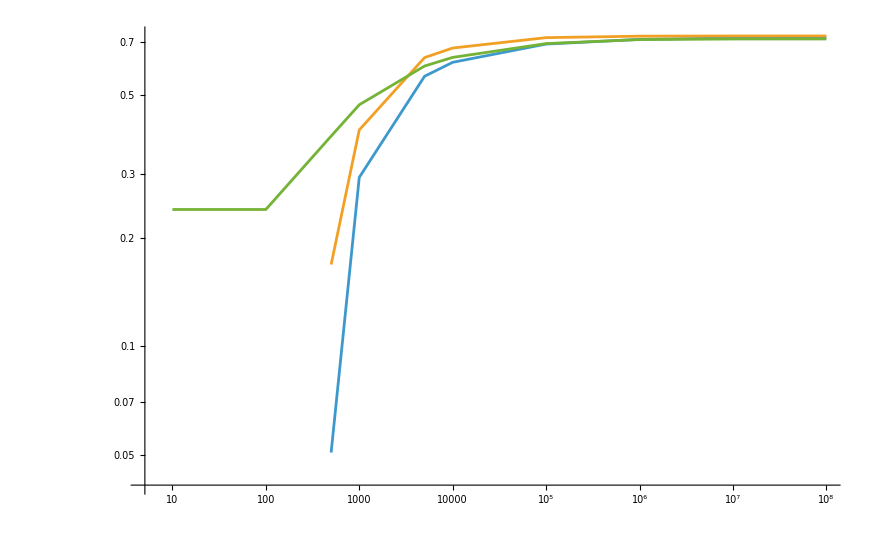

```mathematica
ListLogLogPlot[{{nlist,listRateBYEQn[[All,1]]}ᵀ,{nlist,listRateBYEQQ2n[[All,1]]}ᵀ,{nlist,listRateSandUp[[All,1]]}ᵀ},Joined->True]
```

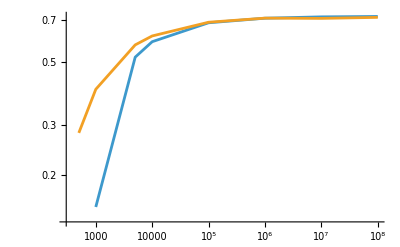

```mathematica
ListLogLogPlot[{{nlist,listRateBYEQn[[All,1]]}ᵀ,{nlist,listRateSandUp[[All,1]]}ᵀ},Joined->True]
```

## 3. AEP

```mathematica
Hvon=Compile[{{valsYE,_Complex,1},{vecsYE,_Complex,2},{valsE,_Complex,1}},
Module[{rhoYE,vYE,logrhoYE},
vYE=Transpose[vecsYE];
rhoYE=vYE.diag16C[valsYE].Inverse[vYE];
logrhoYE=vYE.diag16C[Log[valsYE]].Inverse[vYE];
(-Tr[rhoYE.logrhoYE]+Total[valsE Log[valsE]])/Log[2]
],
CompilationTarget->"C",RuntimeOptions->"Speed"];

AEPFast[α_?NumericQ,η_?NumericQ]:=Module[{rhoE,rhoYE,valsYE,vecsYE,valsE},
rhoE=rhoECompiled[α,η];
rhoYE=rhoYECompiledRe[α,η]+I rhoYECompiledIm[α,η];
{valsYE,vecsYE}=Eigensystem[rhoYE];
valsE=Eigenvalues[rhoE];
Hvon[valsYE,vecsYE,valsE]
]

objFunAEP[α_?NumericQ,η_?NumericQ,n_?NumericQ]:=Module[{val,safe=True},
If[α<=10^-6,Return[-penalty]];
Quiet[
Check[
val=AEPFast[α,η]-8 √(Log2[2/10^-8]/n) -compiledLeak[α,η]-(Log2[1/10.^(-8)]-1)/n;(*ϵ=10^-4*)
val=Chop@Re@val;
If[NumericQ[val]&&FreeQ[val,ComplexInfinity|Indeterminate|Infinity],val,safe=False],
safe=False]
];
If[safe,val,-penalty]]

RateAEP[η_?NumericQ,n_?NumericQ,nStart_Integer:6]:=NMaximize[{objFunAEP[α,η,n],α>0.0001},α,Method->"RandomSearch"]
```

```mathematica
nlist={10,50,10^2,5 10^2,10^3,5 10^3,10^4,10^5, 10^5,10^6,10^7,10^8};
```

```mathematica
{Row[{Dynamic[ni],"/",Last[nlist]}],ProgressIndicator[Dynamic[ni],{First[nlist],Last[nlist]}]}
```

{/100000000,}

```mathematica
listRateAEP=ParallelTable[RateAEP[.9,ni],{ni,nlist}]
```

{{-15.1219,{α→1.66019}},{-5.7323,{α→1.66019}},{-3.73644,{α→1.66019}},{-1.20959,{α→1.66019}},{-0.633749,{α→1.66019}},{0.12107,{α→1.66019}},{0.297638,{α→1.66019}},{0.587192,{α→1.66019}},{0.587192,{α→1.66019}},{0.678259,{α→1.66019}},{0.707007,{α→1.66019}},{0.716093,{α→1.66019}}}

```mathematica
listRateAEP={{-12.564385394883784,{α->1.66018976120771}},{-5.2207949910517994,{α->1.6601897709939923}},{-3.4806901827575496,{α->1.6601897325655133}},{-1.1584429948110715,{α->1.660189739722447}},{-0.6081735386490221,{α->1.6601897450403507}},{0.12618550173417653,{α->1.6601897450403507}},{0.30019598256360147,{α->1.6601897450403507}},{0.5874476469744541,{α->1.6601897450403507}},{0.5874476469744541,{α->1.6601897450403507}},{0.6782845990957165,{α->1.6601897450403507}},{0.7070097655368017,{α->1.6601897450403507}},{0.716093460748928,{α->1.6601897450403507}}};
```

### Plots

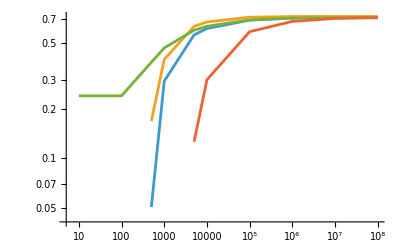

```mathematica
ListLogLogPlot[{{nlist,listRateBYEQn[[All,1]]}ᵀ,{nlist,listRateBYEQQ2n[[All,1]]}ᵀ,{nlist,listRateSandUp[[All,1]]}ᵀ,{nlist,listRateAEP[[All,1]]}ᵀ,{nlist,Table[HminUp1,{Length[nlist]}]}ᵀ},Joined->True]
```

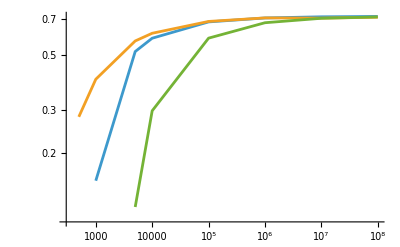

```mathematica
ListLogLogPlot[{{nlist,listRateBYEQn[[All,1]]}ᵀ,{nlist,listRateSandUp[[All,1]]}ᵀ,{nlist,listRateAEP[[All,1]]}ᵀ},Joined->True]
```

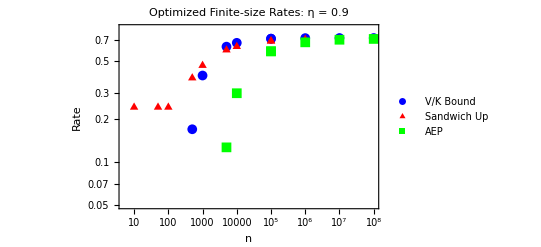

```mathematica
rateQPSK=ListPlot[{{nlist,listRateBYEQQ2n[[All,1]]}ᵀ,{nlist,listRateSandUp[[All,1]]}ᵀ,{nlist,listRateAEP[[All,1]]}ᵀ},PlotStyle->{Blue,Red,Green},PlotMarkers->{{"●",10},(*cerchio pieno*){"▲",10},(*triangolo pieno*){"■",10},(*quadrato pieno*){"◆",10}  (*rombo pieno*)},ScalingFunctions->{"Log","Log"},PlotRange->{Automatic,{0.05,0.85}},PlotLegends->Placed[LineLegend[{Blue,Red,Green,Orange},{Style["V/K Bound",FontSize->18],Style["Sandwich Up",FontSize->18],Style["AEP",FontSize->18]},
LegendMarkerSize->15,Spacings->1],Right],
Frame->True,FrameLabel->{Style["n",FontSize->14],Style["Rate",FontSize->14]},
FrameTicksStyle->Directive[Black,FontSize->12],GridLines->Automatic,PlotLabel->Style["Optimized Finite-size Rates: η = 0.9",FontSize->14]]
```

```mathematica
Export["/Users/Gabriele/Documents/Wolfram/PskPureLoss/grafici/RateQPSK.png",rateQPSK,ImageResolution->300]
```

/Users/Gabriele/Documents/Wolfram/PskPureLoss/grafici/RateQPSK.png

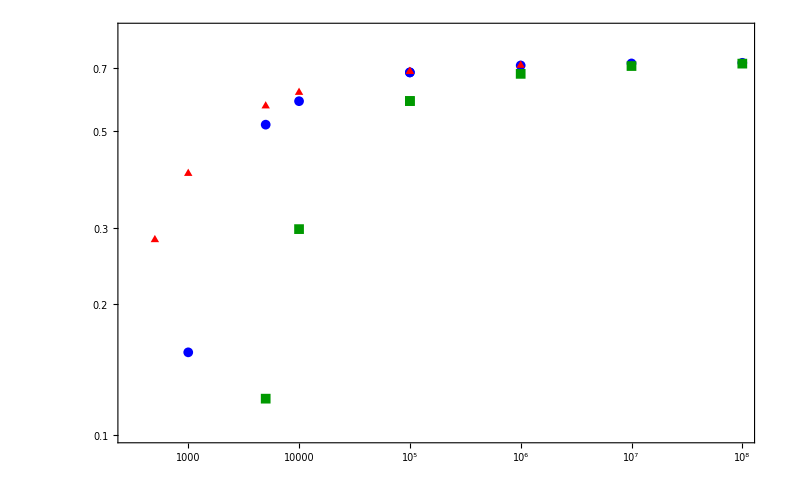

```mathematica
Needs["MaTeX`"];
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amsmath}"}];

data=Transpose/@{{nlist,listRateBYEQn[[All,1]]},{nlist,listRateSandUp[[All,1]]},{nlist,listRateAEP[[All,1]]}};

labels=MaTeX[#,Magnification->1.15]&/@{"r_{\\epsilon''}^{B}","r_{\\epsilon''}^{S}","r_{\\epsilon''}^{\\mathrm{AEP}}"};

colors={Blue,Red,Darker[Green,0.4]};
markers={{"●",10},{"▲",10},{"■",10}};

rateQPSK2=ListPlot[data,PlotStyle->colors,PlotMarkers->markers,ScalingFunctions->{"Log","Log"},PlotRange->{Automatic,{0.1,0.85}},PlotLegends->Placed[LineLegend[colors,labels,LegendMarkerSize->15,Spacings->1],Right],Frame->True,FrameLabel->{MaTeX["n",Magnification->1.1],MaTeX["\\text{Rate}",Magnification->1.1]},FrameTicksStyle->Directive[Black,12],GridLines->Automatic,PlotLabel->MaTeX["\\text{QPSK Optimized Finite-size Rates: }\\eta=0.9",Magnification->1.1]]
```

```mathematica
Export["/Users/Gabriele/Documents/Wolfram/PskPureLoss/grafici/RateQPSK2.png",rateQPSK2,ImageResolution->300]
```

/Users/Gabriele/Documents/Wolfram/PskPureLoss/grafici/RateQPSK2.png

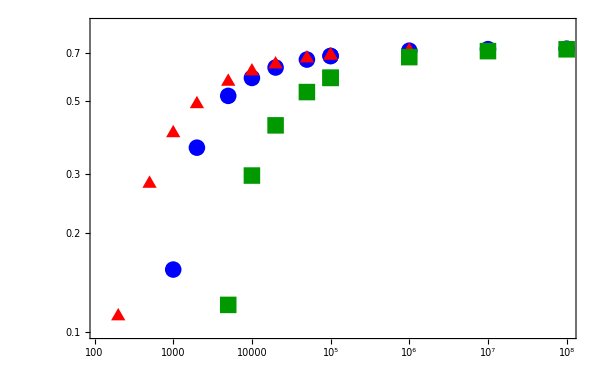

```mathematica
Needs["MaTeX`"];
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amsmath}"}];

dataQPSK={Transpose[{nlist,listRateBYEQn[[All,1]]}],Transpose[{nlist,listRateSandUp[[All,1]]}],Transpose[{nlist,listRateAEP[[All,1]]}]};

labelsQPSK=MaTeX[#,Magnification->2.5]&/@{"r_{\\epsilon''}^{B}","r_{\\epsilon''}^{S}","r_{\\epsilon''}^{\\mathrm{AEP}}"};

colorsQPSK={Blue,Red,Darker[Green,0.4]};
markersQPSK={{"●",17},{"▲",17},{"■",17}};

rateQPSK2=Legended[ListPlot[dataQPSK,PlotStyle->colorsQPSK,PlotMarkers->markersQPSK,ScalingFunctions->{"Log","Log"},PlotRange->{Automatic,{0.1,0.85}},Frame->True,BaseStyle->{FontFamily->"Times",FontSize->20},FrameTicksStyle->Directive[Black,Thick],FrameLabel->{MaTeX["n",Magnification->2.5],MaTeX["",Magnification->2.5]   (*niente label verticale*)},GridLines->Automatic,PlotLabel->None,(*niente titolo*)ImageSize->600],Placed[SwatchLegend[colorsQPSK,labelsQPSK,LegendMarkers->markersQPSK,LegendLayout->"Column",LegendMarkerSize->14],Right]]
```

### Zdenek HminUp

```mathematica
Hminq=Compile[{{α,_Real},{η,_Real},{q0,_Real},{q1,_Real},{q2,_Real}},
Module[{rhoYE=rhoYECompiledRe[α,η]+I*rhoYECompiledIm[α,η],
(*16×16 complex*)
rho1=ConstantArray[0.+0.I,{16,16}],
(*16×16 complex*)
rho2=ConstantArray[0.+0.I,{16,16}],λmax},
(*---fill rho1 (block-diagonal with 4×4 identity⊗diag(q)^{-.bd})---*)
Module[{s0=1/Sqrt[q0],s1=1/Sqrt[q1],s2=1/Sqrt[q2],s3=1/Sqrt[1.-q0-q1-q2],i},
For[i=0,i<=3,i++,
rho1[[4 i+1,4 i+1]]=s0;
rho1[[4 i+2,4 i+2]]=s1;
rho1[[4 i+3,4 i+3]]=s2;
rho1[[4 i+4,4 i+4]]=s3;
];
];
(*---ρ₂=ρ₁ ρYE ρ₁ and largest eigenvalue---*)
rho2=rho1.rhoYE.rho1;
λmax=N[Max@Re@Eigenvalues[rho2],MachinePrecision];
(*Eigenvalues is allowed in C target*)
-Log2[λmax]
],CompilationTarget->"C",RuntimeOptions->"Speed"];
```

CreateLibrary::cmperr: Compile error: /Users/gabriele/Library/Wolfram/ApplicationData/CCompilerDriver/BuildFolder/MacBook-Air-di-Gabriele-29887/Working-MacBook-Air-di-Gabriele-29887-4032372480-44/compiledFunction43.c:444:7: error: call to undeclared function 'F5'; ISO C99 and later do not support implicit function declarations [-Wimplicit-function-declaration]

CreateLibrary::cmperr: Compile error: /Users/gabriele/Library/Wolfram/ApplicationData/CCompilerDriver/BuildFolder/MacBook-Air-di-Gabriele-29887/Working-MacBook-Air-di-Gabriele-29887-4032372480-44/compiledFunction43.c:513:12: error: static declaration of 'F5' follows non-static declaration

CreateLibrary::cmperr: Compile error: /Users/gabriele/Library/Wolfram/ApplicationData/CCompilerDriver/BuildFolder/MacBook-Air-di-Gabriele-29887/Working-MacBook-Air-di-Gabriele-29887-4032372480-44/compiledFunction43.c:554:7: error: call to undeclared function 'F2'; ISO C99 and later do not support implicit function declarations [-Wimplicit-function-declaration]

General::stop: Further output of CreateLibrary::cmperr will be suppressed during this calculation.

Compile::nogen: A library could not be generated from the compiled function.

```mathematica
Hminq[1.5,.5,.2,.2,.2]
```

0.390853

```mathematica
penalty=10^8;
(****** --- ottimizzazione con le q --- ******)
objFunHminUp[α_?NumericQ,η_?NumericQ,q0_?NumericQ,q1_?NumericQ,q2_?NumericQ]:=Module[{val,safe=True},
If[α<=10^-6||q0<0||q1<0||q2<0||q0+q1+q2>0.9999,Return[-penalty]];
Quiet[
Check[
val=Hminq[α,η,q0,q1,q2]-compiledLeak[α,η];
val=Chop@Re@val;
If[NumericQ[val]&&FreeQ[val,ComplexInfinity|Indeterminate|Infinity],val,safe=False],
safe=False]
];
If[safe,val,-penalty]]

RateHminUp[η_?NumericQ,trials_Integer:6]:=Module[{results,seeds,obj,best},
seeds=MapThread[Join,{RandomReal[{0.01,0.99},{trials,3}],List/@RandomReal[{.5,2},trials]}];
results=ParallelTable[NMaximize[{objFunHminUp[α,η,q0,q1,q2],q0>N[10^-8],q1>N[10^-8],q2>N[10^-8],N[1-10^-8]>q0+q1+q2,α>0.0001},{q0,q1,q2,α},Method->{"NelderMead","InitialPoints"->{seed}}],{seed,seeds}];
best=First@MaximalBy[results,First];
best];
```

```mathematica
HminUp1=RateHminUp[.9][[1]]
```

0.239787

```mathematica
{nlist,Table[HminUp1,{Length[nlist]}]}ᵀ
```

{{10,0.239787},{50,0.239787},{100,0.239787},{500,0.239787},{1000,0.239787},{5000,0.239787},{10000,0.239787},{100000,0.239787},{100000,0.239787},{1000000,0.239787},{10000000,0.239787},{100000000,0.239787}}

## 3.2 QPSK optimized rates version 2 (better organized)

## 0. Run the C compiler

```mathematica
ClearAll["Global`*"];
```

```mathematica
Needs["CCompilerDriver`"]
CCompilers[]
```

{{Name→Visual Studio,Compiler→CCompilerDriver`VisualStudioCompiler`VisualStudioCompiler,CompilerInstallation→C:\Program Files\Microsoft Visual Studio\2022\Community,CompilerName→Automatic}}

```mathematica
cnumber2=Compile[{{x,_Complex}},
Sqrt[Re[x]^2.+Im[x]^2.]
,CompilationTarget->"C"
]
EigenvaluesC=Compile[{{x,_Complex,2}},
Eigenvalues[x]
,CompilationTarget->"C"
]
```

CompiledFunction[…]

CompiledFunction[…]

```mathematica
EigenvaluesC[{{3.,2.-I 1.},{2.+I 1.,7.}}]
```

{8.,2.}

```mathematica
AA=RandomReal[{0,1},{64,64}]+I RandomReal[{0,1},{64,64}];
AbsoluteTiming@Eigenvalues[AA]
```

{0.0206654,{32.1501+32.4003 ⅈ,-2.50442-2.26429 ⅈ,2.9745-1.53868 ⅈ,2.59724+2.09509 ⅈ,2.29578+2.39571 ⅈ,-1.32035-3.02882 ⅈ,0.798042+3.16982 ⅈ,-1.2118+3.00656 ⅈ,2.93541-1.03351 ⅈ,3.0162+0.689394 ⅈ,-2.59968-1.61156 ⅈ,-2.98467+0.595032 ⅈ,-0.726943-2.91374 ⅈ,-0.501133+2.88046 ⅈ,1.20725+2.63413 ⅈ,0.460937-2.82486 ⅈ,2.6676+0.965638 ⅈ,-2.66825+0.960845 ⅈ,1.73281-2.2134 ⅈ,-2.70833-0.420984 ⅈ,-0.221531+2.73183 ⅈ,-1.57886-2.18834 ⅈ,-2.24614+1.45101 ⅈ,1.54029-2.16823 ⅈ,-0.138009-2.63366 ⅈ,2.29845+1.24751 ⅈ,2.42727-0.712069 ⅈ,0.796478+2.39506 ⅈ,1.6242+1.91309 ⅈ,-1.84358-1.64085 ⅈ,2.0445-1.37233 ⅈ,0.852505-2.25887 ⅈ,-1.40238+1.92654 ⅈ,-0.935436+2.08937 ⅈ,1.64819-1.58554 ⅈ,-1.94275+1.08419 ⅈ,-2.08162-0.554312 ⅈ,2.14441+0.158953 ⅈ,-0.591705-1.90961 ⅈ,0.0717358-1.99626 ⅈ,0.04476+1.83693 ⅈ,-1.63071+0.844162 ⅈ,-0.787218-1.64188 ⅈ,-1.76598+0.371486 ⅈ,-1.65189-0.56692 ⅈ,-0.95991+1.45236 ⅈ,1.61215-0.474239 ⅈ,0.82093-1.46009 ⅈ,1.47778+0.771288 ⅈ,0.253899+1.60933 ⅈ,1.56925+0.00211829 ⅈ,0.560696+1.34563 ⅈ,-1.24897-0.749888 ⅈ,-0.154285-1.27214 ⅈ,0.984453+0.739696 ⅈ,0.846563-0.881302 ⅈ,-1.16467+0.189509 ⅈ,-0.729577-0.707548 ⅈ,0.0378654+0.871314 ⅈ,-0.828919+0.00502455 ⅈ,0.689621-0.195838 ⅈ,0.537373+0.370135 ⅈ,0.135767-0.368201 ⅈ,-0.19791-0.0375756 ⅈ}}

```mathematica
AbsoluteTiming@EigenvaluesC[AA]
```

{0.0022057,{32.1501+32.4003 ⅈ,-2.50442-2.26429 ⅈ,2.9745-1.53868 ⅈ,2.59724+2.09509 ⅈ,2.29578+2.39571 ⅈ,-1.32035-3.02882 ⅈ,0.798042+3.16982 ⅈ,-1.2118+3.00656 ⅈ,2.93541-1.03351 ⅈ,3.0162+0.689394 ⅈ,-2.59968-1.61156 ⅈ,-2.98467+0.595032 ⅈ,-0.726943-2.91374 ⅈ,-0.501133+2.88046 ⅈ,1.20725+2.63413 ⅈ,0.460937-2.82486 ⅈ,2.6676+0.965638 ⅈ,-2.66825+0.960845 ⅈ,1.73281-2.2134 ⅈ,-2.70833-0.420984 ⅈ,-0.221531+2.73183 ⅈ,-1.57886-2.18834 ⅈ,-2.24614+1.45101 ⅈ,1.54029-2.16823 ⅈ,-0.138009-2.63366 ⅈ,2.29845+1.24751 ⅈ,2.42727-0.712069 ⅈ,0.796478+2.39506 ⅈ,1.6242+1.91309 ⅈ,-1.84358-1.64085 ⅈ,2.0445-1.37233 ⅈ,0.852505-2.25887 ⅈ,-1.40238+1.92654 ⅈ,-0.935436+2.08937 ⅈ,1.64819-1.58554 ⅈ,-1.94275+1.08419 ⅈ,-2.08162-0.554312 ⅈ,2.14441+0.158953 ⅈ,-0.591705-1.90961 ⅈ,0.0717358-1.99626 ⅈ,0.04476+1.83693 ⅈ,-1.63071+0.844162 ⅈ,-0.787218-1.64188 ⅈ,-1.76598+0.371486 ⅈ,-1.65189-0.56692 ⅈ,-0.95991+1.45236 ⅈ,1.61215-0.474239 ⅈ,0.82093-1.46009 ⅈ,1.47778+0.771288 ⅈ,0.253899+1.60933 ⅈ,1.56925+0.00211829 ⅈ,0.560696+1.34563 ⅈ,-1.24897-0.749888 ⅈ,-0.154285-1.27214 ⅈ,0.984453+0.739696 ⅈ,0.846563-0.881302 ⅈ,-1.16467+0.189509 ⅈ,-0.729577-0.707548 ⅈ,0.0378654+0.871314 ⅈ,-0.828919+0.00502455 ⅈ,0.689621-0.195838 ⅈ,0.537373+0.370135 ⅈ,0.135767-0.368201 ⅈ,-0.19791-0.0375756 ⅈ}}

```mathematica
SetSystemOptions["ParallelOptions"->"ParallelThreadNumber"->6];
```

```mathematica
AbsoluteTiming[Table[Pause[1];f[i],{i,18}]]
```

{18.0254,{f[1],f[2],f[3],f[4],f[5],f[6],f[7],f[8],f[9],f[10],f[11],f[12],f[13],f[14],f[15],f[16],f[17],f[18]}}

```mathematica
AbsoluteTiming[ParallelTable[Pause[1];f[i],{i,18}]]
```

{3.04376,{f[1],f[2],f[3],f[4],f[5],f[6],f[7],f[8],f[9],f[10],f[11],f[12],f[13],f[14],f[15],f[16],f[17],f[18]}}

## 1. Sandwich Up

### Definitions

Preparazione degli stati

```mathematica
normVec=Compile[{{α,_Real},{η,_Real}},
Module[{t,e,e2,ns=ConstantArray[0.,4],s},t=α^2 (1-η);
e=Exp[-t];
e2=e*e;
For[s=0,s<=3,s++,ns[[s+1]]=1./Sqrt[1.+e2*Cos[Pi*s]+2.*e*Cos[Pi*s/2.+t]]];
ns],CompilationTarget->"C",RuntimeOptions->"Speed"];

PmatrixC=Compile[{{α,_Real},{η,_Real}},Module[{erf,erfc,r0,r1,r2,P=ConstantArray[0.,{4,4}]},erf=Erf[α*Sqrt[η/2.]];
erfc=1.-erf;
r0=0.25*(1.+erf)^2;
r1=0.25*(1.-erf^2);
r2=0.25*erfc^2;
P[[1]]={r0,r1,r2,r1};
P[[2]]={r1,r0,r1,r2};
P[[3]]={r2,r1,r0,r1};
P[[4]]={r1,r2,r1,r0};
P],CompilationTarget->"C",RuntimeOptions->"Speed"];

(*rhoEyC=Subscript[ρ, E|y][α,η] is a 4x4*)
rhoEyC=Compile[{{α,_Real},{η,_Real},{y,_Integer}},Module[{ns,Prow,ρ=ConstantArray[0.+0. I,{4,4}],s,s1,x,acc=0.+0.I},ns=normVec[α,η];
Prow=PmatrixC[α,η][[y+1]];
For[s=0,s<=3,s++,For[s1=0,s1<=3,s1++,acc=0.;
For[x=0,x<=3,x++,acc+=Prow[[x+1]]*Exp[I*Pi/2*(s-s1)*x];];
ρ[[s+1,s1+1]]=acc/(4.*ns[[s+1]]*ns[[s1+1]]);];];
Chop[ρ,10^-10]
],CompilationTarget->"C",RuntimeOptions->"Speed"];

(*rhoYEC=.25 diag{Subscript[ρ, E|0][α,η],...,Subscript[ρ, E|3][α,η]} is a 16x16*)
rhoYECompiled=Compile[{{α,_Real},{η,_Real}},
Module[{ρYE=ConstantArray[0.+0.I,{16,16}],y,i,j,blk=ConstantArray[0.+0.I,{4,4}]},
For[y=0,y<=3,y++,
blk=rhoEyC[α,η,y];(*4×4 block*)
For[i=1,i<=4,i++,
For[j=1,j<=4,j++,ρYE[[4*y+i,4*y+j]]=blk[[i,j]];
];
];
];
ρYE/4.],CompilationTarget->"C",RuntimeOptions->"Speed"];

(*Subscript[ρ, E][α,η]*)
rhoECompiled=Compile[{{α,_Real},{η,_Real}},Module[{ns=normVec[α,η],ρ=ConstantArray[0.,{4,4}],s},
Do[s;
ρ[[s,s]]=1/(4. ns[[s]]^2.),{s,4}];
ρ],
CompilationTarget->"C",RuntimeOptions->"Speed"];
```

Funzionali da ottimizzare

```mathematica
sandUp=Compile[{{α,_Real},{η,_Real},{a,_Real},{q0,_Real},{q1,_Real},{q2,_Real}},
Module[{σ=ConstantArray[0.-0.I,{4,4}],ρ=ConstantArray[0.+0.I,{4,4}],λ=ConstantArray[0.,4],tr=0.},
σ=DiagonalMatrix[{q0^(-.5+.5/a),q1^(-.5+.5/a),q2^(-.5+.5/a),(1.-q0-q1-q2)^(-.5+.5/a)}];
ρ=rhoEyC[α,η,0]; (*Subscript[ρE, 0][α,η]*)
λ=Flatten[Re[Eigenvalues[σ.ρ.σ]]];
tr=Total[λ^a];
2.+Log[tr]/((1.-a)*Log[2.])
],
CompilationTarget->"WVM",RuntimeOptions->"Speed"];
```

```mathematica
matPow=Compile[{{vals,_Complex,1},{vecs,_Complex,2},{p,_Real}},
Module[{inv,vecst},
vecst=Transpose[vecs];
(*vals=clipλ[vals]^p;*)
inv=Inverse[vecst];
vecst.DiagonalMatrix[vals^p].inv
],
CompilationTarget->"C",RuntimeOptions->"Speed"];


diagRe=Compile[{{v,_Real,1}},
Module[{d=ConstantArray[0.,{Length[v],Length[v]}],i,n},
n=Length[v];
For[i=1,i<=n,i++,d[[i,i]]=v[[i]]];
d],CompilationTarget->"C",RuntimeOptions->"Speed"];
```

```mathematica
bYEC=Compile[{{α,_Real},{η,_Real},{a,_Real},{q0,_Real},{q1,_Real},{q2,_Real}},
Module[
{rhoE=ConstantArray[0.,{4,4}],valsE=ConstantArray[0.,4],
rhoYE=ConstantArray[0.+0.I,{16,16}] ,valsYE=ConstantArray[0.,16],vecsYE=Table[0.+0.I,{16},{16}],
idRhoE=ConstantArray[0.,{16,16}],valsId=ConstantArray[0.,16],
rhoYEa,idRhoE1a,
MatLogrhoYE,diff,HYE,VYE,Hd2,Hda,K(*real?*)},

rhoE=rhoECompiled[α,η]; (*real*)
valsE=Flatten[Re[Eigenvalues[rhoE]]];(*real*)
rhoYE=rhoYECompiled[α,η];(*complex*)
valsYE=Flatten@Re[Eigenvalues[rhoYE]];(*complex*)
vecsYE=Chop[Transpose[Eigenvectors[rhoYE]]];(*complex*)
idRhoE=diagRe[{1.,1.,1.,1.}]~KroneckerProduct~diagRe[{q0,q1,q2,(1-q0-q1-q2)}]; (*real*)
valsId=Flatten[Re[Eigenvalues[idRhoE]]];(*real*)

(*eleviamo a potenza*)
rhoYEa=Chop[matPow[valsYE,vecsYE,a]];(*forse si può cambiare*)
idRhoE1a=diagRe[valsId^(1.-a)];
(*entropia condizionata–formula solo su vettori*)
MatLogrhoYE=vecsYE.diagRe[Log[valsYE]].ConjugateTranspose[vecsYE];(*non sappiamo su Re[valsYE] diventa real*)
diff=MatLogrhoYE-diagRe[Log[valsId]]; (*real*)

HYE=Max[0.,Re[(-Tr[rhoYE.MatLogrhoYE]+Total[valsE Log[valsE]])/Log[2]]];
VYE=Max[0.,Re[(Tr[rhoYE.diff.diff]/(Log[2.]^2.))-HYE^2.]];

Hd2=Max[0.,-Re[Log2[Tr[rhoYE.rhoYE.diagRe[1/valsId]]]]];

Hda=Max[0.,Re[Log2[Tr[rhoYEa.idRhoE1a]]/(1.-a)]];

K=Re[(1./(6. (2.-a)^3 Log[2.]))*2.^((a-1.) (-Hda+HYE))*(Log[2.^(-Hd2+HYE)+Exp[2.]])^3];

Re[HYE-((a-1.) *Log[2.]* VYE)/2.-K*(a-1.)^2 ]

],
CompilationTarget->"C",RuntimeOptions->"Speed"];
```

```mathematica
bYEC[1.61,.9,1.001,.25,.25,.25]
```

CompiledFunction::cfte: Compiled expression {0.771806,0.20003,0.0259242,0.00223992} should be a rank 2 tensor of machine-size real numbers.

CompiledFunction::cfexe: Could not complete external evaluation; proceeding with uncompiled evaluation.

1.40018

Funzioni in comune a tutti i funzionali

```mathematica
compiledLeak=Compile[{{α,_Real},{η,_Real}},
Module[{term},
term=Erf[0.7071067811865475*α*Sqrt[η]];
-2*(0.7213475204444817*(1-term)*Log[0.5 (1-term)]+0.7213475204444817*(1+term)*Log[0.5 (1+term)])
],
CompilationTarget->"C",
RuntimeOptions->"Speed"];
```

```mathematica
objFun[α_?NumericQ,a_?NumericQ,q0_?NumericQ,q1_?NumericQ,q2_?NumericQ,η_?NumericQ,n_?NumericQ,fun_]:=Module[{val,safe=True,penalty=10^6},
If[a<=1.01||α<=10^-6||q0<0.||q1<0.||q2<0.||q0+q1+q2>0.999999,Return[-penalty]];
Quiet[
Check[
val=fun[α,η,a,q0,q1,q2]-Log[2./10.^(-16)]/(n (a-1.))-compiledLeak[α,η];
val=Chop@Re@val;
If[NumericQ[val]&&FreeQ[val,ComplexInfinity|Indeterminate|Infinity],val,safe=False],
safe=False
]
];
If[safe,val,-penalty]
];

Rate[η_?NumericQ,n_?NumericQ,fun_,trials_Integer:6]:=Module[{results,seeds,obj,best,q0,q1,q2,a,α},

seeds=MapThread[Join,{RandomReal[{0.01,0.99},{trials,3}],List/@RandomReal[{1.0001,1.5},trials],List/@RandomReal[{.5,2},trials]}];

results=ParallelTable[NMaximize[{objFun[α,a,q0,q1,q2,η,n,fun],q0>N[10^-8],q1>N[10^-8],q2>N[10^-8],q0+q1+q2<N[1-10^-8],If[fun===bYEC,1.999>a>1.00001,a>1.00001],α>10^-6},{q0,q1,q2,a,α},Method->{"NelderMead","InitialPoints"->{seed}},MaxIterations->500],{seed,seeds}];
best=First@MaximalBy[results,First];
{best[[1]],{q0,q1,q2,a,α} /.best[[2]]}];
```

```mathematica
Rate[.59, 10^4,bYEC]
```

{1.99963,{0.114163,0.273095,0.256061,1.01,0.0453761}}

```mathematica
Rate[.59, 10^4,sandUp,6]
```

{2.,{0.999998,1.×10^-8,1.×10^-8,6.66243,0.00196913}}

```mathematica
0.6490014558112682-0.6338215169690289
```

0.0151799

### Runs

```mathematica
{Row[{Dynamic[ηi],"/",1}],ProgressIndicator[Dynamic[ηi],{0,1}]}
```

{/1,}

```mathematica
nlist={10,50,10^2,5 10^2,10^3,5 10^3,10^4,10^5, 10^5,10^6,10^7,10^8}
```

{10,50,100,500,1000,5000,10000,100000,100000,1000000,10000000,100000000}

```mathematica
First[nlist]
```

10

```mathematica
RateSandUpMultiStart[0.9,10^8,12]
```

{0.70572,{q0→0.719915,q1→0.00312951,q2→0.031039,a→1.01003,α→1.78739}}

```mathematica
listRateSandUp=Table[RateSandUpMultiStart[.9,ni],{ni,nlist}]
```

```mathematica
listRateSandUp={{-3.3171417078049563,{q0->0.6766146466486811,q1->0.01143583663083629,q2->0.0560058598332974,a->1.999999999961204,α->1.5984184183122838}},{-0.3143810142367319,{q0->0.6766098542344653,q1->0.01143633752682978,q2->0.05600742560852217,a->2.,α->1.5984326216875708}},{0.06096407248870894,{q0->0.6766126229512488,q1->0.011436032866437112,q2->0.05600661140392967,a->2.,α->1.5984238621648295}},{0.38322923725141,{q0->0.7107436629637744,q1->0.007410259828728778,q2->0.0439286363538537,a->1.5590984174937248,α->1.57807919802355}},{0.46820338038592424,{q0->0.728039787414541,q1->0.0055350623288744965,q2->0.03822702296705488,a->1.3415260062134646,α->1.5903475682961044}},{0.5997910327760934,{q0->0.7460733446447922,q1->0.00374909157505134,q2->0.0326256829203133,a->1.1312734316291475,α->1.6241804442053294}},{0.633821516969016,{q0->0.7499852516503548,q1->0.003400354933495334,q2->0.031470117676727694,a->1.0899729765119246,α->1.6340819229338828}},{0.6922970399586563,{q0->0.7563466532486846,q1->0.002873574477544296,q2->0.029648149197920404,a->1.0271029136833083,α->1.6516247659018646}},{0.6922970399586549,{q0->0.7563466982082183,q1->0.0028735669902413266,q2->0.029648141917318516,a->1.0271029217551293,α->1.6516246803317172}},{0.7110533916325711,{q0->0.7621724500210219,q1->0.0021826836294475144,q2->0.028064124905397014,a->1.0101429378610784,α->1.65823187709892}},{0.6921017757637468,{q0->0.677526007777362,q1->0.007643047330446001,q2->0.0391375503051995,a->1.0100000011825585,α->1.863135149899416}},{0.6883466882487883,{q0->0.7808949797030984,q1->0.021340808011069735,q2->0.02549577294128098,a->1.01000000204472,α->1.5690569397544976}}};
```

## 3. AEP

```mathematica
Hvon=Compile[{{valsYE,_Complex,1},{vecsYE,_Complex,2},{valsE,_Complex,1}},
Module[{rhoYE,vYE,logrhoYE},
vYE=Transpose[vecsYE];
rhoYE=vYE.diag16C[valsYE].Inverse[vYE];
logrhoYE=vYE.diag16C[Log[valsYE]].Inverse[vYE];
(-Tr[rhoYE.logrhoYE]+Total[valsE Log[valsE]])/Log[2]
],
CompilationTarget->"C",RuntimeOptions->"Speed"];

AEPFast[α_?NumericQ,η_?NumericQ]:=Module[{rhoE,rhoYE,valsYE,vecsYE,valsE},
rhoE=rhoECompiled[α,η];
rhoYE=rhoYECompiledRe[α,η]+I rhoYECompiledIm[α,η];
{valsYE,vecsYE}=Eigensystem[rhoYE];
valsE=Eigenvalues[rhoE];
Hvon[valsYE,vecsYE,valsE]
]

objFunAEP[α_?NumericQ,η_?NumericQ,n_?NumericQ]:=Module[{val,safe=True},
If[α<=10^-6,Return[-penalty]];
Quiet[
Check[
val=AEPFast[α,η]-8 √(Log2[2/10^-8]/n) -compiledLeak[α,η];(*ϵ=10^-4*)
val=Chop@Re@val;
If[NumericQ[val]&&FreeQ[val,ComplexInfinity|Indeterminate|Infinity],val,safe=False],
safe=False]
];
If[safe,val,-penalty]]

RateAEP[η_?NumericQ,n_?NumericQ,nStart_Integer:6]:=NMaximize[{objFunAEP[α,η,n],α>0.0001},α,Method->"RandomSearch"]
```

```mathematica
nlist={10,50,10^2,5 10^2,10^3,5 10^3,10^4,10^5, 10^5,10^6,10^7,10^8};
```

```mathematica
{Row[{Dynamic[ni],"/",Last[nlist]}],ProgressIndicator[Dynamic[ni],{First[nlist],Last[nlist]}]}
```

{/100000000,}

```mathematica
listRateAEP=ParallelTable[RateAEP[.9,ni],{ni,nlist}]
```

```mathematica
listRateAEP={{-12.564385394883784,{α->1.66018976120771}},{-5.2207949910517994,{α->1.6601897709939923}},{-3.4806901827575496,{α->1.6601897325655133}},{-1.1584429948110715,{α->1.660189739722447}},{-0.6081735386490221,{α->1.6601897450403507}},{0.12618550173417653,{α->1.6601897450403507}},{0.30019598256360147,{α->1.6601897450403507}},{0.5874476469744541,{α->1.6601897450403507}},{0.5874476469744541,{α->1.6601897450403507}},{0.6782845990957165,{α->1.6601897450403507}},{0.7070097655368017,{α->1.6601897450403507}},{0.716093460748928,{α->1.6601897450403507}}};
```

## Plots

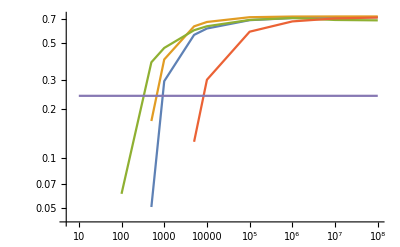

```mathematica
ListLogLogPlot[{{nlist,listRateBYEQn[[All,1]]}ᵀ,{nlist,listRateBYEQQ2n[[All,1]]}ᵀ,{nlist,listRateSandUp[[All,1]]}ᵀ,{nlist,listRateAEP[[All,1]]}ᵀ,{nlist,Table[HminUp1,{Length[nlist]}]}ᵀ},Joined->True]
```

## Zdenek HminUp

```mathematica
ClearAll["Global`*"];
```

```mathematica
Hminq=Compile[{{α,_Real},{η,_Real},{q0,_Real},{q1,_Real},{q2,_Real}},
Module[{rhoYE=rhoYECompiledRe[α,η]+I*rhoYECompiledIm[α,η],
(*16×16 complex*)
rho1=ConstantArray[0.+0.I,{16,16}],
(*16×16 complex*)
rho2=ConstantArray[0.+0.I,{16,16}],λmax},
(*---fill rho1 (block-diagonal with 4×4 identity⊗diag(q)^{-.bd})---*)
Module[{s0=1/Sqrt[q0],s1=1/Sqrt[q1],s2=1/Sqrt[q2],s3=1/Sqrt[1.-q0-q1-q2],i},
For[i=0,i<=3,i++,
rho1[[4 i+1,4 i+1]]=s0;
rho1[[4 i+2,4 i+2]]=s1;
rho1[[4 i+3,4 i+3]]=s2;
rho1[[4 i+4,4 i+4]]=s3;
];
];
(*---ρ₂=ρ₁ ρYE ρ₁ and largest eigenvalue---*)
rho2=rho1.rhoYE.rho1;
λmax=N[Max@Re@Eigenvalues[rho2],MachinePrecision];
(*Eigenvalues is allowed in C target*)
-Log2[λmax]
],CompilationTarget->"C",RuntimeOptions->"Speed"];
```

```mathematica
Hminq[1.5,.5,.2,.2,.2]
```

0.390853

```mathematica
penalty=10^8;
(****** --- ottimizzazione con le q --- ******)
objFunHminUp[α_?NumericQ,η_?NumericQ,q0_?NumericQ,q1_?NumericQ,q2_?NumericQ]:=Module[{val,safe=True},
If[α<=10^-6||q0<0||q1<0||q2<0||q0+q1+q2>0.9999,Return[-penalty]];
Quiet[
Check[
val=Hminq[α,η,q0,q1,q2]-compiledLeak[α,η];
val=Chop@Re@val;
If[NumericQ[val]&&FreeQ[val,ComplexInfinity|Indeterminate|Infinity],val,safe=False],
safe=False]
];
If[safe,val,-penalty]]

RateHminUp[η_?NumericQ,trials_Integer:6]:=Module[{results,seeds,obj,best},
seeds=MapThread[Join,{RandomReal[{0.01,0.99},{trials,3}],List/@RandomReal[{.5,2},trials]}];
results=ParallelTable[NMaximize[{objFunHminUp[α,η,q0,q1,q2],q0>N[10^-8],q1>N[10^-8],q2>N[10^-8],N[1-10^-8]>q0+q1+q2,α>0.0001},{q0,q1,q2,α},Method->{"NelderMead","InitialPoints"->{seed}}],{seed,seeds}];
best=First@MaximalBy[results,First];
best];
```

```mathematica
HminUp1=RateHminUp[.9][[1]]
```

0.239787

```mathematica
{nlist,Table[HminUp1,{Length[nlist]}]}ᵀ
```

{{10,0.239787},{50,0.239787},{100,0.239787},{500,0.239787},{1000,0.239787},{5000,0.239787},{10000,0.239787},{100000,0.239787},{100000,0.239787},{1000000,0.239787},{10000000,0.239787},{100000000,0.239787}}